## 1

```mathematica
Clear["Global`*"];
dim=5/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=N[MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5]*t] ]
IniPhi={{1},{0},{0},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^5},{√5 ⅇ^(ⅈ ϕ) Cos[θ/2]^4 Sin[θ/2]},{1/4 √(5/2) ⅇ^(2 ⅈ ϕ) Csc[θ/2] Sin[θ]^3},{1/2 √(5/2) ⅇ^(3 ⅈ ϕ) Sin[θ/2] Sin[θ]^2},{1/2 √5 ⅇ^(4 ⅈ ϕ) Sin[θ/2]^3 Sin[θ]},{ⅇ^(5 ⅈ ϕ) Sin[θ/2]^5}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,θ_,ϕ_]:=N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].StateθϕInitial[θ,ϕ]]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
(*ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]*)
ξSqure[state_]:=Chop[1*N[First[Flatten[  (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((ConjugateTranspose[state].Ix3half2.state)^2+(ConjugateTranspose[state].Iy3half2.state)^2+(ConjugateTranspose[state].Iz3half2.state)^2)]]]+0*Abs[First[Flatten[ConjugateTranspose[state].Iy3half2.state]]]+0*Abs[First[Flatten[ConjugateTranspose[state].Iz3half2.state]]]]
```

```mathematica
2.5*ξSqure[Chop[N[StateEvo[1.4267131148515073,1.697953795751256,1.9324372999121295,2.44753115273887,1.7559400582907179,0.5,Pi/2,Pi/2]]]]
```

0.388284

```mathematica
StateEvo[1.4267131148515073,1.697953795751256,1.9324372999121295,2.44753115273887,1.7559400582907179,0.5,Pi/2,Pi/2]
```

{{0.0896516-0.171858 ⅈ},{0.331549+0.108655 ⅈ},{-0.159694+0.424182 ⅈ},{-0.45474-0.113305 ⅈ},{0.53577-0.462552 ⅈ},{-0.248825+0.346948 ⅈ}}

```mathematica
StateEvo[1.4267131148515073,1.697953795751256,1.9324372999121295,2.44753115273887,1.7559400582907179,0,Pi/2,Pi/2]
```

{{0.176777+0. ⅈ},{0.+0.395285 ⅈ},{-0.559017+0. ⅈ},{0.-0.559017 ⅈ},{0.395285+0. ⅈ},{0.+0.176777 ⅈ}}

```mathematica
phi1=Pi/2;
phi2=Pi/2;

ϕ1gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]])/10^-8
ϕ2gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]])/10^-8
ϕ3gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,t,phi1,phi2]]]])/10^-8
ϕ4gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,t,phi1,phi2]]]])/10^-8
ϕ5gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,t,phi1,phi2]]]])/10^-8

ϕ1graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,t].state]]])/10^-8
ϕ4graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,t].state]]])/10^-8
ϕ5graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,t].state]]])/10^-8
```

False

```mathematica
durationnumber=1;
avenumber=20;
SqueezeTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
SqueezeTableduration2=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
phiMinTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
Do[
Do[
If[Divisible[k,5],Print["durationnumber:",k,"  avenumber:",m]];
(*totT=Pi/2*k/durationnumber;*)
totT=0.5;
itenumber=200;
ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];

SqueezeTable=Table[0,{i,1,itenumber}];

SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],ϕTable[[1,4]],ϕTable[[1,5]],totT,phi1,phi2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.4*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],totT];
ϕTable[[i,2]]=ϕTable[[i-1,2]]-0.4*ϕ2gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],totT];
ϕTable[[i,3]]=ϕTable[[i-1,3]]-0.4*ϕ3gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],totT];
ϕTable[[i,4]]=ϕTable[[i-1,4]]-0.4*ϕ4gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],totT];
ϕTable[[i,5]]=ϕTable[[i-1,5]]-0.4*ϕ5gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],totT];
SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],ϕTable[[i,4]],ϕTable[[i,5]],totT,phi1,phi2]]]];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];

SqueezeTableduration[[k,m]]=Min[SqueezeTable];
phiMinTableduration[[k,m]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]][[1]]]];



ExtraPiece=1;
ϕTableExtraPiece=Table[Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}],{j,1,ExtraPiece}];
StateExtraPiece=Table[0,{j,1,ExtraPiece+1}];
StateExtraPiece[[1]]=UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],Last[ϕTable][[4]],Last[ϕTable][[5]],totT].StateθϕInitial[phi1,phi2];
SqueezeTableExtraPiece=Table[Table[0,{i,1,itenumber}],{j,1,ExtraPiece}];
SqueezeTableExtraPiece[[1,1]]=ξSqure[StateExtraPiece[[1]]];
Do[

Do[ 
ϕTableExtraPiece[[j,i,1]]=ϕTableExtraPiece[[j,i-1,1]]-0.3*ϕ1graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,2]]=ϕTableExtraPiece[[j,i-1,2]]-0.3*ϕ2graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,3]]=ϕTableExtraPiece[[j,i-1,3]]-0.3*ϕ3graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,4]]=ϕTableExtraPiece[[j,i-1,4]]-0.3*ϕ4graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,5]]=ϕTableExtraPiece[[j,i-1,5]]-0.3*ϕ5graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],totT,StateExtraPiece[[j]]];
SqueezeTableExtraPiece[[j,i]]=ξSqure[Chop[N[UHmuti[ϕTableExtraPiece[[j,i,1]],ϕTableExtraPiece[[j,i,2]],ϕTableExtraPiece[[j,i,3]],ϕTableExtraPiece[[j,i,4]],ϕTableExtraPiece[[j,i,5]],totT].StateExtraPiece[[j]]]]];


,{i,2,itenumber}];
StateExtraPiece[[j+1]]=UHmuti[Last[ϕTableExtraPiece[[j]]][[1]],Last[ϕTableExtraPiece[[j]]][[2]],Last[ϕTableExtraPiece[[j]]][[3]],Last[ϕTableExtraPiece[[j]]][[4]],Last[ϕTableExtraPiece[[j]]][[5]],totT].StateExtraPiece[[j]];

,{j,1,ExtraPiece}];


SqueezeTableduration[[k,m]]=Min[SqueezeTable];
SqueezeTableduration2[[k,m]]=Min[SqueezeTableExtraPiece[[1]]];


,{k,1,durationnumber}]
,{m,1,avenumber}]
```

```mathematica
MinSqueeze=Table[0,{i,1,durationnumber}];
Minphi=Table[0,{i,1,durationnumber}];
Do[
MinSqueeze[[i]]=Min[SqueezeTableduration[[i]]];
Minphi[[i]]=ϕTable[[Flatten[Position[SqueezeTableduration[[i]],Min[SqueezeTableduration[[i]]]]][[1]]]];
,{i,1,durationnumber}]
```

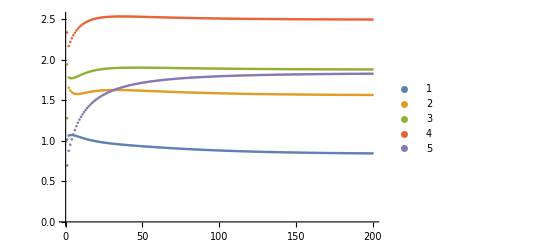

```mathematica
ListPlot[Transpose[ϕTable],PlotLegends->Automatic]
```

```mathematica
SqueezeTable
```

SqueezeTable

```mathematica
Last[ϕTable]
```

{0.845049,1.56596,1.88087,2.49696,1.82847}

```mathematica
2.5*ξSqure[Chop[N[StateEvo[0.8450487708132455,1.565957907128059,1.8808732122886962,2.4969607869855706,1.8284662256334436,0.5,Pi/2,Pi/2]]]]
```

0.358856

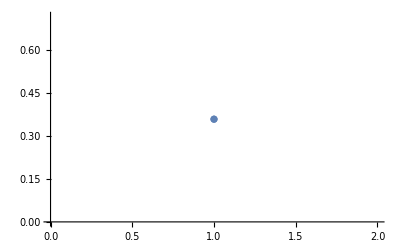

```mathematica
ListPlot[(2.5MinSqueeze)/1,PlotRange->All]
```

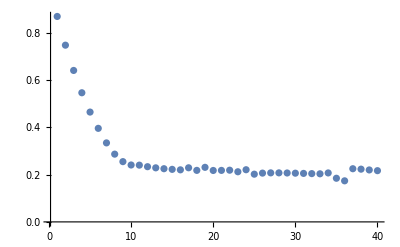

```mathematica
ListPlot[MinSqueeze/(5/2),PlotRange->All]
```

```mathematica
MinSqueeze
```

{0.146234}

```mathematica
Minphi
```

{{1.42671,1.69795,1.93244,2.44753,1.75594}}

```mathematica
UIz[t_]:=MatrixExp[-I*Iz3half2.Iz3half2*t]
IzIzTable=Table[0,{j,1,durationnumber}];
Do[
IzIzTable[[i]]=ξSqure[UIz[Pi/2*i/durationnumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,durationnumber}];
```

N::meprec: 当计算 5/32-5/32 Cos[π/8]^2-5/32 Sin[π/8]^2 时，达到内部精确度极限值 $MaxExtraPrecision = 50..

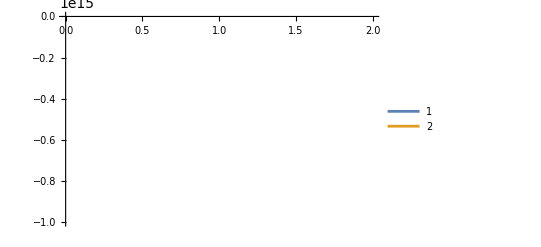

```mathematica
ListPlot[{MinSqueeze/(5/2),IzIzTable/(5/2)},Joined->True,PlotRange->All,PlotRange->All,PlotLegends->Automatic]
```

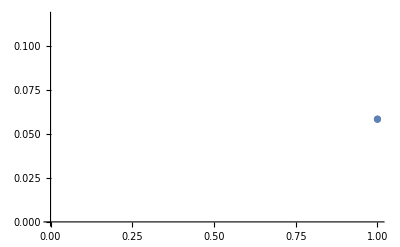

```mathematica
ListPlot[MinSqueeze/(5/2)]
```

```mathematica
durationnumber=100;
avenumber=50;

PlotpieceNumber=100;
UIz[t_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t]

IzIzTable=Table[0,{j,1,PlotpieceNumber}];


UIz4[t_]:=MatrixExp[-I*Iz3half2.Iz3half2.Iz3half2.Iz3half2*t]
```

```mathematica
IzIzIzIzTable=Table[0,{j,1,PlotpieceNumber}];
Do[
IzIzIzIzTable[[i]]=ξSqure[UIz4[Pi/2*i/durationnumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,PlotpieceNumber}];
Do[
IzIzTable[[i]]=ξSqure[UIz[Pi/2*i/durationnumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,PlotpieceNumber}];

UIXIY[t_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t]
IxIyTable=Table[0,{j,1,PlotpieceNumber}];
Do[
IxIyTable[[i]]=ξSqure[UIXIY[Pi/2*i/durationnumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,PlotpieceNumber}];
```

```mathematica
IzIzTable/(5/2)
```

{0.938656,0.880312,0.824989,0.772691,0.723406,0.677109,0.63376,0.593309,0.5557,0.520865,0.488731,0.459223,0.432259,0.407757,0.385632,0.365801,0.348178,0.33268,0.319227,0.307737,0.298134,0.290344,0.284293,0.279914,0.27714,0.275909,0.27616,0.277837,0.280886,0.285255,0.290897,0.297765,0.305815,0.315007,0.325299,0.336654,0.349033,0.362402,0.376724,0.391963,0.408083,0.425046,0.442814,0.461345,0.480595,0.500517,0.521058,0.54216,0.56376,0.585786,0.608161,0.630797,0.653599,0.676463,0.699275,0.721914,0.744253,0.766159,0.787498,0.808135,0.827942,0.846798,0.864595,0.881242,0.896668,0.910824,0.923687,0.935257,0.945558,0.954634,0.962548,0.969376,0.975206,0.980131,0.984247,0.987649,0.99043,0.992677,0.994472,0.995886,0.996986,0.99783,0.998467,0.998939,0.999283,0.999528,0.999699,0.999815,0.999891,0.999939,0.999967,0.999984,0.999993,0.999997,0.999999,1.,1.,1.,1.,1.}

```mathematica
IxIyTable/(5/2)
```

{0.9387,0.88065,0.826077,0.775151,0.727989,0.684669,0.645231,0.609688,0.578032,0.550236,0.526258,0.506042,0.489522,0.476618,0.46724,0.461282,0.458625,0.459136,0.462663,0.469042,0.478089,0.489606,0.503379,0.519177,0.536757,0.555855,0.576189,0.597453,0.619307,0.641367,0.663187,0.684243,0.703913,0.721475,0.736124,0.747037,0.753489,0.754996,0.751439,0.743096,0.730565,0.71463,0.696116,0.675801,0.654365,0.632389,0.610363,0.588705,0.567781,0.547914,0.529402,0.512516,0.497514,0.484632,0.474096,0.466112,0.460873,0.458555,0.459317,0.463302,0.470639,0.48144,0.495806,0.513822,0.535562,0.561089,0.590452,0.623688,0.660816,0.701838,0.746729,0.795434,0.847862,0.903875,0.963279,0.97467,0.914661,0.858003,0.804897,0.755491,0.709887,0.668143,0.630291,0.596333,0.566253,0.540016,0.517577,0.498875,0.483837,0.47238,0.464408,0.459809,0.458459,0.460217,0.464926,0.472414,0.482491,0.494953,0.509579,0.526134}

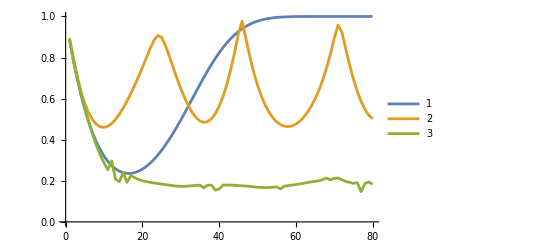
```mathematica
ListPlot[{IzIzTable/(5/2),IxIyTable/(5/2),MinSqueeze/(5/2),MinSqueeze2/(5/2)},Joined->True,PlotLegends->Automatic]
-Graphics-
```

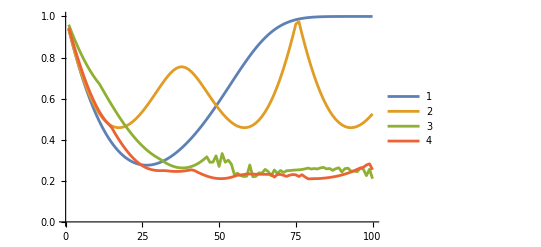

-Graphics-

```mathematica
MinSqueeze5={2.358087850242376,2.2229403979616205,2.095338157046287,1.9748476272925815,1.8613392729635105,1.7546865611957374,1.6547654022363725,1.56145348239676,1.4746283040097963,1.3941634667457228,1.3199229276226427,1.2517535551040564,1.1894775516688763,1.1328881491655773,1.0817527611635511,1.0358243525305646,0.9936042943253005,0.9441984904361789,0.8994502728598355,0.860174040725501,0.8265188219655233,0.7986166645609201,0.7765821011678242,0.7441246904192602,0.7504829602378802,0.743104164984993,0.7191777454854744,0.6979450557432001,0.6793792079488736,0.6632773261271891,0.6493007690213441,0.6370859414509864,0.6263441745624982,0.6168870638808013,0.6086065493546604,0.6004201713310664,0.5929792209206313,0.5868717734688711,0.5820996119823656,0.5787528501507491,0.5770041250014506,0.5771071077220937,0.5793934688039233,0.5842620227261559,0.5873633157354314,0.5894237414267325,0.5874703261060121,0.5809696738703836,0.5744882135428564,0.5700643717377436,0.56380388603981,0.5575693150717287,0.5514167387254654,0.545385682834616,0.5395063406272498,0.5338030929065076,0.5282963811650094,0.5230037653848907,0.5192131365395687,0.5257250826424653,0.5168248538870506,0.5059941865980493,0.502127530052165,0.5161282613756555,0.49373873052124795,0.5077613707680846,0.4896626103807775,0.4949852051807957,0.4835058387405762,0.48341935591667884,0.4815620051905096,0.48000400866282655,0.48283411662683484,0.48421190894533295,0.4836900344597499,0.48717657524260094,0.500565131133758,0.47920679422552714,0.4843717380787167,0.5652397429803528,0.5075709844688636,0.4892462017802024,0.48728267200754516,0.503715641170956,0.4905431122128947,0.5240151057226354,0.5160178782587805,0.5524042419587114,0.5778698518425949,0.5372586597244555,0.5037975160136212,0.6065668183819208,0.5643406013839125,0.5435852989964327,0.6205066460513007,0.6145731837788628,0.6677877165001735,0.6535792184620424,0.6217193123620004,0.5779820442613226};
```

```mathematica
MinSqueeze4={2.3435880630565706,2.19505281723999,2.0544704034889927,1.921465728753795,1.7958151981424475,1.6773253844764109,1.5658288809378278,1.4611806928832554,1.3632548505332889,1.2719413430981377,1.1871433558264142,1.1087747329883133,1.0367575684819534,0.9710198256080402,0.9100976259380604,0.8405745741628321,0.7766924229896475,0.7186441415443299,0.6666081872955671,0.6207490069673653,0.5812176403058253,0.5481524296910107,0.5216798425148585,0.5019154142554894,0.48896481708841133,0.4829250493235846,0.48388572121061335,0.49193037688329255,0.5071377309318441,0.5295825946065547,0.5593360880747262,0.5964644074460139,0.5949933678178945,0.5932091375133179,0.5916930694600988,0.5904099637085194,0.5893301428724964,0.588428374351539,0.587683026539457,0.5870753905303543,0.5865891232414397,0.5862097818237668,0.5859244274706543,0.5857212817574253,0.585589421778661,0.5855185022906815,0.5854984941841637,0.5855194290900569,0.5855711398483168,0.5856429859819245,0.5857235522470607,0.5858003068400524,0.585859204109819,0.5858842150641479,0.5858567684227785,0.5857550870480384,0.5855534119036143,0.5852211219050463,0.5847217865223233,0.5840122276305295,0.5830417040638856,0.5817513364336149,0.5800738508957433,0.577933786638126,0.575248987929228,0.5719361585649594,0.5679258507578382,0.5631910220402352,0.5577822043630309,0.5518480851180683,0.5456251261830842,0.5394039157307287,0.5334929021356731,0.5281923856576975,0.5237799491549655,0.5205042824259682,0.5185832047001209,0.5182103466219097,0.5195195315588643,0.5226666552210943,0.5280262237815521,0.5350551346700874,0.5440156941379715,0.5552722050135661,0.5695581500465274,0.5849037148013334,0.6045770717009149,0.6105819164689557,0.6539913975868541,0.64616118304899,0.6985575619219051,0.6475901423924189,0.6606765408262802,0.634980857270139,0.6775891219458332,0.7382379324424364,0.6557362750323681,0.6607795406129702,0.7530098914025993,0.6101197990272951};
```

```mathematica
MinSqueeze3={2.4975398754126017,2.4905484030901834,2.4779804187214842,2.461044745151745,2.439580210325415,2.413750672536217,2.383835863962435,2.3501002541340696,2.312858955770204,2.272431238729023,2.229212638020006,2.1835121737332885,2.1357879579131915,2.086367732571584,2.035699065232433,1.9841089379780383,1.9321055665794633,1.880033060833958,1.828189266134483,1.777029116949659,1.7268826821865275,1.678051082760872,1.6309638395571653,1.585881970130638,1.5430941727352039,1.5028749059313404,1.465478147736555,1.431176919777267,1.400238976154038,1.372473877904299,1.3485066485315869,1.3283627377752427,1.3120068696501856,1.2997441551247848,1.2914475587393828,1.2873282787123452,1.2873176313118555,1.291472613978348,1.299607927807402,1.311798650494564,1.327880234434096,1.3477066647268394,1.3713724416606463,1.398289923918008,1.4258391094091882,1.4501395543135578,1.4700229028690335,1.4815379169212857,1.4815482599547531,1.4582108937120444,1.4176398075564367,1.3754739303156593,1.33453693299786,1.2943637538244284,1.2556612299770724,1.2183070981584196,1.1824072592175519,1.148200716394212,1.115726022729707,1.0851661720349113,1.056618904560759,1.0301807728507852,1.0059408142397528,0.983645738387664,0.9632017720054233,0.9445599453071121,0.927639320893098,0.9123218838969409,0.8984456768744882,0.8858071220967005,0.8741643522233358,0.8632456782564186,0.8527694040971099,0.8424531830793676,0.8320308736715631,0.821261921129953,0.8099405130499617,0.7979033192952021,0.7850373733518121,0.7712882277992548,0.756667486096334,0.7412578293818317,0.7252132109405607,0.7087526362451682,0.6921477986394939,0.6757067954661822,0.6597570212010058,0.6446298036992641,0.6306480655801505,0.6181170863888754,0.6073177137797092,0.5985010913746525,0.5918839394262729,0.5876434703953599,0.5859110580387092,0.5867638074331802,0.5902133170522816,0.5961914830767121,0.6045348221866966,0.6149721026084789};
```

```mathematica
MinSqueeze2={2.3640580537766147,2.2326877449462583,2.1065826548923807,1.9862069928175572,1.8720401800301403,1.7645428166105623,1.6641484890760738,1.571259858004391,1.48624519155305,1.4094329700029757,1.3411041365300371,1.2814794522868493,1.2306962656737546,1.1887571437500668,1.148174901201403,1.0833072327782585,1.0220069123598305,0.9644749019874008,0.9109141393943609,0.8615275484748741,0.8165147293702435,0.7760666360626987,0.740357127199474,0.7095298543399768,0.6836783364908148,0.6628162705442726,0.6468363354426243,0.6354590105425291,0.6281980264845406,0.6243941636555395,0.6233229599125205,0.6243107750512449,0.622079368560378,0.6175175767558367,0.6146728993577084,0.6136119444924848,0.6144014522745049,0.6167840351901854,0.621576564384763,0.6273184199389186,0.6344433763589934,0.6238735193426992,0.6050229359020931,0.5872963419371229,0.5712395401345192,0.5572301430275513,0.5455554894670751,0.5364468974210843,0.530095335473264,0.5266572646623562,0.5262537234873585,0.5289630101006946,0.5348052965503758,0.543715514213587,0.555500852084899,0.5678445852280154,0.5710143104147818,0.5761103464878623,0.5832560205511683,0.5826377432951708,0.5815082245312384,0.5805982659828919,0.5798649775871261,0.5792735756120533,0.5787956560088325,0.5784075522460763,0.578088860309312,0.5444588863111366,0.5775867985666543,0.577367993618596,0.5666248979800104,0.5534534239623095,0.5691313045249253,0.5762206037286606,0.5725340038723363,0.5523751600855329,0.5740579810884343,0.5468449520614316,0.5240826597642267,0.5244252947577617,0.5267016697130318,0.5265095704487095,0.5285172163884697,0.5319197978282322,0.5356633737058303,0.5405435674980135,0.5464028814567441,0.5533376208363343,0.5614580345560771,0.5708747280411433,0.5816830359371457,0.5939461060110038,0.6076793402131835,0.6228333633682595,0.6392681526371042,0.6567057308426989,0.6640446809024718,0.6920675407639933,0.7067027043190244,0.6342467596513788};
```

```mathematica
MinSqueeze={2.4000228741788217,2.302932958493901,2.212144675438009,2.1269064046348096,2.0467453976648544,1.9718765487402834,1.9023451663431339,1.8382428895098948,1.7796262062898307,1.72648448415557,1.6787043168971763,1.6140438053184119,1.5491793068987398,1.4855245230429923,1.423321044684797,1.362798498860513,1.3041730840961203,1.2476460803250966,1.1934022437490286,1.1416081344907385,1.092410482945548,1.045934729076344,1.0022838848550388,0.9615378775276762,0.9237535289367802,0.8889653112737017,0.85718699162623,0.828414239050419,0.8026282233547009,0.7798001863858577,0.7576210629780116,0.7319774217063006,0.709853484535004,0.6913837384459622,0.676696587203689,0.6659136849169345,0.6591490020906177,0.6565075814131314,0.6580839470861273,0.663960143727083,0.6742034010050988,0.6888634505995039,0.7079696109292568,0.7315283176894747,0.759519292873704,0.7918983826953561,0.7252285030340984,0.7274139439352911,0.8041226133642456,0.6750775914674882,0.8319588258967365,0.7262377700922382,0.7510394335493844,0.7020308960041977,0.572746039648063,0.5922408696545194,0.5639877839558833,0.5525632721362452,0.5556220298699683,0.6925193704476005,0.5490582463182978,0.5545675638606555,0.5960338965635743,0.5945376825050754,0.6391389620213843,0.612193653922092,0.5606374971603616,0.6314945880255989,0.5889506199654657,0.6258840129058107,0.6010311227857925,0.6229253749561474,0.6247790656394328,0.6289485893651374,0.6312990676156143,0.6339533139882003,0.6375301676814957,0.6455305470887995,0.6548920350492851,0.6433910822268634,0.6494463400165547,0.6442317582966366,0.6565391875078848,0.663756361392621,0.6451004231012751,0.6499221564568818,0.6268322677584677,0.6469750794160563,0.6587982192365165,0.6066864502580609,0.6484916292211365,0.653811306381118,0.6174930359505608,0.6169435973199056,0.6115196378252192,0.6522311743607863,0.6417225846548256,0.5629856604503574,0.6406541834909558,0.5256444980330692};
```

```mathematica
MinSqueeze
```

{2.40002,2.30293,2.21214,2.12691,2.04675,1.97188,1.90235,1.83824,1.77963,1.72648,1.6787,1.61404,1.54918,1.48552,1.42332,1.3628,1.30417,1.24765,1.1934,1.14161,1.09241,1.04593,1.00228,0.961538,0.923754,0.888965,0.857187,0.828414,0.802628,0.7798,0.757621,0.731977,0.709853,0.691384,0.676697,0.665914,0.659149,0.656508,0.658084,0.66396,0.674203,0.688863,0.70797,0.731528,0.759519,0.791898,0.725229,0.727414,0.804123,0.675078,0.831959,0.726238,0.751039,0.702031,0.572746,0.592241,0.563988,0.552563,0.555622,0.692519,0.549058,0.554568,0.596034,0.594538,0.639139,0.612194,0.560637,0.631495,0.588951,0.625884,0.601031,0.622925,0.624779,0.628949,0.631299,0.633953,0.63753,0.645531,0.654892,0.643391,0.649446,0.644232,0.656539,0.663756,0.6451,0.649922,0.626832,0.646975,0.658798,0.606686,0.648492,0.653811,0.617493,0.616944,0.61152,0.652231,0.641723,0.562986,0.640654,0.525644}

```mathematica
Minphi
```

{{2.62406,-6.81417,-19.0364,-6.0481,0.69037},{6.80379,0.126257,0.575183,6.88173,0.69037},{-3.98619,-0.208813,-8.75464,-0.0516049,0.69037},{1.33255,-3.553,-15.2912,-2.69648,0.69037},{-6.91062,-0.664122,-7.36431,-0.375353,0.69037},{6.49397,1.05358,-0.0479549,5.44035,0.69037},{6.55457,0.574273,0.680801,5.97905,0.69037},{6.4747,1.16982,-0.0553757,5.18246,0.69037},{6.98696,0.685852,0.200442,5.53186,0.69037},{4.87589,-1.11529,-0.478425,4.54088,0.69037},{-4.47252,-3.11875,-13.0521,-1.08094,0.69037},{6.41141,-0.0477017,0.494981,7.34942,0.69037},{6.6787,0.134469,0.588841,6.5239,0.69037},{-7.19879,-3.48413,-11.9326,-0.757577,0.69037},{7.25742,0.459538,0.445321,6.07211,0.69037},{7.3295,0.378133,0.475411,6.67599,0.69037},{3.55978,-6.2613,-17.818,-5.70289,0.69037},{6.41141,-0.0477017,0.494981,7.34942,0.69037},{6.6787,0.134469,0.588841,6.5239,0.69037},{6.55457,0.574273,0.680801,5.97905,0.69037},{-6.21144,-1.07495,-9.38055,0.0993344,0.69037},{4.52313,0.25741,-1.79714,3.54301,0.69037},{7.3295,0.378133,0.475411,6.67599,0.69037},{6.6828,1.22665,-0.189574,5.19188,0.69037},{5.71303,0.570493,0.270822,6.20418,0.69037},{7.23424,0.783498,-0.769571,3.30185,0.69037},{6.41141,-0.0477017,0.494981,7.34942,0.69037},{6.55457,0.574273,0.680801,5.97905,0.69037},{-1.50406,-0.683097,-5.00348,-1.85577,0.69037},{2.9628,0.248751,0.922121,2.46119,0.69037},{2.14015,0.565276,1.02011,3.15541,0.69037},{6.55457,0.574273,0.680801,5.97905,0.69037},{-7.19879,-3.48413,-11.9326,-0.757577,0.69037},{-7.19879,-3.48413,-11.9326,-0.757577,0.69037},{6.68486,0.714725,-0.19429,5.9775,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{6.58847,1.1195,-0.190108,5.57701,0.69037},{6.58847,1.1195,-0.190108,5.57701,0.69037},{7.77065,1.27473,-0.56245,5.64483,0.69037},{-1.20123,0.0833133,-3.64372,1.98011,0.69037},{5.71303,0.570493,0.270822,6.20418,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{6.41699,0.883486,-0.0365111,5.73045,0.69037},{0.118302,-0.023719,-2.2058,2.42081,0.69037},{2.62406,-6.81417,-19.0364,-6.0481,0.69037},{-7.79488,-0.658123,-6.95266,0.104355,0.69037},{5.71303,0.570493,0.270822,6.20418,0.69037},{1.33255,-3.553,-15.2912,-2.69648,0.69037},{6.49397,1.05358,-0.0479549,5.44035,0.69037},{6.4747,1.16982,-0.0553757,5.18246,0.69037},{2.62406,-6.81417,-19.0364,-6.0481,0.69037},{6.3501,0.887662,-0.0973421,6.03116,0.69037},{-7.79488,-0.658123,-6.95266,0.104355,0.69037},{6.67076,0.96848,-0.181792,5.59985,0.69037},{6.48642,1.12109,-0.0879848,5.36776,0.69037},{2.62406,-6.81417,-19.0364,-6.0481,0.69037},{6.41141,-0.0477017,0.494981,7.34942,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{6.67076,0.96848,-0.181792,5.59985,0.69037},{1.33255,-3.553,-15.2912,-2.69648,0.69037},{3.99948,0.749335,-1.3085,2.8437,0.69037},{-6.4037,0.104857,-8.32084,0.849879,0.69037},{-7.79488,-0.658123,-6.95266,0.104355,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{2.14015,0.565276,1.02011,3.15541,0.69037},{0.118302,-0.023719,-2.2058,2.42081,0.69037},{6.98696,0.685852,0.200442,5.53186,0.69037},{4.52313,0.25741,-1.79714,3.54301,0.69037},{6.6828,1.22665,-0.189574,5.19188,0.69037},{6.4747,1.16982,-0.0553757,5.18246,0.69037},{2.9645,-6.57623,-18.2843,-6.24396,0.69037},{-2.31758,-1.57101,-8.32271,-1.82029,0.69037},{-6.21144,-1.07495,-9.38055,0.0993344,0.69037},{6.48642,1.12109,-0.0879848,5.36776,0.69037},{-7.14916,-1.73895,-7.28546,-0.0295704,0.69037},{-6.4037,0.104857,-8.32084,0.849879,0.69037},{4.52313,0.25741,-1.79714,3.54301,0.69037},{7.46793,0.111186,0.589177,5.85853,0.69037},{6.55457,0.574273,0.680801,5.97905,0.69037},{6.41699,0.883486,-0.0365111,5.73045,0.69037},{5.68526,0.738988,0.264693,5.6901,0.69037},{6.3501,0.887662,-0.0973421,6.03116,0.69037},{-7.14916,-1.73895,-7.28546,-0.0295704,0.69037},{-4.47252,-3.11875,-13.0521,-1.08094,0.69037},{-6.27934,-1.35548,-7.65654,0.039228,0.69037},{-4.47252,-3.11875,-13.0521,-1.08094,0.69037},{-6.27934,-1.35548,-7.65654,0.039228,0.69037},{7.3295,0.378133,0.475411,6.67599,0.69037},{-6.27934,-1.35548,-7.65654,0.039228,0.69037},{6.67076,0.96848,-0.181792,5.59985,0.69037},{7.25742,0.459538,0.445321,6.07211,0.69037},{6.41141,-0.0477017,0.494981,7.34942,0.69037},{6.67076,0.96848,-0.181792,5.59985,0.69037},{6.98696,0.685852,0.200442,5.53186,0.69037},{6.3501,0.887662,-0.0973421,6.03116,0.69037},{6.98696,0.685852,0.200442,5.53186,0.69037},{6.80379,0.126257,0.575183,6.88173,0.69037},{4.52313,0.25741,-1.79714,3.54301,0.69037},{0.118302,-0.023719,-2.2058,2.42081,0.69037}}

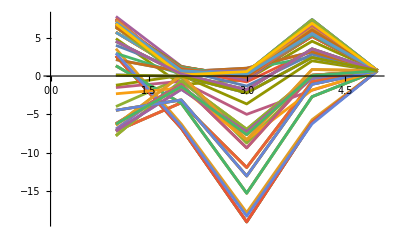

```mathematica
ListPlot[Minphi,Joined->True]
```

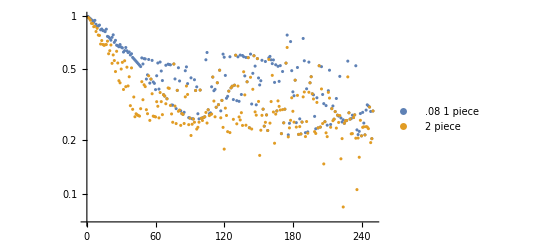

```mathematica
ListLogPlot[{SqueezeTableduration/2.5,SqueezeTableduration2/2.5},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

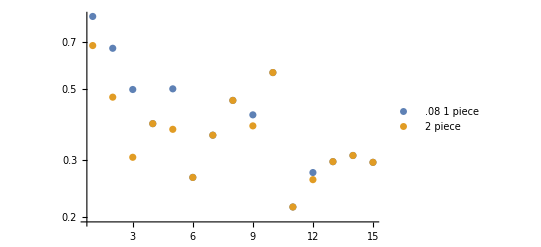

```mathematica
ListLogPlot[{SqueezeTableduration/2.5,SqueezeTableduration2/2.5},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

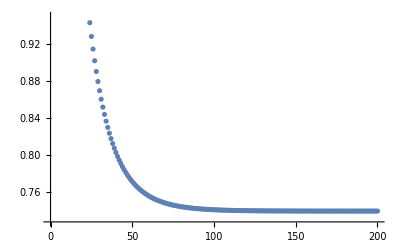

```mathematica
ListPlot[SqueezeTable]
```

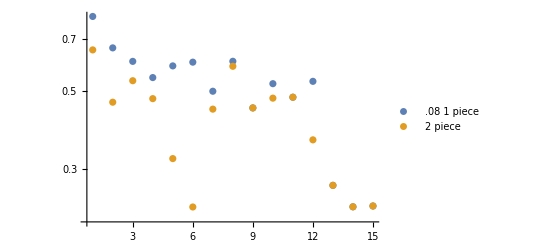

```mathematica
ListLogPlot[{SqueezeTableduration/2.5,SqueezeTableduration2/2.5},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

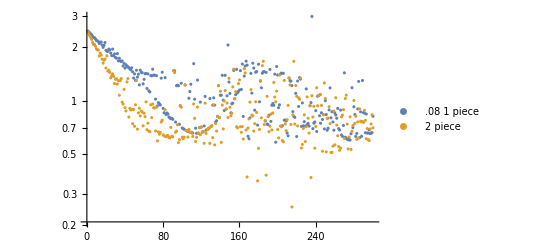

```mathematica
ListLogPlot[{SqueezeTableduration,SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

```mathematica
SqueezeTableduration
```

{2.47063,2.44096,2.41114,2.38005,2.35185,2.3048,2.27224,2.26613,2.23218,2.18359,2.17822,2.15782,2.10273,2.13379,2.14323,2.06051,1.99955,2.05291,2.12914,1.92492,1.90235,1.8995,1.95473,1.93515,1.85813,1.79855,1.95557,1.791,1.8366,1.75382,1.73764,1.84523,1.6787,1.73688,1.67762,1.66371,1.67668,1.57068,1.62431,1.52781,1.59636,1.56454,1.55421,1.53634,1.51641,1.49654,1.53405,1.45698,1.34304,1.41773,1.30417,1.48654,1.35956,1.41225,1.2293,1.48786,1.44665,1.43952,1.2465,1.32165,1.41975,1.42563,1.17421,1.41777,1.13916,1.12194,1.38706,1.38238,1.50654,1.39684,1.39339,1.02324,1.38637,0.936017,0.977179,0.962356,0.947809,1.34171,1.44872,0.905889,0.857187,1.35063,0.837672,0.854242,0.842129,0.810893,0.802628,0.794692,0.797045,0.786644,1.47801,1.47475,0.759897,1.21672,1.22326,1.21598,0.737855,0.938299,1.25617,0.703284,0.697126,0.691384,1.22854,0.681164,0.676697,0.672663,1.03457,1.12855,1.24066,0.660951,0.659149,1.61938,1.02183,0.701479,0.65656,1.30902,0.658084,0.706935,0.984289,0.711779,0.666886,0.6703,0.72174,1.05869,0.683484,0.688863,0.694737,0.701106,1.03024,0.715328,0.723181,0.94599,1.03995,0.945752,0.759516,0.772601,0.818213,1.2174,0.803635,1.074,1.07579,1.39197,1.00813,0.882056,1.39232,0.898888,1.06703,2.06088,1.27639,1.10056,0.855756,0.961798,0.970865,1.48263,1.02767,1.0828,1.50331,1.10801,1.13128,1.15118,1.47997,1.15906,1.61099,0.816914,1.37759,1.56944,1.67202,1.589,0.632061,0.61206,0.802071,1.42725,1.10591,1.62939,1.52908,0.885999,1.44845,1.46151,0.730042,1.60683,0.987611,1.29103,1.18436,1.43113,1.4578,1.45864,0.769621,1.44551,0.739982,0.733855,0.829208,1.50249,0.766487,0.945,0.966255,0.943992,1.41282,0.584831,1.55937,1.39829,0.914302,0.949973,1.41554,1.43234,0.724417,1.42787,0.778152,0.77963,0.770643,0.658722,0.635453,1.34221,1.29505,1.29183,1.21813,0.869653,0.816649,0.80743,1.10219,0.629858,1.29263,0.929305,1.35018,1.32539,0.717837,0.973002,0.723432,0.763511,0.720809,1.16699,0.734031,0.746589,0.721322,0.938737,0.977418,2.98489,0.697522,0.748155,0.76047,0.880368,0.672702,1.06092,1.07111,0.824463,0.747924,0.856776,0.785481,0.835091,0.695075,1.00194,0.837749,0.683054,0.701335,0.889066,1.18238,0.802457,0.868273,0.760684,0.683489,0.854592,0.832028,0.797751,0.906509,0.697607,0.684976,0.886436,0.642989,0.630867,0.72666,1.43725,0.62372,0.614582,0.609308,0.602894,0.605763,0.60089,0.652731,1.18552,0.706438,0.925873,0.838392,0.630478,0.655757,0.900538,1.28616,0.620634,0.86702,0.632024,1.30161,0.85849,0.854047,0.661533,0.842632,0.658623,0.659095,0.686924,0.65485,0.658595,0.661899,0.818926}

```mathematica
SqueezeTableduration2
```

{2.44112,2.38275,2.32751,2.27334,2.21628,2.13065,2.07383,2.07994,2.02827,1.9626,1.9346,1.93329,1.7853,1.85634,1.81011,1.71689,1.6282,1.69287,1.71938,1.52918,1.79153,1.46881,1.48615,1.44553,1.34678,1.38638,1.41828,1.37201,1.25067,1.32144,1.331,1.24338,1.29946,1.07559,1.29925,1.3347,0.983,0.958428,1.16078,0.915302,0.876717,1.2781,1.33464,0.811151,0.907226,0.888781,0.894478,0.743879,0.893931,0.719151,0.950065,1.30216,0.693331,0.855998,0.907624,0.822439,0.875665,0.865129,0.723394,0.851543,0.814314,0.986689,0.68811,0.748835,0.675762,0.670772,0.949838,0.804627,0.958811,0.913133,0.913918,0.676391,0.919665,0.595172,0.669006,0.648377,0.663843,0.760259,0.777603,0.643855,0.63448,0.891149,0.628461,0.638623,0.637247,0.621223,0.619228,0.708589,0.631906,0.627277,1.47801,1.44332,0.665333,0.674946,0.733612,0.581573,0.605255,0.938299,0.920278,0.623788,0.61182,0.62385,1.22854,0.681164,0.676697,0.625478,0.690868,0.66482,0.66712,0.660951,0.630094,0.960563,0.79705,0.590252,0.623731,0.921588,0.658084,0.706935,0.644698,0.711779,0.666886,0.6703,0.576595,0.970236,0.655388,0.688863,0.694737,0.701106,0.576328,0.715328,0.723181,0.62081,0.948039,0.564864,0.744422,0.676371,0.817253,1.2174,0.803635,1.13229,0.583574,0.947404,0.695032,0.99743,1.14261,0.898888,0.971154,0.80546,1.33873,0.919343,0.823102,0.850695,1.1986,1.50836,1.02767,1.12674,0.714421,0.704434,1.24983,1.3116,0.715181,0.664797,0.715863,0.609549,1.51546,1.43421,0.684376,0.372856,0.703207,0.790714,0.983241,1.15712,0.831756,0.822793,0.676033,0.743393,0.987529,0.860378,0.354348,0.54013,0.689857,1.29985,0.802561,1.5781,1.66914,0.735527,0.77599,0.381583,1.05962,0.814604,0.670558,0.719883,0.842704,0.686167,0.854167,1.26882,1.05086,0.986917,1.13442,0.689237,0.618792,1.3972,0.721464,0.715336,0.5979,0.588377,1.30219,0.741376,0.679465,0.782503,0.943276,1.34506,1.22931,0.736395,0.252656,0.833473,1.66867,0.739872,1.21996,1.06083,0.722126,1.0418,1.02068,1.34272,0.542085,0.568805,0.699216,0.834243,0.590009,0.71523,1.05254,0.798144,0.658365,0.938737,0.369902,1.06845,0.810452,0.931033,0.541511,0.71751,1.18465,0.938349,1.07111,1.07909,1.08525,0.942421,0.519919,0.835115,1.26019,1.03014,0.516072,0.795935,0.8003,0.926981,0.745388,0.512164,0.512813,0.555517,0.874907,0.565554,1.0414,0.73019,0.636356,0.553098,0.526938,0.542336,0.812361,0.831076,0.8917,0.613297,1.03105,1.07553,0.739012,0.536156,0.626073,0.812311,0.532489,0.673641,0.7278,1.00448,0.746447,0.81784,0.607302,0.760988,0.61709,0.902135,0.767914,0.762001,0.765593,0.756301,0.882976,0.776439,0.61102,0.698436,0.604789,0.59733,0.694539,0.741043,0.835607,0.705434}

```mathematica
ϕTable
```

{{0.0125163,3.09709,1.64862,0.658571,0.121652},{-0.39421,2.1114,1.0701,0.828974,0.121652},{0.132986,2.54022,1.11676,1.03233,0.121652},{0.278032,2.48334,1.33897,1.13812,0.121652},{0.569464,2.3191,1.40963,1.30421,0.121652},{0.65706,2.28483,1.41216,1.26066,0.121652},{0.580227,2.2946,1.40855,1.1198,0.121652},{0.835277,2.27016,1.53677,1.18467,0.121652},{-0.066789,2.17258,0.744244,0.444034,0.121652},{0.548777,2.57306,0.725346,0.218541,0.121652},{-0.681939,2.25349,1.00576,-0.12094,0.121652},{1.00441,2.80364,0.737507,-0.0541025,0.121652},{-3.62435,1.97075,2.72089,-0.0539038,0.121652},{-2.88935,1.36843,1.98429,-0.170385,0.121652},{-5.35692,0.500144,0.899138,1.29735,0.121652},{-6.65413,0.19261,0.678391,0.60215,0.121652},{-6.79859,0.0939525,0.918945,0.971548,0.121652},{-6.52137,0.0734646,1.03864,0.789688,0.121652},{-6.77524,0.0434725,1.15128,0.992898,0.121652},{-6.52962,0.0158874,1.14971,0.745418,0.121652},{-6.78512,-0.0191805,1.22056,0.943017,0.121652},{-6.60029,-0.0409354,1.19865,0.722459,0.121652},{-6.81116,-0.0816086,1.24386,0.892154,0.121652},{-6.65622,-0.0858963,1.2333,0.686032,0.121652},{-6.84265,-0.132288,1.26607,0.847207,0.121652},{-6.70319,-0.123561,1.26307,0.643552,0.121652},{-6.87677,-0.1774,1.28783,0.809347,0.121652},{-6.74288,-0.155685,1.28964,0.596697,0.121652},{-6.91165,-0.219702,1.30829,0.779831,0.121652},{-6.77447,-0.1818,1.31328,0.545566,0.121652},{-6.94406,-0.259983,1.32644,0.76047,0.121652},{-6.79512,-0.200404,1.33365,0.491621,0.121652},{-6.96799,-0.297031,1.34105,0.75216,0.121652},{-6.80192,-0.21067,1.35002,0.44226,0.121652},{-6.97691,-0.326308,1.35119,0.751463,0.121652},{-6.79866,-0.215199,1.36143,0.413209,0.121652},{-6.97436,-0.341875,1.35698,0.751266,0.121652},{-6.79699,-0.218356,1.36725,0.409255,0.121652},{-6.97341,-0.345952,1.35923,0.74973,0.121652},{-6.79899,-0.220147,1.36911,0.409907,0.121652},{-6.9749,-0.347506,1.3598,0.74903,0.121652},{-6.79975,-0.220491,1.36984,0.407274,0.121652},{-6.9751,-0.349069,1.36016,0.749123,0.121652},{-6.79933,-0.220601,1.37035,0.406044,0.121652},{-6.97472,-0.349627,1.3604,0.749095,0.121652},{-6.79933,-0.220779,1.37056,0.40638,0.121652},{-6.97478,-0.349629,1.36045,0.748983,0.121652},{-6.7995,-0.220839,1.37059,0.406374,0.121652},{-6.9749,-0.349712,1.36046,0.748976,0.121652},{-6.79949,-0.220829,1.37062,0.406155,0.121652},{-6.97486,-0.349798,1.36048,0.748994,0.121652},{-6.79945,-0.220837,1.37064,0.406152,0.121652},{-6.97484,-0.3498,1.36049,0.748985,0.121652},{-6.79947,-0.220848,1.37065,0.406194,0.121652},{-6.97486,-0.349793,1.36049,0.748979,0.121652},{-6.79948,-0.220848,1.37065,0.406176,0.121652},{-6.97486,-0.349802,1.36049,0.748981,0.121652},{-6.79947,-0.220847,1.37065,0.406164,0.121652},{-6.97485,-0.349806,1.36049,0.748982,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406171,0.121652},{-6.97486,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349804,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652},{-6.97485,-0.349805,1.36049,0.748981,0.121652},{-6.79947,-0.220848,1.37065,0.406169,0.121652}}

```mathematica
ϕTableExtraPiece
```

{{{2.18302,1.5268,0.046013,1.63828,1.56239},{1.96939,1.52,-0.0776325,1.08397,1.56239},{2.65552,1.98849,0.249635,1.06959,1.56239},{2.58653,1.32761,-0.394691,0.504404,1.56239},{2.81846,1.6471,-0.221597,0.482089,1.56239},{2.45386,1.81153,0.0155455,0.480776,1.56239},{2.18269,1.60427,-0.148326,0.429639,1.56239},{2.92721,2.05192,0.270815,0.604069,1.56239},{6.81381,0.657879,-1.06923,0.9474,1.56239},{6.26717,0.765595,-0.807358,0.822035,1.56239},{6.4121,0.827118,-0.661731,0.678415,1.56239},{6.34954,0.852589,-0.562878,0.504194,1.56239},{6.37676,0.884426,-0.469123,0.36955,1.56239},{6.38655,0.908517,-0.385977,0.262493,1.56239},{6.39634,0.924472,-0.318413,0.183771,1.56239},{6.4028,0.932568,-0.266974,0.129882,1.56239},{6.40652,0.934525,-0.22995,0.0955857,1.56239},{6.40849,0.932368,-0.20422,0.0751562,1.56239},{6.40959,0.927817,-0.186541,0.063646,1.56239},{6.41031,0.922092,-0.174269,0.0574602,1.56239},{6.41086,0.915961,-0.165534,0.0542804,1.56239},{6.41131,0.909866,-0.159112,0.0527235,1.56239},{6.41168,0.90404,-0.154229,0.0520057,1.56239},{6.41199,0.898595,-0.1504,0.0517002,1.56239},{6.41224,0.893572,-0.147318,0.0515822,1.56239},{6.41245,0.888976,-0.144785,0.0515382,1.56239},{6.41261,0.884791,-0.142668,0.0515139,1.56239},{6.41275,0.880992,-0.140876,0.0514859,1.56239},{6.41285,0.87755,-0.139344,0.051446,1.56239},{6.41294,0.874436,-0.138024,0.0513934,1.56239},{6.41301,0.871621,-0.136878,0.05133,1.56239},{6.41307,0.869077,-0.135879,0.0512591,1.56239},{6.41311,0.866779,-0.135004,0.0511834,1.56239},{6.41315,0.864704,-0.134235,0.0511057,1.56239},{6.41318,0.86283,-0.133556,0.051028,1.56239},{6.41321,0.861139,-0.132955,0.0509519,1.56239},{6.41323,0.859612,-0.132423,0.0508784,1.56239},{6.41325,0.858233,-0.131949,0.0508084,1.56239},{6.41326,0.856989,-0.131527,0.0507423,1.56239},{6.41328,0.855866,-0.131151,0.0506803,1.56239},{6.41329,0.854852,-0.130815,0.0506226,1.56239},{6.4133,0.853936,-0.130514,0.0505691,1.56239},{6.41331,0.85311,-0.130245,0.0505197,1.56239},{6.41332,0.852364,-0.130004,0.0504743,1.56239},{6.41332,0.851691,-0.129787,0.0504326,1.56239},{6.41333,0.851083,-0.129593,0.0503944,1.56239},{6.41333,0.850534,-0.129418,0.0503596,1.56239},{6.41334,0.850038,-0.129261,0.0503278,1.56239},{6.41334,0.84959,-0.129119,0.0502988,1.56239},{6.41335,0.849186,-0.128992,0.0502725,1.56239},{6.41335,0.848822,-0.128878,0.0502486,1.56239},{6.41335,0.848492,-0.128774,0.0502269,1.56239},{6.41335,0.848195,-0.128682,0.0502071,1.56239},{6.41336,0.847926,-0.128598,0.0501892,1.56239},{6.41336,0.847683,-0.128522,0.050173,1.56239},{6.41336,0.847464,-0.128454,0.0501583,1.56239},{6.41336,0.847266,-0.128393,0.050145,1.56239},{6.41336,0.847088,-0.128337,0.0501329,1.56239},{6.41337,0.846927,-0.128287,0.050122,1.56239},{6.41337,0.846781,-0.128242,0.0501122,1.56239},{6.41337,0.846649,-0.128202,0.0501032,1.56239},{6.41337,0.84653,-0.128165,0.0500952,1.56239},{6.41337,0.846423,-0.128132,0.0500879,1.56239},{6.41337,0.846326,-0.128102,0.0500812,1.56239},{6.41337,0.846239,-0.128075,0.0500753,1.56239},{6.41337,0.846159,-0.128051,0.0500699,1.56239},{6.41337,0.846088,-0.128029,0.050065,1.56239},{6.41337,0.846024,-0.128009,0.0500606,1.56239},{6.41337,0.845965,-0.127991,0.0500566,1.56239},{6.41337,0.845913,-0.127975,0.0500531,1.56239},{6.41337,0.845865,-0.12796,0.0500498,1.56239},{6.41337,0.845822,-0.127947,0.0500469,1.56239},{6.41337,0.845784,-0.127935,0.0500442,1.56239},{6.41337,0.845749,-0.127924,0.0500418,1.56239},{6.41337,0.845717,-0.127914,0.0500397,1.56239},{6.41338,0.845688,-0.127906,0.0500377,1.56239},{6.41338,0.845663,-0.127898,0.0500359,1.56239},{6.41338,0.845639,-0.127891,0.0500343,1.56239},{6.41338,0.845618,-0.127884,0.0500328,1.56239},{6.41338,0.845599,-0.127878,0.0500315,1.56239},{6.41338,0.845582,-0.127873,0.0500303,1.56239},{6.41338,0.845567,-0.127868,0.0500293,1.56239},{6.41338,0.845553,-0.127864,0.0500283,1.56239},{6.41338,0.84554,-0.12786,0.0500275,1.56239},{6.41338,0.845529,-0.127856,0.0500267,1.56239},{6.41338,0.845518,-0.127853,0.050026,1.56239},{6.41338,0.845509,-0.12785,0.0500253,1.56239},{6.41338,0.8455,-0.127848,0.0500247,1.56239},{6.41338,0.845493,-0.127846,0.0500242,1.56239},{6.41338,0.845486,-0.127843,0.0500237,1.56239},{6.41338,0.84548,-0.127842,0.0500232,1.56239},{6.41338,0.845474,-0.12784,0.0500229,1.56239},{6.41338,0.845469,-0.127838,0.0500225,1.56239},{6.41338,0.845465,-0.127837,0.0500222,1.56239},{6.41338,0.845461,-0.127836,0.0500219,1.56239},{6.41338,0.845457,-0.127834,0.0500217,1.56239},{6.41338,0.845453,-0.127833,0.0500215,1.56239},{6.41338,0.84545,-0.127832,0.0500213,1.56239},{6.41338,0.845448,-0.127832,0.0500211,1.56239},{6.41338,0.845445,-0.127831,0.050021,1.56239},{6.41338,0.845443,-0.12783,0.0500208,1.56239},{6.41338,0.845441,-0.127829,0.0500207,1.56239},{6.41338,0.845439,-0.127829,0.0500205,1.56239},{6.41338,0.845437,-0.127828,0.0500204,1.56239},{6.41338,0.845436,-0.127828,0.0500203,1.56239},{6.41338,0.845435,-0.127828,0.0500202,1.56239},{6.41338,0.845433,-0.127827,0.0500202,1.56239},{6.41338,0.845432,-0.127827,0.0500201,1.56239},{6.41338,0.845431,-0.127827,0.05002,1.56239},{6.41338,0.84543,-0.127826,0.0500199,1.56239},{6.41338,0.84543,-0.127826,0.0500199,1.56239},{6.41338,0.845429,-0.127826,0.0500198,1.56239},{6.41338,0.845428,-0.127826,0.0500198,1.56239},{6.41338,0.845428,-0.127825,0.0500197,1.56239},{6.41338,0.845427,-0.127825,0.0500197,1.56239},{6.41338,0.845427,-0.127825,0.0500196,1.56239},{6.41338,0.845426,-0.127825,0.0500196,1.56239},{6.41338,0.845426,-0.127825,0.0500195,1.56239},{6.41338,0.845425,-0.127825,0.0500195,1.56239},{6.41338,0.845425,-0.127825,0.0500195,1.56239},{6.41338,0.845425,-0.127825,0.0500195,1.56239},{6.41338,0.845425,-0.127824,0.0500195,1.56239},{6.41338,0.845424,-0.127824,0.0500195,1.56239},{6.41338,0.845424,-0.127824,0.0500195,1.56239},{6.41338,0.845424,-0.127824,0.0500195,1.56239},{6.41338,0.845424,-0.127824,0.0500195,1.56239},{6.41338,0.845424,-0.127824,0.0500195,1.56239},{6.41338,0.845423,-0.127824,0.0500195,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845423,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500194,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239},{6.41338,0.845422,-0.127824,0.0500193,1.56239}}}

## Phase Control with pieces grd U3H2U2U1 beta=1

```mathematica
Clear["Global`*"];


Ix3half2=({{0, (√3)/2, 0, 0}, {(√3)/2, 0, 1, 0}, {0, 1, 0, (√3)/2}, {0, 0, (√3)/2, 0}});
Iy3half2=({{0, -(ⅈ √3)/2, 0, 0}, {(ⅈ √3)/2, 0, -ⅈ, 0}, {0, ⅈ, 0, -(ⅈ √3)/2}, {0, 0, (ⅈ √3)/2, 0}});
Iz3half2=({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}});
Hmuti[ϕ1_,ϕ2_,ϕ3_]:=({{0, (√3)/2 ⅇ^(-ⅈ ϕ1), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ1), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;
(*UHmuti[ϕ1_,ϕ2_,ϕ3_,t_]:=MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3]*t]*)
UHmuti[ϕ1_,ϕ2_,ϕ3_,t_]:=({{Cos[t/2]^3, √3 Cos[t/2]^2 Sin[t/2] (-ⅈ Cos[ϕ1]-Sin[ϕ1]), -√3 Cos[t/2] Sin[t/2]^2 (Cos[ϕ1+ϕ2]-ⅈ Sin[ϕ1+ϕ2]), Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]-Sin[ϕ1+ϕ2+ϕ3])}, {√3 Cos[t/2]^2 Sin[t/2] (-ⅈ Cos[ϕ1]+Sin[ϕ1]), 1/4 (Cos[t/2]+3 Cos[(3 t)/2]), 1/4 (Sin[t/2]-3 Sin[(3 t)/2]) (ⅈ Cos[ϕ2]+Sin[ϕ2]), √3 Cos[t/2] Sin[t/2]^2 (Cos[ϕ2+ϕ3]-ⅈ Sin[ϕ2+ϕ3])}, {-√3 Cos[t/2] Sin[t/2]^2 (Cos[ϕ1+ϕ2]+ⅈ Sin[ϕ1+ϕ2]), 1/4 ⅈ ⅇ^(ⅈ ϕ2) (Sin[t/2]-3 Sin[(3 t)/2]), 1/4 (Cos[t/2]+3 Cos[(3 t)/2]), √3 Cos[t/2]^2 Sin[t/2] (ⅈ Cos[ϕ3]+Sin[ϕ3])}, {Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]+Sin[ϕ1+ϕ2+ϕ3]), √3 Cos[t/2] Sin[t/2]^2 (Cos[ϕ2+ϕ3]+ⅈ Sin[ϕ2+ϕ3]), 1/4 ⅈ √3 ⅇ^(ⅈ ϕ3) Csc[t/2] Sin[t]^2, Cos[t/2]^3}})
IniPhi={{1},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^3},{1/4 √3 ⅇ^(ⅈ ϕ) Csc[θ/2] Sin[θ]^2},{1/2 √3 ⅇ^(2 ⅈ ϕ) Sin[θ/2] Sin[θ]},{ⅇ^(3 ⅈ ϕ) Sin[θ/2]^3}}

(*StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:=UHmuti[ϕ1,ϕ2,ϕ3,t].StateθϕInitial[θ,ϕ]*)
(*StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,Pi/2,Pi/2]:={{(Sin[t/2]^3 (-4 Cos[ϕ1+ϕ2+ϕ3]+4 Cot[t/2] (3 Cos[ϕ1+ϕ2]+Cot[t/2] (3 Cos[ϕ1]+Cot[t/2]-3 ⅈ Sin[ϕ1])-3 ⅈ Sin[ϕ1+ϕ2])+4 ⅈ Sin[ϕ1+ϕ2+ϕ3]))/(8 √2)},{1/8 ⅈ √(3/2) ⅇ^(-ⅈ ϕ2) (2 Cos[t/2] ((-1+Cos[t]) Cos[ϕ3]-ⅇ^(ⅈ ϕ2) (1-3 Cos[t]+ⅇ^(ⅈ ϕ1) Sin[t]))+3 Sin[(3 t)/2]+Sin[t/2] (-1+2 ⅈ Sin[t] Sin[ϕ3]))},{-1/8 √(3/2) (Cos[t/2]+3 Cos[(3 t)/2]-ⅇ^(-ⅈ ϕ3) Csc[t/2] Sin[t]^2+2 ⅇ^(ⅈ ϕ2) Sin[t/2] (-1-3 Cos[t]+ⅇ^(ⅈ ϕ1) Sin[t]))},{(Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]-ⅈ Cot[t/2] (-3 Cos[ϕ2+ϕ3]+3 ⅇ^(ⅈ ϕ3) Cot[t/2]+Cot[t/2]^2-3 ⅈ Sin[ϕ2+ϕ3])+Sin[ϕ1+ϕ2+ϕ3]))/(2 √2)}}*)
StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:={{Cos[t/2]^3 Cos[θ/2]^3-3/16 ⅈ ⅇ^(ⅈ (ϕ-ϕ1)) Csc[t/2] Csc[θ/2] Sin[t]^2 Sin[θ]^2-3/2 ⅇ^(2 ⅈ ϕ) Cos[t/2] Sin[t/2]^2 Sin[θ/2] Sin[θ] (Cos[ϕ1+ϕ2]-ⅈ Sin[ϕ1+ϕ2])+ⅇ^(3 ⅈ ϕ) Sin[t/2]^3 Sin[θ/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]-Sin[ϕ1+ϕ2+ϕ3])},{1/4 √3 Sin[θ/2]^3 (ⅇ^(ⅈ ϕ) Cos[t/2] Cot[θ/2]^2+3 ⅇ^(ⅈ ϕ) Cos[(3 t)/2] Cot[θ/2]^2+2 ⅇ^(2 ⅈ ϕ-ⅈ ϕ2) Sin[t/2] (-ⅈ (1+3 Cos[t]) Cot[θ/2]+ⅇ^(ⅈ (ϕ-ϕ3)) Sin[t])+4 Cos[t/2]^2 Cot[θ/2]^3 Sin[t/2] (-ⅈ Cos[ϕ1]+Sin[ϕ1]))},{1/4 √3 (1/4 ⅈ ⅇ^(ⅈ (ϕ+ϕ2)) Csc[θ/2] (Sin[t/2]-3 Sin[(3 t)/2]) Sin[θ]^2+Cos[t/2] (ⅇ^(2 ⅈ ϕ) (-1+3 Cos[t]) Sin[θ/2] Sin[θ]-4 Cos[θ/2]^3 Sin[t/2]^2 (Cos[ϕ1+ϕ2]+ⅈ Sin[ϕ1+ϕ2])+2 ⅇ^(3 ⅈ ϕ) Sin[t] Sin[θ/2]^3 (ⅈ Cos[ϕ3]+Sin[ϕ3])))},{ⅇ^(3 ⅈ ϕ) Cos[t/2]^3 Sin[θ/2]^3+3/8 ⅈ ⅇ^(ⅈ (2 ϕ+ϕ3)) Csc[t/2] Sin[t]^2 Sin[θ/2] Sin[θ]+3 Cos[t/2] Cos[θ/2]^2 Sin[t/2]^2 Sin[θ/2] (Cos[ϕ+ϕ2+ϕ3]+ⅈ Sin[ϕ+ϕ2+ϕ3])+Cos[θ/2]^3 Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]+Sin[ϕ1+ϕ2+ϕ3])}}
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]
Gradientϕ1[ϕ1_]:=({{0, (-ⅈ √3)/2 ⅇ^(-ⅈ ϕ1), 0, 0}, {(ⅈ √3)/2 ⅇ^(ⅈ ϕ1), 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
Gradientϕ2[ϕ2_]:=({{0, 0, 0, 0}, {0, 0, -ⅈ*ⅇ^(-ⅈ ϕ2), 0}, {0, ⅈ*ⅇ^(ⅈ ϕ2), 0, 0}, {0, 0, 0, 0}})
Gradientϕ3[ϕ3_]:=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, (-ⅈ √3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (ⅈ √3)/2 ⅇ^(ⅈ ϕ3), 0}})
```

```mathematica
UHmuti[ϕ1,ϕ2,ϕ3,t].{{a},{b},{c},{d}}//MatrixForm//FullSimplify
```

(a Cos[t/2]^3+√3 b Cos[t/2]^2 Sin[t/2] (-ⅈ Cos[ϕ1]-Sin[ϕ1])-√3 c Cos[t/2] Sin[t/2]^2 (Cos[ϕ1+ϕ2]-ⅈ Sin[ϕ1+ϕ2])+d Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]-Sin[ϕ1+ϕ2+ϕ3])
1/4 (3 b Cos[(3 t)/2]+4 √3 a Cos[t/2]^2 Sin[t/2] (-ⅈ Cos[ϕ1]+Sin[ϕ1])+c (Sin[t/2]-3 Sin[(3 t)/2]) (ⅈ Cos[ϕ2]+Sin[ϕ2])+Cos[t/2] (b+4 √3 d Sin[t/2]^2 (Cos[ϕ2+ϕ3]-ⅈ Sin[ϕ2+ϕ3])))
1/4 (3 c Cos[(3 t)/2]+ⅈ b ⅇ^(ⅈ ϕ2) (Sin[t/2]-3 Sin[(3 t)/2])+Cos[t/2] (c+2 √3 (-2 a Sin[t/2]^2 (Cos[ϕ1+ϕ2]+ⅈ Sin[ϕ1+ϕ2])+d Sin[t] (ⅈ Cos[ϕ3]+Sin[ϕ3]))))
d Cos[t/2]^3+1/4 ⅈ √3 c ⅇ^(ⅈ ϕ3) Csc[t/2] Sin[t]^2+√3 b Cos[t/2] Sin[t/2]^2 (Cos[ϕ2+ϕ3]+ⅈ Sin[ϕ2+ϕ3])+a Sin[t/2]^3 (-ⅈ Cos[ϕ1+ϕ2+ϕ3]+Sin[ϕ1+ϕ2+ϕ3]))

```mathematica
(*StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:=UHmuti[ϕ1,ϕ2,ϕ3,t].StateθϕInitial[θ,ϕ]*)
```

```mathematica
phi1=Pi/4;
phi2=Pi/4;

ϕ1gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1-10^-8,ϕ2,ϕ3,t,phi1,phi2]]]])/10^-8
ϕ2gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2-10^-8,ϕ3,t,phi1,phi2]]]])/10^-8
ϕ3gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3-10^-8,t,phi1,phi2]]]])/10^-8

ϕ1graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,t].state]]])/10^-8
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

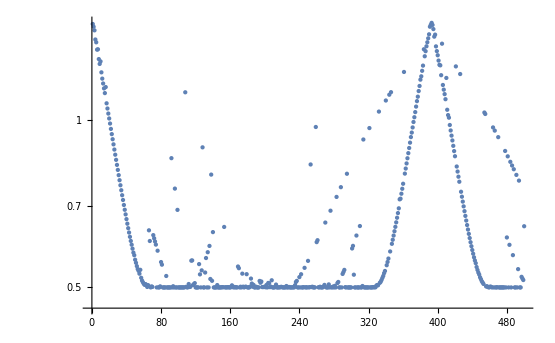

```mathematica
durationnumber=800;
SqueezeTableduration=Table[0,{i,1,durationnumber}];
SqueezeTableduration2=Table[0,{i,1,durationnumber}];
Do[
Print[k];
totT=Pi/2*k/durationnumber;
itenumber=800;
ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];
SqueezeTable=Table[0,{i,1,itenumber}];

SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],totT,phi1,phi2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.9*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i,2]]=ϕTable[[i-1,2]]-0.9*ϕ2gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i,3]]=ϕTable[[i-1,3]]-0.9*ϕ3gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],totT,phi1,phi2]]]];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];

SqueezeTableduration[[k]]=Min[SqueezeTable];



ExtraPiece=1;
ϕTableExtraPiece=Table[Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}],{j,1,ExtraPiece}];
StateExtraPiece=Table[0,{j,1,ExtraPiece+1}];
StateExtraPiece[[1]]=UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],totT].StateθϕInitial[phi1,phi2];
SqueezeTableExtraPiece=Table[Table[0,{i,1,itenumber}],{j,1,ExtraPiece}];
SqueezeTableExtraPiece[[1,1]]=ξSqure[StateExtraPiece[[1]]];
Do[

Do[ 
ϕTableExtraPiece[[j,i,1]]=ϕTableExtraPiece[[j,i-1,1]]-0.2*ϕ1graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,2]]=ϕTableExtraPiece[[j,i-1,2]]-0.2*ϕ2graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,3]]=ϕTableExtraPiece[[j,i-1,3]]-0.2*ϕ3graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];
SqueezeTableExtraPiece[[j,i]]=ξSqure[Chop[N[UHmuti[ϕTableExtraPiece[[j,i,1]],ϕTableExtraPiece[[j,i,2]],ϕTableExtraPiece[[j,i,3]],totT].StateExtraPiece[[j]]]]];


,{i,2,itenumber}];
StateExtraPiece[[j+1]]=UHmuti[Last[ϕTableExtraPiece[[j]]][[1]],Last[ϕTableExtraPiece[[j]]][[2]],Last[ϕTableExtraPiece[[j]]][[3]],totT].StateExtraPiece[[j]];

,{j,1,ExtraPiece}];


SqueezeTableduration[[k]]=Min[SqueezeTable];
SqueezeTableduration2[[k]]=Min[SqueezeTableExtraPiece[[1]]];


,{k,1,durationnumber}]
```

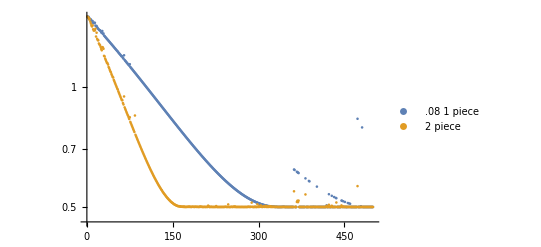

```mathematica
ListLogPlot[{SqueezeTableduration,SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

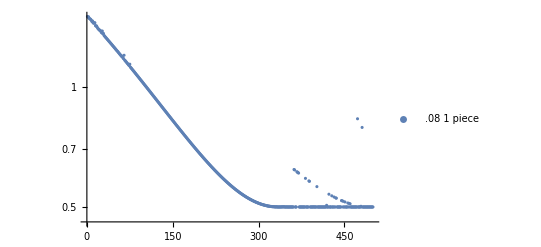

```mathematica
ListLogPlot[{SqueezeTableduration},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

```mathematica
SqueezeTableduration
```

{1.49681,1.4901,1.49368,1.48151,1.47661,1.47491,1.47011,1.46172,1.45242,1.45801,1.44287,1.43906,1.4437,1.44319,1.42027,1.41521,1.41742,1.40709,1.39859,1.39342,1.38814,1.38285,1.38259,1.37674,1.36722,1.3621,1.3765,1.35388,1.35732,1.34155,1.3367,1.33126,1.32615,1.32106,1.31604,1.31093,1.30588,1.30091,1.29583,1.29081,1.28583,1.28083,1.27585,1.27116,1.26593,1.26117,1.25607,1.25123,1.24625,1.24136,1.23649,1.23162,1.22678,1.2233,1.2171,1.21229,1.20749,1.2027,1.19792,1.19316,1.18841,1.19048,1.17895,1.17424,1.19715,1.16485,1.16018,1.15561,1.15088,1.14625,1.14163,1.13703,1.13243,1.12786,1.13731,1.11874,1.1142,1.10968,1.10517,1.10067,1.09619,1.09172,1.08727,1.08283,1.0784,1.07399,1.06959,1.06521,1.06084,1.05648,1.05214,1.04781,1.0435,1.0392,1.03491,1.03064,1.0264,1.02215,1.01792,1.01371,1.00951,1.00533,1.00116,0.997011,0.992873,0.98875,0.984642,0.980579,0.976471,0.972408,0.96836,0.964327,0.960309,0.956307,0.95232,0.948348,0.944391,0.94045,0.936524,0.932613,0.928718,0.924839,0.920975,0.917126,0.913294,0.909476,0.905675,0.901889,0.898119,0.894365,0.890627,0.886905,0.883198,0.879507,0.875835,0.872174,0.868532,0.864906,0.861296,0.857702,0.854124,0.850562,0.847017,0.843488,0.839975,0.836479,0.832999,0.829536,0.826089,0.822659,0.819245,0.815848,0.812467,0.809103,0.805756,0.802426,0.799112,0.795815,0.792535,0.789271,0.786025,0.782796,0.779583,0.776387,0.773209,0.770047,0.766903,0.763776,0.760665,0.757572,0.754497,0.751438,0.748397,0.745373,0.742366,0.739376,0.736404,0.73345,0.730513,0.727593,0.724691,0.721806,0.718939,0.716089,0.713257,0.710443,0.707646,0.704867,0.702106,0.699362,0.696637,0.693929,0.691239,0.688566,0.685912,0.683275,0.680657,0.678056,0.675474,0.672909,0.670363,0.667834,0.665324,0.662831,0.660357,0.657901,0.655463,0.653043,0.650642,0.648259,0.645894,0.643547,0.641219,0.638909,0.636618,0.634344,0.63209,0.629853,0.627635,0.625436,0.623255,0.621093,0.618949,0.616824,0.614717,0.612629,0.61056,0.608509,0.606477,0.604463,0.602468,0.600492,0.598535,0.596597,0.594677,0.592776,0.590894,0.589031,0.587186,0.585361,0.583554,0.581767,0.579998,0.578248,0.576517,0.574806,0.573113,0.571439,0.569784,0.568148,0.566532,0.564934,0.563356,0.561796,0.560256,0.558735,0.557233,0.55575,0.554287,0.552842,0.551417,0.550011,0.548624,0.547257,0.545909,0.54458,0.54327,0.54198,0.540709,0.539458,0.538226,0.537013,0.535819,0.534645,0.53349,0.532355,0.531239,0.530143,0.529066,0.528008,0.52697,0.525952,0.524952,0.523972,0.523012,0.522077,0.521151,0.520249,0.519367,0.518512,0.517662,0.51684,0.516038,0.51525,0.514487,0.513741,0.513015,0.512408,0.511626,0.510958,0.510313,0.509704,0.509078,0.508495,0.507951,0.50737,0.506878,0.506335,0.505842,0.505432,0.504926,0.504684,0.504166,0.50371,0.503317,0.502981,0.502637,0.50232,0.502269,0.501883,0.50151,0.501585,0.501072,0.500956,0.500788,0.500638,0.500848,0.500302,0.500297,0.50011,0.500654,0.500124,0.500094,0.500066,0.500008,0.500027,0.500014,0.500215,0.500003,0.500003,0.500527,0.50018,0.500329,0.500559,0.500365,0.5,0.500001,0.5,0.500254,0.5,0.5,0.500001,0.5,0.5,0.500007,0.500087,0.500057,0.5,0.500073,0.5,0.500036,0.620382,0.61878,0.5,0.500013,0.5,0.612419,0.610842,0.609271,0.607707,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500001,0.5,0.589522,0.5,0.5,0.5,0.5,0.5,0.580896,0.579492,0.5,0.5,0.5,0.5,0.5,0.5,0.500324,0.5,0.5,0.5,0.5,0.5,0.562165,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.504826,0.5,0.5,0.5,0.538151,0.5,0.5,0.5,0.5,0.533215,0.5,0.5,0.5,0.529493,0.5,0.5,0.526836,0.525976,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.518834,0.518108,0.5,0.516695,0.5,0.5,0.514679,0.5,0.5,0.5,0.5,0.511596,0.5,0.51046,0.5,0.509381,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.830715,0.5,0.5,0.5,0.5,0.5,0.502016,0.5,0.790309,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500034,0.5,0.5,0.500004,0.5,0.5,0.5}

```mathematica
SqueezeTableduration2
```

{1.49607,1.48742,1.48724,1.47103,1.47354,1.45235,1.43649,1.42066,1.41272,1.42177,1.39045,1.37972,1.38597,1.3807,1.39452,1.33338,1.36308,1.31579,1.30579,1.30515,1.28136,1.27421,1.26825,1.25623,1.24184,1.23189,1.25464,1.25172,1.24263,1.19328,1.18907,1.17435,1.16502,1.15559,1.14641,1.14364,1.13494,1.11899,1.11156,1.1007,1.09178,1.08535,1.07402,1.06557,1.05654,1.05363,1.03921,1.03123,1.02215,1.01372,1.00534,0.997013,0.988763,0.982859,0.972409,0.964329,0.956381,0.948468,0.940453,0.932832,0.924847,0.924436,0.909478,0.901925,0.944548,0.887022,0.879543,0.872271,0.864908,0.857704,0.850565,0.845081,0.836487,0.829536,0.838056,0.815849,0.809104,0.802442,0.795816,0.789272,0.782796,0.776391,0.770048,0.84643,0.757572,0.751438,0.745378,0.739446,0.73345,0.727593,0.721809,0.716091,0.710443,0.704867,0.699369,0.69393,0.688573,0.68328,0.678057,0.672909,0.667834,0.662832,0.657902,0.653062,0.648259,0.643547,0.638911,0.634364,0.629854,0.625437,0.621093,0.616829,0.61263,0.608708,0.604464,0.600493,0.596597,0.592779,0.589032,0.585423,0.581767,0.578312,0.574975,0.571441,0.568149,0.564935,0.561845,0.558812,0.555751,0.552843,0.550691,0.547259,0.544581,0.541982,0.539459,0.537178,0.535213,0.532393,0.530341,0.528021,0.525997,0.524358,0.522101,0.520266,0.519099,0.516886,0.515299,0.513745,0.512309,0.511497,0.509712,0.508586,0.507448,0.506335,0.505808,0.504908,0.503688,0.50346,0.502362,0.50246,0.502387,0.50143,0.502051,0.50069,0.500979,0.500827,0.500414,0.501072,0.500073,0.50151,0.500021,0.500002,0.500407,0.500071,0.500239,0.500682,0.500074,0.500921,0.501178,0.500002,0.500822,0.500005,0.500135,0.500785,0.500497,0.500718,0.500095,0.500086,0.500883,0.500596,0.500003,0.500607,0.500547,0.5,0.500069,0.500471,0.500012,0.501557,0.500418,0.500332,0.500812,0.5,0.5,0.500081,0.50038,0.500182,0.5,0.5002,0.500216,0.500098,0.500188,0.503968,0.501947,0.5,0.500002,0.500003,0.50088,0.500005,0.5,0.500193,0.500093,0.5,0.500107,0.5001,0.500014,0.502649,0.500046,0.5,0.50002,0.5,0.500011,0.500012,0.500022,0.50005,0.5,0.500079,0.500061,0.5,0.500062,0.500142,0.50008,0.500626,0.500393,0.500002,0.500124,0.500005,0.507361,0.500009,0.5,0.500001,0.500008,0.500127,0.500763,0.500001,0.500026,0.500352,0.501177,0.5,0.501533,0.500002,0.500005,0.500095,0.500018,0.500124,0.500001,0.500125,0.5,0.5,0.500055,0.5,0.500156,0.5,0.50001,0.5,0.5,0.500018,0.500117,0.500002,0.5,0.5,0.500091,0.500876,0.500278,0.500082,0.500467,0.5,0.500542,0.512627,0.500385,0.500072,0.5,0.5,0.500008,0.501074,0.5,0.5,0.5,0.507709,0.5,0.500291,0.502619,0.500137,0.501316,0.504555,0.50061,0.5,0.500278,0.50043,0.502509,0.501721,0.500086,0.502813,0.503363,0.5,0.501653,0.5,0.501107,0.5,0.502269,0.501883,0.500002,0.501585,0.500047,0.5,0.500788,0.500013,0.500651,0.500122,0.500211,0.500052,0.500292,0.50006,0.500094,0.500022,0.500003,0.500006,0.500011,0.5,0.5,0.500003,0.500027,0.500017,0.500329,0.5,0.500365,0.5,0.5,0.5,0.500007,0.5,0.5,0.5,0.5,0.5,0.500004,0.500025,0.500027,0.5,0.500073,0.5,0.500036,0.547238,0.5,0.5,0.500005,0.5,0.514733,0.51837,0.514152,0.518654,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.537396,0.5,0.5,0.5,0.5,0.5,0.500001,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500324,0.5,0.5,0.5,0.5,0.5,0.500183,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.503212,0.5,0.5,0.5,0.506402,0.5,0.5,0.5,0.5,0.503539,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.513094,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.504503,0.500054,0.5,0.501447,0.5,0.5,0.500727,0.5,0.5,0.5,0.5,0.50005,0.5,0.500212,0.5,0.50007,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.56383,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500299,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500034,0.5,0.5,0.500004,0.5,0.5,0.5}

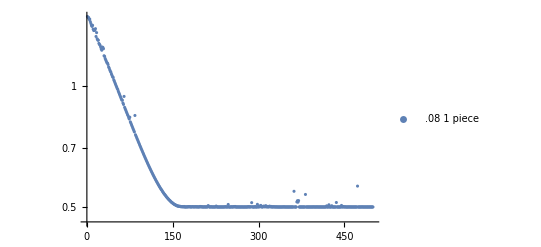

```mathematica
ListLogPlot[{SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

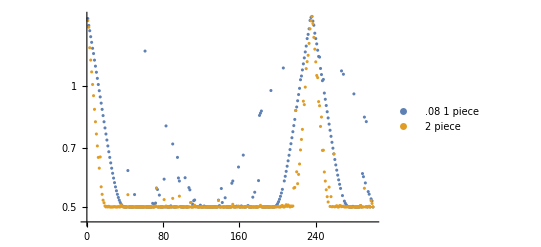

```mathematica
ListLogPlot[{SqueezeTableduration,SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

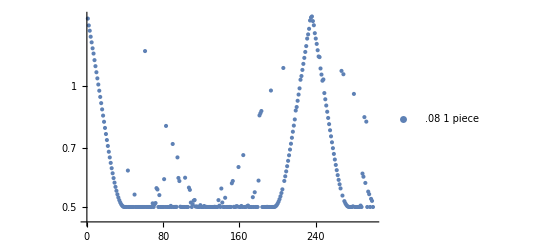

```mathematica
ListLogPlot[{SqueezeTableduration},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

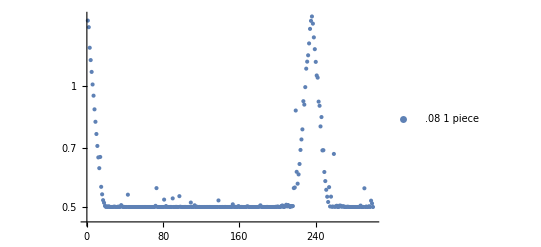

```mathematica
ListLogPlot[{SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

```mathematica
SqueezeTableduration
```

{1.46554,1.40929,1.36749,1.32158,1.27976,1.23684,1.20044,1.15611,1.11695,1.07893,1.0419,1.00592,0.971034,0.937168,0.904447,0.87286,0.842431,0.81318,0.785129,0.758297,0.732703,0.708367,0.685304,0.663531,0.643065,0.623919,0.606107,0.589641,0.574534,0.560796,0.548437,0.537468,0.527891,0.519717,0.512952,0.507618,0.503724,0.501182,0.500266,0.500013,0.5,0.5,0.615597,0.5,0.5,0.5,0.5,0.5,0.5,0.536724,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.21753,0.5,0.5,0.5,0.5,0.500011,0.5,0.5,0.510457,0.5,0.507575,0.511368,0.556832,0.552553,0.5,0.535085,0.5,0.5,0.5,0.5,0.586039,0.5,0.79416,0.5,0.5,0.5,0.5,0.503163,0.5,0.716414,0.5,0.500107,0.500188,0.500281,0.663603,0.590086,0.579809,0.50082,0.500024,0.5,0.500006,0.5,0.5909,0.5,0.5,0.5,0.558469,0.551339,0.512806,0.5,0.507496,0.518326,0.520331,0.501269,0.50117,0.500791,0.500018,0.500162,0.505254,0.5,0.500005,0.5,0.502798,0.500001,0.500414,0.500059,0.5,0.500005,0.500091,0.5,0.500009,0.5,0.5,0.500614,0.500001,0.500042,0.5,0.519968,0.503789,0.500002,0.55558,0.512907,0.500016,0.500005,0.527008,0.5,0.500039,0.5,0.5,0.500166,0.500002,0.572472,0.579906,0.500415,0.500086,0.500388,0.50244,0.501146,0.628085,0.500009,0.500001,0.502928,0.500048,0.672327,0.500002,0.5,0.500476,0.501775,0.50408,0.5,0.5,0.5,0.5,0.528759,0.5,0.543921,0.5,0.5,0.5,0.581302,0.843255,0.853973,0.864728,0.5,0.5,0.5,0.5,0.5,0.500335,0.5,0.5,0.5,0.972,0.500001,0.500018,0.50005,0.500474,0.502149,0.505081,0.509551,0.515381,0.522664,0.531373,0.541478,0.552978,1.10553,0.580122,0.595748,0.612727,0.631048,0.650699,0.671664,0.693929,0.717479,0.742296,0.768363,0.795661,0.824171,0.867162,0.884746,0.916766,0.949913,0.984162,1.03364,1.05587,1.09333,1.13177,1.17107,1.21149,1.25264,1.30744,1.33922,1.38249,1.44968,1.47486,1.48344,1.4447,1.41085,1.34834,1.30754,1.26837,1.22339,1.18063,1.17618,1.10242,1.06471,1.02808,1.0355,0.957996,0.924584,0.892291,0.861143,0.831159,0.802363,0.774773,0.74841,0.723293,0.699439,0.676865,0.655588,0.635622,0.616982,0.599681,0.583731,0.569144,0.55593,1.08727,0.533658,1.06671,0.516992,0.510773,0.506104,0.502615,0.500793,0.500113,0.500001,0.5,0.5,0.501831,0.953423,0.5,0.5,0.5,0.5,0.5,0.5,0.50403,0.5,0.605075,0.594331,0.835127,0.573577,0.81391,0.5,0.545906,0.537838,0.5,0.523719,0.517756,0.5}

```mathematica
SqueezeTableduration2
```

{1.44881,1.39518,1.24078,1.15644,1.08097,1.00615,0.943847,0.873003,0.813212,0.758406,0.708389,0.663541,0.624032,0.665291,0.560973,0.537515,0.519817,0.512152,0.502933,0.500139,0.501717,0.500026,0.501939,0.500114,0.500062,0.500059,0.500012,0.500538,0.501014,0.500171,0.500014,0.500024,0.501151,0.500041,0.500429,0.505359,0.501545,0.500062,0.500194,0.500013,0.5,0.5,0.536386,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.50007,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500006,0.503314,0.556832,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.521518,0.5,0.502635,0.5,0.5,0.5,0.5,0.500169,0.5,0.525167,0.5,0.5,0.500188,0.500281,0.500001,0.5,0.531861,0.50082,0.500023,0.5,0.5,0.5,0.50019,0.5,0.5,0.5,0.500095,0.5,0.512806,0.5,0.500067,0.5,0.504856,0.500001,0.501016,0.50004,0.500018,0.500162,0.5,0.5,0.5,0.5,0.5,0.500001,0.5,0.500059,0.5,0.5,0.500091,0.5,0.5,0.5,0.5,0.500003,0.500001,0.500012,0.5,0.519039,0.5,0.500002,0.5,0.500119,0.5,0.500005,0.500176,0.5,0.500039,0.5,0.5,0.500052,0.5,0.5,0.507691,0.500415,0.500055,0.500388,0.500001,0.50019,0.502541,0.500003,0.500001,0.500201,0.500048,0.5,0.500002,0.5,0.5,0.501775,0.501249,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.501308,0.504746,0.500215,0.5,0.5,0.5,0.5,0.5,0.500258,0.5,0.5,0.5,0.500001,0.500001,0.500018,0.50005,0.500002,0.50056,0.500126,0.501421,0.500323,0.500021,0.5,0.502919,0.504394,0.500279,0.500102,0.502538,0.506401,0.50166,0.505666,0.502674,0.500001,0.502879,0.501647,0.502687,0.556863,0.55883,0.867162,0.611164,0.571155,0.602214,0.639068,0.692436,0.735154,0.77869,0.91458,0.896811,0.990995,1.10127,1.14623,1.18848,1.27189,1.38199,1.44688,1.48344,1.42387,1.3165,1.23072,1.14469,1.0592,1.0462,0.912341,0.890997,0.791903,0.835386,0.690707,0.691383,0.610548,0.579692,0.551603,0.530197,0.514508,0.559958,0.501481,0.530383,0.500579,0.501192,0.676865,0.500305,0.501788,0.503508,0.5,0.500004,0.503884,0.503751,0.50081,0.501586,0.502266,0.500081,0.500482,0.50002,0.500688,0.500631,0.500113,0.500001,0.5,0.5,0.50003,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.50403,0.5,0.5,0.500132,0.556337,0.5,0.501337,0.5,0.500335,0.50207,0.5,0.518351,0.510235,0.5}

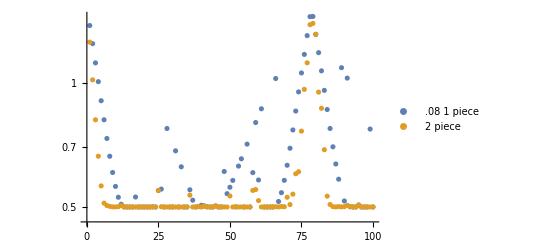

```mathematica
ListLogPlot[{SqueezeTableduration,SqueezeTableduration2},PlotRange->All,PlotLegends->{.08"1 piece","2 piece"}]
```

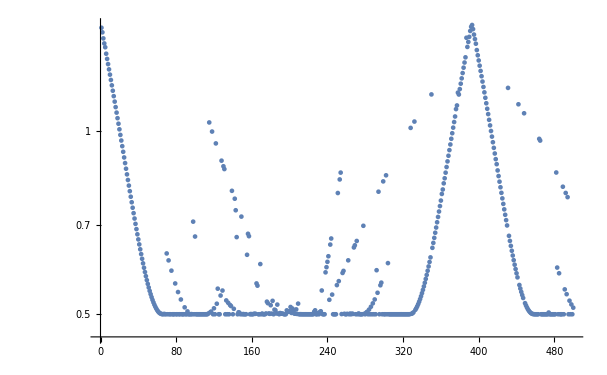

```mathematica
ListLogPlot[SqueezeTableduration,PlotRange->All]
```

```mathematica
SqueezeTableduration
```

{1.47678,1.45135,1.41848,1.39166,1.37176,1.33862,1.31273,1.28717,1.26183,1.23683,1.21218,1.18786,1.16388,1.14024,1.11695,1.09401,1.07143,1.04922,1.02739,1.00592,0.984839,0.964146,0.943846,0.923945,0.904447,0.885357,0.866681,0.848423,0.830588,0.81318,0.796204,0.779664,0.763565,0.74791,0.732703,0.717949,0.703652,0.689814,0.676439,0.663531,0.651094,0.63913,0.627642,0.616633,0.606107,0.596065,0.586511,0.577446,0.568874,0.560796,0.553215,0.546132,0.539549,0.533468,0.52789,0.522817,0.518251,0.514193,0.510647,0.507599,0.505067,0.503077,0.501639,0.500847,0.500176,0.500071,0.500477,0.500319,0.5,0.629211,0.5,0.612904,0.5,0.5,0.589563,0.5,0.5,0.5,0.561732,0.5,0.5,0.543804,0.5,0.5,0.528682,0.5,0.5,0.5,0.513234,0.5,0.5,0.505413,0.5,0.5,0.5,0.500314,0.5,0.709547,0.5,0.670748,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500003,0.500035,0.5,0.5,0.501383,1.03234,0.5036,0.505117,0.997417,0.5,0.511368,0.500042,0.95372,0.520296,0.550763,0.5,0.5,0.53665,0.893515,0.546847,0.874729,0.86556,0.5,0.526838,0.5,0.522143,0.5,0.517814,0.5158,0.797263,0.5,0.510411,0.77381,0.740781,0.669245,0.5,0.503805,0.502864,0.500001,0.723206,0.5,0.500433,0.5,0.5,0.500111,0.625995,0.677745,0.671626,0.5,0.50046,0.500001,0.500001,0.500707,0.500788,0.500869,0.561793,0.557037,0.5,0.5,0.604448,0.500031,0.501341,0.5,0.5,0.5,0.501502,0.524384,0.521338,0.501561,0.500764,0.517368,0.501242,0.526007,0.5,0.508791,0.507557,0.501451,0.51857,0.501366,0.5,0.502297,0.5012,0.501137,0.50107,0.5,0.5,0.500026,0.507411,0.505456,0.50463,0.505731,0.513901,0.502479,0.510863,0.505794,0.501262,0.500962,0.509281,0.500582,0.520493,0.5,0.500128,0.500084,0.500027,0.5,0.5,0.5,0.500026,0.5,0.5,0.5,0.5,0.500001,0.5,0.5,0.5,0.504789,0.507511,0.5,0.5,0.50197,0.5,0.504226,0.505686,0.546968,0.500001,0.5,0.5,0.585807,0.59734,0.609595,0.622568,0.528095,0.65065,0.665749,0.538561,0.5,0.5,0.5,0.500004,0.558199,0.790642,0.566663,0.832291,0.854072,0.500309,0.584454,0.589067,0.500913,0.5,0.5,0.500804,0.61303,0.5,0.501274,0.5,0.501053,0.500641,0.643616,0.648894,0.5,0.659598,0.5,0.501535,0.5,0.5,0.5,0.500041,0.698519,0.50082,0.5,0.503035,0.504657,0.5,0.508884,0.5,0.514358,0.5,0.521007,0.5,0.528759,0.5,0.590557,0.542287,0.794618,0.5,0.55786,0.563457,0.5,0.826201,0.5,0.5,0.845396,0.5,0.606604,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.50005,0.5,0.5,0.5,0.5,0.5,0.5,0.500002,0.500006,0.500055,1.01132,0.500911,0.501994,0.503643,1.0358,0.508465,0.511658,0.51536,0.519572,0.524292,0.529515,0.535245,0.541477,0.54821,0.555444,0.563175,0.571402,0.580122,0.589334,0.599035,0.609223,0.619895,1.14772,0.64268,0.654787,0.667366,0.680415,0.693929,0.707906,0.722341,0.737232,0.752574,0.768363,0.787926,0.801267,0.82009,0.83595,0.853877,0.872257,0.891058,0.910271,0.929891,0.949913,0.970578,0.991142,1.01234,1.03392,1.05587,1.08577,1.10088,1.15566,1.14734,1.17108,1.19521,1.21957,1.24431,1.26982,1.29476,1.32048,1.42189,1.37341,1.39949,1.42673,1.4589,1.48219,1.49217,1.4692,1.43908,1.41492,1.39021,1.35717,1.33076,1.30495,1.27947,1.25435,1.22944,1.20491,1.18064,1.15674,1.13319,1.11001,1.08719,1.06551,1.04261,1.02089,0.999536,0.978571,0.957996,0.937815,0.918035,0.898659,0.881742,0.861143,0.843011,0.825304,0.808026,0.791181,0.774778,0.758807,0.743287,0.728216,0.713599,0.699439,1.17641,0.672506,0.659739,0.647444,0.635622,0.624278,0.613415,0.603034,0.593138,0.583731,0.574815,1.10574,0.558462,0.551031,0.544098,0.537666,0.531736,1.06877,0.52139,0.516976,0.513071,0.509675,0.506793,0.504425,0.5026,0.501252,0.500534,0.500169,0.500016,0.500004,0.5,0.5,0.5,0.97031,0.964001,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.503259,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.854391,0.596473,0.5,0.583774,0.5,0.5,0.5,0.809695,0.5,0.549307,0.790857,0.5394,0.778428,0.5,0.526315,0.5,0.518887,0.5,0.512583}

```mathematica
65/500*4
```

13/25

```mathematica
N[13/25]
```

0.52

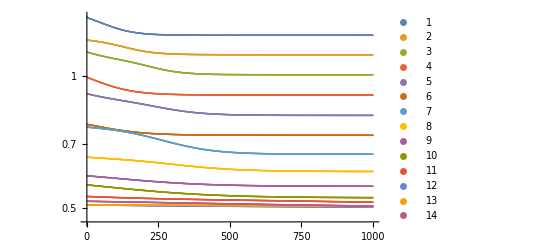

```mathematica
ListLogPlot[SqueezeTableExtraPiece,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ListLogPlot[SqueezeTableExtraPiece,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

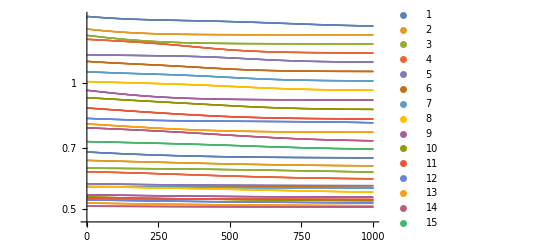

```mathematica
ListLogPlot[SqueezeTableExtraPiece,PlotRange->All,PlotLegends->Automatic]
```

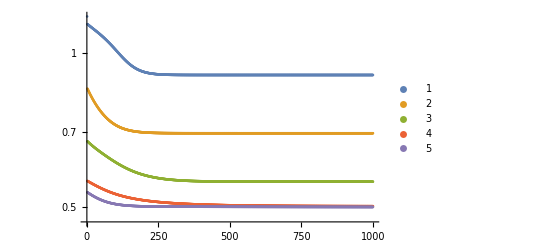

```mathematica
ListLogPlot[SqueezeTableExtraPiece,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
StateExtraPiece
```

{{{0.450625+0.0253815 ⅈ},{0.0945406+0.536055 ⅈ},{-0.536055+0.0945404 ⅈ},{0.0253819-0.450625 ⅈ}},{{0.537329+0.0316063 ⅈ},{0.167591+0.426831 ⅈ},{-0.426893+0.167471 ⅈ},{0.0317627-0.537321 ⅈ}}}

```mathematica
ξSqure[StateExtraPiece[[1]]]
```

0.904447

```mathematica
ξSqure[StateExtraPiece[[2]]]
```

0.560796

```mathematica
ξSqure[StateExtraPiece[[3]]]
```

0.500813

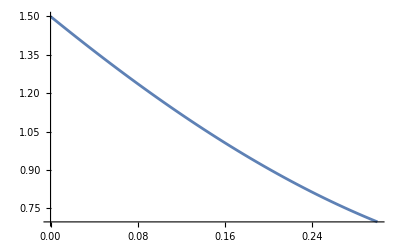

```mathematica
Plot[ξSqure[UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],t].StateθϕInitial[Pi/2,Pi/2]],{t,0,totT},PlotLegends->Automatic]
```

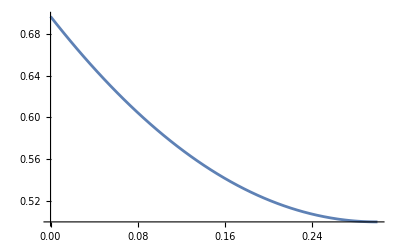

```mathematica
Plot[ξSqure[UHmuti[Last[ϕTableExtraPiece[[1]]][[1]],Last[ϕTableExtraPiece[[1]]][[2]],Last[ϕTableExtraPiece[[1]]][[3]],t].StateExtraPiece[[1]]],{t,0,totT},PlotLegends->Automatic]
```

```mathematica
pieceEach=10;
PlotpieceNumber=pieceEach*(ExtraPiece+1);
PlotpieceTable=Table[0,{j,1,PlotpieceNumber}];
Do[
Do[
If[j==1,PlotpieceTable[[i]]=ξSqure[UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],totT*i/pieceEach].StateθϕInitial[Pi/2,Pi/2]],PlotpieceTable[[i+pieceEach*(j-1)]]=ξSqure[UHmuti[Last[ϕTableExtraPiece[[j-1]]][[1]],Last[ϕTableExtraPiece[[j-1]]][[2]],Last[ϕTableExtraPiece[[j-1]]][[3]],totT*i/pieceEach].StateExtraPiece[[j-1]]]];

,{i,1,pieceEach}];

,{j,1,ExtraPiece+1}]
```

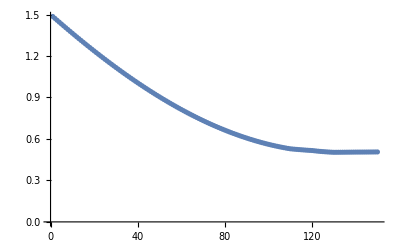

```mathematica
ListPlot[PlotpieceTable]
```

```mathematica
UIz[t_]:=MatrixExp[-I*Iz3half2.Iz3half2*t]
IzIzTable=Table[0,{j,1,PlotpieceNumber}];
Do[
IzIzTable[[i]]=ξSqure[UIz[(i*totT*(ExtraPiece+1))/PlotpieceNumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,PlotpieceNumber}];
UIz4[t_]:=MatrixExp[-I*Iz3half2.Iz3half2.Iz3half2.Iz3half2*t]
IzIzIzIzTable=Table[0,{j,1,PlotpieceNumber}];
Do[
IzIzIzIzTable[[i]]=ξSqure[UIz4[(i*0.1*(ExtraPiece+1))/PlotpieceNumber].StateθϕInitial[Pi/2,Pi/2]];

,{i,1,PlotpieceNumber}];
```

```mathematica
(PlotpieceNumber*0.1*(ExtraPiece+1))/PlotpieceNumber
```

0.6

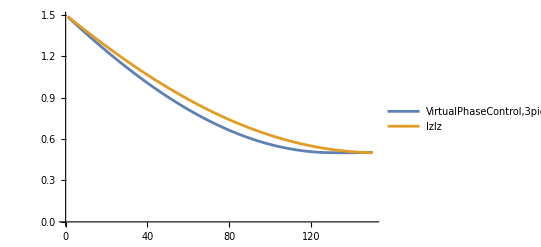

```mathematica
ListPlot[{PlotpieceTable,IzIzTable},PlotLegends->{"VirtualPhaseControl,3piece,t=0.2*3","IzIz"},Joined->True]
```

```mathematica
PlotpieceTable
```

{1.48618,1.47242,1.45872,1.4451,1.43154,1.41805,1.40462,1.39127,1.37799,1.36478,1.35165,1.33858,1.32559,1.31268,1.29984,1.28708,1.2744,1.2618,1.24927,1.23683,1.22446,1.21218,1.19998,1.18786,1.17583,1.16388,1.15202,1.14024,1.12855,1.11695,1.10544,1.09401,1.08268,1.07144,1.06028,1.04922,1.03826,1.02738,1.01661,1.00592,0.995333,0.984841,0.974446,0.964148,0.953949,0.943849,0.933848,0.923948,0.914148,0.90445,0.894855,0.885363,0.875974,0.866689,0.857509,0.848433,0.839463,0.8306,0.821843,0.813194,0.804652,0.796218,0.787894,0.779679,0.771574,0.76358,0.755697,0.747925,0.740266,0.732719,0.72529,0.717975,0.710773,0.703685,0.696713,0.689856,0.683114,0.676489,0.66998,0.663589,0.65733,0.651189,0.645166,0.63926,0.633472,0.627803,0.622253,0.616823,0.611512,0.606321,0.601255,0.596309,0.591484,0.58678,0.582198,0.577738,0.5734,0.569185,0.565093,0.561124,0.557333,0.553663,0.550115,0.54669,0.543387,0.540208,0.537151,0.534219,0.53141,0.528725,0.527255,0.525833,0.52446,0.523136,0.521861,0.520638,0.519466,0.518346,0.517279,0.516265,0.514458,0.512766,0.511189,0.509728,0.508385,0.50716,0.506054,0.505069,0.504205,0.503463,0.50359,0.503722,0.50386,0.504003,0.504151,0.504305,0.504464,0.504629,0.5048,0.504976,0.505027,0.505092,0.505168,0.505257,0.505357,0.505468,0.505591,0.505724,0.505868,0.506022}

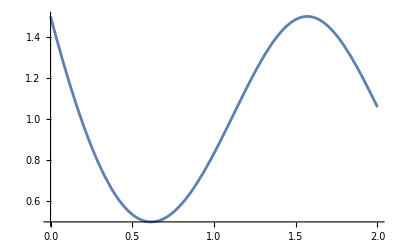

```mathematica
Plot[ξSqure[UIz[i].StateθϕInitial[Pi/2,Pi/2]],{i,0,2}]
```

```mathematica
IzIzIzIzTable
```

{1.47015,1.44061,1.41139,1.3825,1.35395,1.32574,1.29789,1.27041,1.2433,1.21657,1.19023,1.1643,1.13876,1.11365,1.08895,1.06469,1.04086,1.01748,0.994554,0.972084,0.950079,0.928546,0.907491,0.886919,0.866838,0.847251,0.828166,0.809586,0.791517,0.773964,0.75693,0.740421,0.724441,0.708992,0.694079,0.679705,0.665873,0.652585,0.639845,0.627655,0.616017,0.604933,0.594404,0.584431,0.575016,0.56616,0.557862,0.550124,0.542946,0.536326,0.530265,0.524762,0.519816,0.515426,0.511589,0.508304,0.50557,0.503383,0.501741,0.500641,0.50008,0.500054,0.50056,0.501594,0.50315,0.505226,0.507815,0.510912,0.514513,0.518612,0.523202,0.528277,0.533831,0.539857,0.546348,0.553297,0.560695,0.568536,0.57681,0.58551,0.594626,0.60415,0.614073,0.624384,0.635074,0.646133,0.65755,0.669316,0.681418,0.693847,0.706589,0.719634,0.73297,0.746585,0.760466,0.774599,0.788973,0.803574,0.818389,0.833403,0.848604,0.863975,0.879504,0.895175,0.910974,0.926884,0.942892,0.958981,0.975135,0.991339,1.00758,1.02383,1.04008,1.05632,1.07253,1.08868,1.10476,1.12077,1.13666,1.15244,1.16808,1.18357,1.19888,1.214,1.22892,1.2436,1.25804,1.27223,1.28613,1.29973,1.31302,1.32598,1.3386,1.35084,1.36271,1.37418,1.38523,1.39586,1.40604,1.41577,1.42502,1.43379,1.44206,1.44982,1.45706,1.46377,1.46993,1.47554,1.48058,1.48506}

```mathematica
PlotpieceTable0p04ThirtyPiece={1.4861757450337774,1.4724163744209555,1.458722768757146,1.4450958044290187,1.4315363535582082,1.4180452839455002,1.4046234590152928,1.391271737760336,1.3779909746867571,1.3647820197593756,1.3516457219250768,1.3385829178621882,1.3255944436777738,1.3126811306962254,1.29984380541457,1.2870832894548982,1.274400399515229,1.2617959473195306,1.2492707395673532,1.2368255779796882,1.2244612909739578,1.2121786370484686,1.1999784023357412,1.1878613676888485,1.1758283086323063,1.1638799953131127,1.152017192451982,1.1402406592948064,1.1285511495644,1.1169494114125174,1.10543629781102,1.094012432147042,1.0826785456896082,1.0714353639390883,1.060283606582062,1.0492239874463376,1.0382572144561752,1.0273839895877508,1.0166050088248804,1.005920962115033,0.9953326271926884,0.9848405840389909,0.9744455043757364,0.9641480537141092,0.953948891312457,0.9438486701344052,0.933848036807351,0.9239476315813265,0.9141480882882376,0.9044500343014937,0.8948551550563943,0.8853629603035558,0.8759740591830975,0.8666890541282682,0.8575085408352425,0.8484331082324755,0.8394633384497073,0.8305998067867215,0.8218430816819474,0.81319372468096,0.8046517361784282,0.7962182382700171,0.78789377128603,0.7796788685585428,0.7715740563886619,0.7635798540141139,0.755696773577177,0.7479253200929772,0.7402659914181443,0.7327192782198637,0.7252901884523341,0.7179745486692589,0.7107728301283252,0.7036854967720423,0.6967130052001876,0.6898558046426359,0.6831143369325774,0.676489036480159,0.6699803302465253,0.6635886377182985,0.6573304260571728,0.6511892540166513,0.6451655374683003,0.6392596839444165,0.6334720926628372,0.6278031545490095,0.6222532522555682,0.6168227601796819,0.6115120444783839,0.606321463082093,0.6012548147611874,0.5963088216732648,0.5914838256203483,0.5867801600512754,0.5821981500760154,0.5777381124786525,0.573400355729194,0.5691851799943244,0.5650928771472465,0.5611237307767218,0.5573325212742732,0.5536629516005949,0.5501153648408552,0.5466900963738057,0.5433874739012627,0.5402078174783018,0.5371514395442678,0.5342186449546786,0.5314097310141173,0.5287249875101838,0.5272550234949538,0.5258329860946116,0.5244595864532644,0.523135525600771,0.5218614944076501,0.5206381735463699,0.5194662334588507,0.5183463343300032,0.5172791260671066,0.5162652482848777,0.5144582575361651,0.5127657725440014,0.5111887450065151,0.5097281305870813,0.508384889507183,0.5071599871504457,0.5060543946784963,0.5050690896592205,0.5042050567080312,0.5034632881427314,0.5035901391508972,0.503722294284553,0.503859798244277,0.5040026956964838,0.5041510312538573,0.5043048494556177,0.5044641947476309,0.5046291114623664,0.5047996437986948,0.5049758358015579,0.5050274958373584,0.5050918001969951,0.5051683808566862,0.5052568896214655,0.5053569984067747,0.5054683995102651,0.5055908058737852,0.505723951335525,0.505867590872334,0.5060215008322051};
PlotpieceTable0p02ThirtyPiece={1.4861789943991737,1.4724228314998211,1.4587323919366253,1.4451085521311344,1.4315521842355394,1.4192647868418014,1.406927594311323,1.3945797093770806,1.382244130296919,1.3699353734912674,1.3568493092542002,1.3438250860179646,1.3308661699481221,1.3179752532603415,1.305154515925441,1.2924102887443176,1.2797394133118511,1.267143316739108,1.2546232897603868,1.242180520087597,1.2298890166102283,1.2176745807808018,1.2055383308149785,1.1934813278086738,1.181504586021776,1.1697499944242107,1.1580715605932161,1.1464706807948637,1.1349486597380416,1.1235067247073773,1.1120359489750302,1.1006504555034307,1.0893512065051283,1.078139133210943,1.0670151393817329,1.0560598680983468,1.045192364973743,1.0344135038928406,1.023724135906812,1.0131250912643663,1.002743990973407,0.9924526522370838,0.9822518160470245,0.972142210698654,0.9621245524814813,0.9519784050227962,0.9419306272670162,0.931981899841646,0.9221328949759905,0.9123842766256944,0.9029339260010493,0.8935804281393668,0.8843244554607952,0.8751666711433295,0.8661077295300365,0.857067844896212,0.8481299787800964,0.8392947356046889,0.830562711918725,0.8219344963836025,0.8184953635165216,0.8150453173669939,0.811586013372823,0.8081191000277764,0.804646218583875,0.796300609722173,0.7880623051156678,0.779931930430651,0.7719101026129094,0.763997430124415,0.7567898234175189,0.7496783924216289,0.7426637853870626,0.7357466505583216,0.7289276366031975,0.7222022435951183,0.7155715799503709,0.7090362261309354,0.7025967476949428,0.6962536954211721,0.6895276749871723,0.6829161292361616,0.6764195486009961,0.6700384181229695,0.6637732174884308,0.65785463061497,0.6520417565511432,0.646335044266314,0.6407349350141032,0.6352418624253433,0.6308436112035352,0.6265136813191143,0.6222526360244407,0.6180610249530649,0.6139393842269867,0.6091990228759472,0.6045772553902811,0.6000750371770993,0.5956933360828429,0.5914331328211693,0.586814353219236,0.5823134903788707,0.5779310081362552,0.5736673607146643,0.5695229927003504,0.5681368395389579,0.5668118989867179,0.5655491893293672,0.5643497326585032,0.5632145549537377,0.5628246673282866,0.5624653900429346,0.562137575517851,0.5618420741763588,0.5615797343761175,0.5590499084722296,0.5565897618098326,0.5541996403876415,0.5518798707806869,0.5496307600426897,0.5464073201430708,0.5432928882355101,0.5402882519701513,0.5373941902017687,0.5346114730418499,0.5323750112398467,0.5302487424685765,0.5282331878146576,0.5263288743807641,0.5245363360567905,0.5251046343889416,0.5257227362338688,0.5263912171254479,0.5271106543301469,0.5278816267192559,0.5257123881196895,0.5236601984684759,0.5217251920464248,0.519907501846957,0.5182072598434067,0.5163866305352067,0.5146672710077504,0.5130501615916248,0.5115363257769447,0.5101268315288789,0.5091774369390414,0.5083407876398554,0.507617836121119,0.5070095674686392,0.5065169994568515};
PlotpieceTable0p1SixPiece={1.4861757411699787,1.4724163667464716,1.4587227573247454,1.4450957892911263,1.431536334766921,1.41804526155259,1.4046234330722123,1.39127170831823,1.3779909417964702,1.3647819834714574,1.3516456787120155,1.3385828682371654,1.3255943880623187,1.3126810694457725,1.2998437388355113,1.287083217816312,1.2744003230571646,1.261795866259005,1.249270654102765,1.2368254881977472,1.224461165030323,1.2121784759129528,1.1999782069335494,1.1878611389051617,1.1758280473160088,1.163879702279849,1.152016868486682,1.1402403051538212,1.128550765977299,1.1169489990836354,1.1054357469819496,1.0940117465164452,1.082677728819255,1.0714344192636418,1.0602825374175797,1.0492227969976997,1.038255905823615,1.0273825657726163,1.0166034727347557,1.0059193165683085,0.995330781055622,0.9848385438593553,0.9744432764791076,0.9641456442084433,0.953946306092312,0.9438459148848721,0.933845117007714,0.923944552508488,0.9141448550199406,0.9044466517193681,0.8948505632886842,0.8853572038740548,0.8759671810472416,0.8666810957664998,0.8574995423381194,0.8484231083783855,0.8394523747759731,0.8305879156547707,0.8218302983371365,0.8131800833075892,0.8046378241769396,0.7962040676468555,0.7878793534748754,0.7796642144398653,0.7715591763079197,0.7635647577987128,0.7556814705522997,0.7479098190963744,0.7402503008139766,0.732703405911662,0.7252696173881286,0.7179494110033047,0.7107432552478998,0.703651611313423,0.6966749330626654,0.689813673701948,0.6830682654231834,0.6764391399308367,0.6699267214872524,0.6635314268855095,0.6572536654227461,0.6510938388739711,0.6450523414663543,0.6391295598540019,0.6333258731022628,0.6276416526676074,0.6220772622754915,0.6166330580774784,0.6113093885009449,0.6061065942590773,0.6010250083290651,0.5960649559307976,0.591226754506051,0.5865107136981778,0.5819171353322907,0.5774463133959529,0.5730985340203638,0.5688740754620523,0.5647732080850691,0.5607961943436923,0.5569650897929763,0.5532570728744002,0.5496723826847265,0.5462112504285477,0.5428738994285398,0.5396605451370253,0.5365713951488864,0.5336066492158602,0.5307664992622874,0.5280511294023373,0.5254607159587703,0.5229954274832835,0.5206554247784931,0.5184408609216102,0.5163518812898615,0.5143886235877178,0.5125512178759895,0.5108397866028549,0.5092544446368927,0.5077952993021762,0.5064624504155231,0.5052559903259639,0.504176003956516,0.5032225688483536,0.5023957552074603,0.502267888413291,0.5021442781429832,0.5020249669685874,0.5019099966704461,0.5017994082281898,0.5016932418120932,0.5015915367747759,0.5014943316432672,0.5014016641114367,0.5013135710327747,0.5012300884135557,0.5011512514063643,0.5010770943039964,0.5010076505337397,0.5009429526520242,0.5008830323394629,0.5008279203962664,0.500777646738048,0.5007322403920074,0.5006917294935047,0.5006561412830215,0.5006255021035069,0.5005998373981122,0.5005791717083157,0.5005635286724333};
PlotpieceTable0p15FourPiece={1.4859893692091146,1.472045400548812,1.4581690107103278,1.444361111942198,1.4306226119902792,1.4169544140380812,1.4033574166473826,1.3898325136991618,1.3763805943348353,1.3630025428977972,1.3496992388752898,1.3364715568405798,1.323320366395465,1.3102465321131058,1.2972509134811845,1.2843343648454055,1.2714977353533277,1.2587418688985421,1.2460676040651897,1.2334757740728384,1.220967206721697,1.208542724338208,1.1962031437209721,1.1839492760870618,1.1717819270186858,1.1597018964102337,1.1477099784156832,1.1358069613963981,1.1239936278692984,1.1122707544554151,1.1006391118288366,1.0890994646660432,1.0776525715956367,1.0662991851484631,1.0550400517081493,1.0438759114620277,1.0328074983524753,1.0218355427587191,1.0109607631888622,1.0001838745643217,0.9895055853708647,0.978926597612057,0.9684476067631298,0.9580693017252767,0.9477923647803768,0.9376174715461565,0.9275452909317828,0.9175764850938973,0.9077117093930964,0.8979516123508533,0.8882968356068878,0.878748013876995,0.8693057749113204,0.8599707394530967,0.8507435211978392,0.8416247267530044,0.832614955598117,0.8237148000453594,0.814924845200635,0.8062456689251095,0.7976778417972177,0.7892219270751634,0.7808784806598837,0.7726480510585125,0.7645311793483159,0.7565283991411301,0.7486402365482765,0.7408672101459797,0.7332098309412751,0.7256686023384167,0.7182440201057843,0.7109365723432913,0.7037467394502984,0.6966749940940313,0.6897282636262919,0.6829003234246789,0.6761916226766984,0.669602602662303,0.66313369673074,0.6567853302757465,0.6505579207110619,0.6444518774463277,0.638467601863353,0.6326054872927824,0.6268659189911776,0.621249274118532,0.6157559217162256,0.6103862226854342,0.6051405297660086,0.6000191875158323,0.5950225322906677,0.5901508922245018,0.5854045872103975,0.5807839288818666,0.5762892205947616,0.571920757409704,0.5676788260750538,0.5635637050104201,0.559575664290737,0.5557149656308866,0.5519818623709005,0.5483765994617329,0.5448994134516052,0.5415505324729515,0.5383301762299368,0.5352385559865946,0.5322758745555467,0.529442326287348,0.5267380970604374,0.5241633642717145,0.5217182968277381,0.5209526264572586,0.5202041670570061,0.5194731482512984,0.5187597976146425,0.518064340629065,0.5173870006454422,0.5167279988489868,0.5160875542290364,0.5154658835532795,0.5148632013465677,0.51427971987445,0.5137156491315782,0.5131711968351076,0.5126465684232413,0.5121419670590455,0.5116575936396743,0.5111936468111222,0.5107503229886465,0.510327816382981,0.5099263190324457,0.509546020841104,0.5091871096230562,0.5088497711529896,0.5085341892231057,0.5082405457065124,0.5079690206271947,0.5077197922366568,0.5074930370973276,0.5072889301728181,0.5071076449251164,0.5069493534187881,0.5068142264322693,0.5067024335763008,0.5066141434195759,0.5065495236216493,0.5065087410731528,0.5064919620433612};
PlotpieceTable0p3TwoPiece={1.486175741169994,1.472416366746502,1.4587227573247903,1.4450957892911862,1.4315363347669956,1.418045261552679,1.4046234330723153,1.391271708318348,1.3779909417966019,1.3647819834716028,1.3516456787121742,1.3385828682373377,1.3255943880625043,1.3126810694459714,1.2998437388357231,1.2870832178165368,1.2744003230574015,1.2617958662592539,1.2492706541030267,1.2368254881980199,1.2244611650306076,1.2121784759132486,1.1999782069338574,1.1878611389054812,1.1758280473163394,1.1638797022801861,1.1520168684870253,1.1402403051541707,1.128550765977655,1.1169489990839965,1.1054357469823168,1.094011746516819,1.0826777288196343,1.0714344192640275,1.0602825374179705,1.0492227969980965,1.038255905824017,1.0273825657730233,1.0166034727351678,1.005919316568725,0.9953307810560446,0.9848385438597824,0.9744432764795393,0.9641456442088789,0.9539463060927512,0.9438459148853161,0.9338451170081614,0.9239445525089383,0.9141448550203957,0.9044466517198265,0.8948505632889326,0.8853572038740992,0.8759671810470867,0.8666810957661524,0.857499542337584,0.848423108377665,0.8394523747750741,0.8305879156536975,0.8218302983358955,0.8131800833061837,0.8046378241753745,0.7962040676451354,0.7878793534730058,0.7796642144378507,0.771559176305765,0.7635647577964225,0.7556814705498779,0.7479098190938265,0.740250300811306,0.7327034059088737,0.7252696173852277,0.7179494110002944,0.7107432552447859,0.7036516113102088,0.6966749330593555,0.6913855313709901,0.6861676762843223,0.6810214995082524,0.6759471265033377,0.6709446764395139,0.6660142622385883,0.6611559905999476,0.6563699620241974,0.6516562708348808,0.6470150051984296,0.6424462471424794,0.6379500725726792,0.6335265512881068,0.629175746995398,0.6248977173216992,0.6206925138265218,0.6165601820125972,0.6125007613358104,0.6085142852142782,0.6046007810366585,0.6007602701697463,0.5969927679654048,0.5932982837669203,0.5896768209148036,0.5861283767520993,0.5826529426292582,0.5792505039085947,0.5759210399683925,0.5726645242066826,0.5694809240447358,0.5663702009302984,0.5633323103406052,0.5603672017852048,0.5574748188086143,0.5546550989928376,0.5519079739597677,0.5492333693735005,0.5466312049425817,0.544101394422198,0.5416438456163462,0.5392584603799904,0.5369451346212273,0.5347037583034726,0.5325342154476911,0.5304363841346764,0.5284101365074028,0.5264553387734594,0.5245718512075745,0.5227595281542521,0.5210182180305234,0.5193477633288281,0.5177480006200359,0.5162187605566193,0.5147598678759824,0.5133711414039592,0.512052394058496,0.5108034328535072,0.5096240589029384,0.5085140674250206,0.5074732477467414,0.5065013833085308,0.5055982516691677,0.5047636245109226,0.5039972676449334,0.5032989410168263,0.5026683987125906,0.5021053889647036,0.5016096541585207,0.5011809308389346,0.5008189497173106,0.5005234356786903,0.5002941077893011,0.5001306793043314,0.5000328576760247,0.5000003445620591};
PlotpieceTable0p2ThreePiece={1.486175741170308,1.472416366747123,1.4587227573257107,1.4450957892924003,1.4315363347684942,1.4180452615544545,1.4046234330743623,1.3912717083206592,1.3779909417991716,1.3647819834744233,1.3516456787152396,1.3385828682406404,1.3255943880660395,1.312681069449733,1.2998437388397048,1.287083217820733,1.2744003230618066,1.2617958662638613,1.2492706541078304,1.2368254882030165,1.2244611650357904,1.2121784759186132,1.199978206939397,1.1878611389111915,1.175828047322216,1.163879702286223,1.1520168684932175,1.1402403051605146,1.1285507659841456,1.1169489990906298,1.105435746989087,1.094011746523723,1.0826777288266665,1.0714344192711835,1.0602825374252474,1.0492227970054901,1.0382559058315226,1.0273825657806375,1.016603472742886,1.005919316576544,0.9953307810639597,0.9848385438677905,0.9744432764876367,0.964145644217062,0.9539463061010173,0.9438459148936602,0.9338451170165809,0.9239445525174286,0.914144855028955,0.9044466517284513,0.8948510780626375,0.8853582125082102,0.8759686634405973,0.8666830325593559,0.8575019148553943,0.8484258986577375,0.8394555652802458,0.8305914895002197,0.8218342391189212,0.8131843750886619,0.8046424514550035,0.7962090153240153,0.7878846068297124,0.7796697591017101,0.7715649982331296,0.7635708432487601,0.7556878060735162,0.7479163915012024,0.7402570971635963,0.7327104134998751,0.7252768237263971,0.7179568038068421,0.7107508224227331,0.703659340944345,0.6966828134020034,0.6898216864577936,0.68307639937768,0.6764473840040439,0.6699350647286451,0.663539858466021,0.6572621746273144,0.6511024150945539,0.6450609741953737,0.639138238678185,0.6333345876878109,0.6276503927415749,0.6220860177058516,0.6166418187730891,0.611318144439301,0.6061153354820288,0.6010337249387809,0.5960736380859548,0.5912353924182323,0.5865192976284692,0.5819256555880619,0.5774547603278097,0.57310689801926,0.5688823469565538,0.5647813775387609,0.5608042522527106,0.558753448857499,0.5567247943009606,0.5547191802392653,0.5527374803131264,0.5507805506812942,0.5488492305800894,0.5469443429076852,0.5450666948318639,0.5432170784200379,0.5413962712903326,0.5396050372826053,0.537844127148251,0.5361142792577245,0.5344162203246927,0.5327506661457833,0.531118322354879,0.529519885190948,0.5279560422784007,0.5264274734189458,0.5249348513939613,0.5234788427763521,0.5220601087508747,0.5206793059419024,0.519337087247574,0.5180341026792539,0.5167710002052099,0.515548426597372,0.5143670282800206,0.5132274521791911,0.5121303465715494,0.5110763619314549,0.5100661517748488,0.5091003734985793,0.5081796892136936,0.5073047665711643,0.5064762795784652,0.5056949094053154,0.504961345176854,0.5042762847524134,0.5036404354879955,0.5030545149804351,0.5025192517911954,0.5020353861475992,0.5016036706192382,0.5012248707671996,0.5008997657636449,0.5006291489791987,0.5004138285354727,0.5002546278200029,0.5001523859607273};
IzIzTable={1.4880241038716149,1.476096829939678,1.4642187975384993,1.4523906228382704,1.440612918799299,1.4288862951264323,1.4172113582236923,1.405588711149123,1.3940189535698315,1.38250268171726,1.3710404883426544,1.359632962672755,1.3482806903657114,1.3369842534671954,1.3257442303667668,1.314561195754425,1.303435720577424,1.2923683719972794,1.2813597133470354,1.2704103040887331,1.2595206997711352,1.2486914519876742,1.2379231083346363,1.2272162123695884,1.216571303570039,1.205988917292347,1.1954695847308696,1.1850138328773563,1.1746221844805915,1.1642951580062826,1.1540332675972038,1.1438370230335804,1.1337069296937439,1.1236434885150262,1.113647195954919,1.10371854395249,1.0938580198900574,1.0840661065551271,1.0743432821025953,1.0646900200172067,1.0551067890762917,1.0455940533127595,1.0361522719783642,1.0267818995072417,1.017483385479718,1.008257174586391,0.9991037065924767,0.9900234163024528,0.9810167335249508,0.9720840830379522,0.9632258845542427,0.9544425526871633,0.9457344969166297,0.9371021215554437,0.9285458257158841,0.9200660032765826,0.9116630428496858,0.9033373277483044,0.8950892359542507,0.8869191400860645,0.8788274073673278,0.8708143995952716,0.8628804731096757,0.8550259787620565,0.8472512618851531,0.8395566622627039,0.8319425140995208,0.8244091459918566,0.8169568808980728,0.8095860361095971,0.8022969232221869,0.7950898481074882,0.7879651108848881,0.7809230058936774,0.773963821665504,0.7670878408971311,0.7602953404234957,0.7535865911910674,0.7469618582315153,0.7404214006356641,0.7339654715277689,0.7275943180400803,0.7213081812877192,0.715107296343853,0.7089918922151766,0.7029621918176965,0.6970184119528194,0.6911607632837438,0.6853894503121578,0.6797046713552415,0.67410661852297,0.6685954776957268,0.6631714285022152,0.657834644297679,0.6525852921424233,0.6474235327806448,0.6423495206195591,0.6373634037088372,0.6324653237203401,0.6276554159281655,0.622933809188986,0.6183006259226969,0.6137559820933662,0.6092999871904821,0.6049327442105057,0.6006543496387236,0.5964648934313965,0.5923644589982149,0.5883531231850501,0.5844309562570014,0.5805980218817437,0.5768543771131756,0.5732000723753568,0.5696351514467481,0.5661596514447385,0.5627736028104775,0.5594770292939912,0.5562699479395947,0.5531523690715925,0.5501242962802817,0.5471857264082256,0.5443366495368303,0.5415770489732084,0.5389069012373202,0.5363261760494082,0.5338348363177152,0.5314328381264835,0.529120130724235,0.5268966565123383,0.5247623510338473,0.5227171429626261,0.5207609540927445,0.5188936993281545,0.5171152866726378,0.5154256172200282,0.5138245851447063,0.5123120776923631,0.5108879751710333,0.5095521509423981,0.5083044714133507,0.5071447960278295,0.5060729772589116,0.5050888606011736,0.5041922845633051,0.5033830806609874,0.5026610734100248,0.5020260803197352,0.5014779118865924,0.501016371588122,0.5006412558770477};
IzIzIzIzTable={1.4701516199624103,1.440612918799299,1.4113934608986922,1.38250268171726,1.3539498833858423,1.3257442303667661,1.2978947451641996,1.2704103040887327,1.243299633077361,1.2165713035700385,1.1902337284439026,1.1642951580062828,1.1387636760475637,1.11364719595492,1.0889534568879564,1.0646900200172067,1.040864264826448,1.0174833854797183,0.9945543872539399,0.9720840830379528,0.9500790898987802,0.9285458257158836,0.9074905058841144,0.8869191400860641,0.8668375291344559,0.8472512618851529,0.8281657122213715,0.8095860361095973,0.7915171687276744,0.7739638216655045,0.7569304801987168,0.7404214006356644,0.7244406077380134,0.7089918922151764,0.6940788082927696,0.6797046713552415,0.6658725556627638,0.6525852921424233,0.6398454662536959,0.6276554159281655,0.6160172295833526,0.6049327442105068,0.5944035435361308,0.5844309562570014,0.5750160543483303,0.5661596514447387,0.5578623012935966,0.5501242962802821,0.542945666024828,0.5363261760494085,0.5302653265160382,0.5247623510338473,0.5198162155352131,0.5154256172200284,0.5115889835673111,0.5083044714133504,0.5055699660955353,0.5033830806609869,0.5017411551390984,0.5006412558770477,0.5000801749373505,0.5000544295565039,0.5005602616637608,0.501593637459093,0.5031502470494043,0.5052255041420772,0.5078145457949665,0.5109122322220085,0.5145131466536439,0.5186115952513513,0.5232016070756431,0.5282769341070064,0.533831051319356,0.5398571568057342,0.5463481719561454,0.553296741687568,0.5606952347264671,0.5685357439442853,0.5768100867467278,0.5855098055179282,0.5946261681209364,0.6041501684563428,0.6140725270812921,0.6243836918916068,0.6350738388702426,0.646132872905917,0.6575504286863534,0.6693158716712844,0.6814182991511502,0.6938465413982111,0.7065891629177647,0.719634463808092,0.7329704812388647,0.7465849910588853,0.7604655095453015,0.774599295307757,0.7889733513624053,0.8035744273922427,0.818389022211873,0.833403386456528,0.8486035255170765,0.863975202744617,0.8795039429503773,0.8951750362286834,0.9109735421330487,0.9268842942376625,0.942891905118908,0.9589807717939154,0.9751350816555477,0.991338818945583,1.0075757718102256,1.0238295399843103,1.040083543152771,1.0563210300398547,1.0725250882784207,1.0886786551131025,1.104764528992273,1.12076538210453,1.1366637739156142,1.1524421657613713,1.1680829365513787,1.183568399636048,1.1988808208874686,1.2140024380406271,1.2289154813370289,1.2436021955070171,1.2580448631200563,1.2722258293239919,1.2861275279846018,1.2997325092257894,1.3130234683581752,1.3259832761700847,1.3385950105395663,1.3508419893095729,1.3627078043506846,1.3741763567169878,1.385231892781146,1.3958590412145688,1.4060428506581686,1.415768827908878,1.4250229764272624,1.4337918349525662,1.4420625159939482,1.4498227439508022,1.457060892601541,1.4637660216894246,1.469927912326339,1.4755371009314522,1.4805849114214515,1.4850634853731666};
```

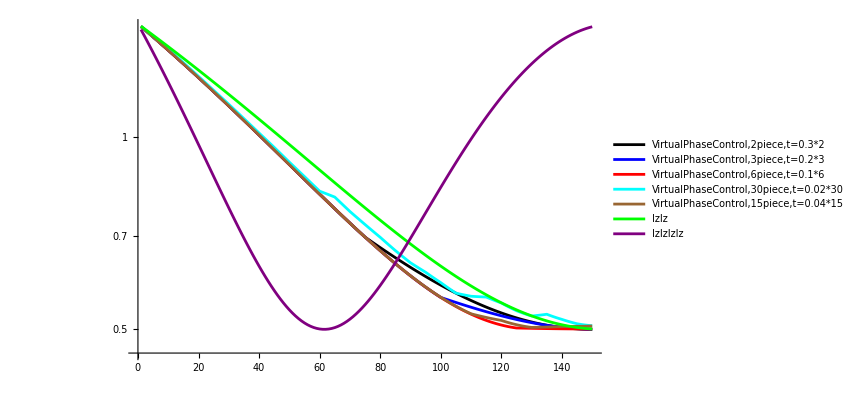

```mathematica
ListLogPlot[{PlotpieceTable0p3TwoPiece,PlotpieceTable0p2ThreePiece,PlotpieceTable0p1SixPiece,PlotpieceTable0p02ThirtyPiece,PlotpieceTable0p04ThirtyPiece,IzIzTable,IzIzIzIzTable},PlotLegends->{"VirtualPhaseControl,2piece,t=0.3*2","VirtualPhaseControl,3piece,t=0.2*3","VirtualPhaseControl,6piece,t=0.1*6","VirtualPhaseControl,30piece,t=0.02*30","VirtualPhaseControl,15piece,t=0.04*15","IzIz","IzIzIzIz"},Joined->True,PlotStyle->{Black,Blue,Red,Cyan,Brown,Green,Purple}]
```

```mathematica
ϕTableExtraPiece
```

{{{1.38395,2.9069,1.33866},{1.39336,2.88082,1.37341},{1.40296,2.8557,1.40772},{1.41277,2.83152,1.44157},{1.42281,2.80825,1.47494},{1.4331,2.78587,1.50783},{1.44366,2.76435,1.54021},{1.45453,2.74364,1.57209},{1.4657,2.72372,1.60344},{1.47721,2.70456,1.63427},{1.48907,2.68612,1.66456},{1.5013,2.66838,1.69431},{1.5139,2.65129,1.72353},{1.5269,2.63483,1.7522},{1.54031,2.61897,1.78033},{1.55414,2.60367,1.80791},{1.5684,2.5889,1.83495},{1.5831,2.57465,1.86146},{1.59824,2.56087,1.88743},{1.61384,2.54755,1.91287},{1.62989,2.53465,1.93778},{1.64641,2.52215,1.96218},{1.66338,2.51003,1.98607},{1.68082,2.49827,2.00946},{1.69873,2.48683,2.03235},{1.71709,2.47571,2.05476},{1.7359,2.46488,2.0767},{1.75517,2.45432,2.09817},{1.77487,2.44401,2.11918},{1.795,2.43394,2.13974},{1.81555,2.42409,2.15987},{1.8365,2.41444,2.17957},{1.85783,2.40499,2.19885},{1.87954,2.3957,2.21772},{1.9016,2.38658,2.23619},{1.92398,2.37761,2.25426},{1.94667,2.36878,2.27195},{1.96964,2.36008,2.28926},{1.99287,2.35149,2.30621},{2.01632,2.34302,2.32278},{2.03997,2.33464,2.339},{2.0638,2.32635,2.35487},{2.08776,2.31815,2.37039},{2.11184,2.31002,2.38557},{2.13599,2.30197,2.40041},{2.16019,2.29398,2.41492},{2.18441,2.28605,2.4291},{2.20861,2.27818,2.44295},{2.23277,2.27036,2.45649},{2.25686,2.26259,2.4697},{2.28084,2.25487,2.4826},{2.30469,2.24719,2.49518},{2.32838,2.23955,2.50746},{2.35189,2.23196,2.51943},{2.37519,2.2244,2.53109},{2.39826,2.21688,2.54246},{2.42108,2.2094,2.55352},{2.44362,2.20196,2.56429},{2.46588,2.19456,2.57477},{2.48783,2.18719,2.58495},{2.50946,2.17986,2.59486},{2.53075,2.17257,2.60447},{2.55169,2.16531,2.61381},{2.57228,2.1581,2.62288},{2.5925,2.15092,2.63167},{2.61235,2.14379,2.6402},{2.63182,2.1367,2.64846},{2.65091,2.12965,2.65647},{2.66961,2.12264,2.66422},{2.68792,2.11568,2.67172},{2.70584,2.10876,2.67898},{2.72337,2.10189,2.68599},{2.74051,2.09507,2.69277},{2.75726,2.0883,2.69933},{2.77363,2.08158,2.70565},{2.78962,2.0749,2.71176},{2.80522,2.06828,2.71765},{2.82045,2.06172,2.72333},{2.83532,2.0552,2.72881},{2.84982,2.04874,2.73408},{2.86396,2.04233,2.73917},{2.87774,2.03598,2.74406},{2.89118,2.02969,2.74877},{2.90429,2.02345,2.7533},{2.91705,2.01727,2.75766},{2.92949,2.01115,2.76185},{2.94162,2.00509,2.76587},{2.95342,1.99909,2.76974},{2.96493,1.99315,2.77345},{2.97613,1.98726,2.77701},{2.98705,1.98144,2.78043},{2.99768,1.97568,2.78371},{3.00803,1.96998,2.78685},{3.01811,1.96434,2.78986},{3.02793,1.95876,2.79274},{3.03749,1.95325,2.7955},{3.04681,1.94779,2.79814},{3.05588,1.9424,2.80067},{3.06471,1.93707,2.80309},{3.07332,1.9318,2.8054},{3.0817,1.92659,2.8076},{3.08986,1.92144,2.80971},{3.09781,1.91636,2.81172},{3.10556,1.91133,2.81363},{3.11311,1.90637,2.81546},{3.12046,1.90147,2.8172},{3.12763,1.89663,2.81886},{3.13462,1.89185,2.82044},{3.14142,1.88713,2.82194},{3.14806,1.88247,2.82337},{3.15453,1.87786,2.82472},{3.16083,1.87332,2.82601},{3.16698,1.86884,2.82723},{3.17297,1.86441,2.82838},{3.17882,1.86005,2.82948},{3.18452,1.85574,2.83051},{3.19008,1.85149,2.83149},{3.19551,1.84729,2.83242},{3.2008,1.84316,2.83329},{3.20597,1.83907,2.83411},{3.21101,1.83505,2.83488},{3.21594,1.83108,2.83561},{3.22074,1.82716,2.83629},{3.22543,1.8233,2.83693},{3.23001,1.81949,2.83753},{3.23449,1.81573,2.83809},{3.23885,1.81203,2.83861},{3.24312,1.80838,2.83909},{3.24729,1.80478,2.83954},{3.25137,1.80123,2.83996},{3.25535,1.79773,2.84034},{3.25924,1.79428,2.84069},{3.26305,1.79088,2.84101},{3.26677,1.78753,2.84131},{3.2704,1.78423,2.84158},{3.27396,1.78097,2.84182},{3.27744,1.77776,2.84204},{3.28084,1.7746,2.84223},{3.28417,1.77149,2.8424},{3.28743,1.76842,2.84255},{3.29062,1.76539,2.84268},{3.29374,1.76241,2.84279},{3.29679,1.75948,2.84288},{3.29979,1.75658,2.84295},{3.30271,1.75373,2.843},{3.30558,1.75093,2.84304},{3.30839,1.74816,2.84306},{3.31114,1.74544,2.84306},{3.31384,1.74275,2.84305},{3.31648,1.74011,2.84303},{3.31906,1.7375,2.843},{3.3216,1.73494,2.84295},{3.32409,1.73241,2.84289},{3.32652,1.72992,2.84282},{3.32891,1.72747,2.84273},{3.33125,1.72506,2.84264},{3.33355,1.72268,2.84254},{3.3358,1.72034,2.84243},{3.33801,1.71803,2.84231},{3.34018,1.71576,2.84218},{3.34231,1.71352,2.84204},{3.3444,1.71132,2.8419},{3.34644,1.70915,2.84174},{3.34845,1.70701,2.84159},{3.35043,1.70491,2.84142},{3.35236,1.70284,2.84125},{3.35427,1.7008,2.84107},{3.35613,1.69879,2.84089},{3.35797,1.69681,2.8407},{3.35977,1.69486,2.84051},{3.36154,1.69295,2.84031},{3.36327,1.69106,2.84011},{3.36498,1.6892,2.83991},{3.36666,1.68737,2.8397},{3.3683,1.68557,2.83949},{3.36992,1.68379,2.83927},{3.37151,1.68204,2.83905},{3.37308,1.68032,2.83883},{3.37461,1.67863,2.83861},{3.37612,1.67696,2.83838},{3.37761,1.67532,2.83815},{3.37907,1.67371,2.83792},{3.38051,1.67211,2.83769},{3.38192,1.67055,2.83745},{3.38331,1.66901,2.83721},{3.38467,1.66749,2.83698},{3.38601,1.66599,2.83674},{3.38734,1.66452,2.8365},{3.38864,1.66307,2.83626},{3.38991,1.66164,2.83601},{3.39117,1.66024,2.83577},{3.39241,1.65886,2.83553},{3.39363,1.6575,2.83528},{3.39483,1.65616,2.83504},{3.39601,1.65484,2.83479},{3.39717,1.65354,2.83455},{3.39831,1.65226,2.8343},{3.39944,1.651,2.83406},{3.40055,1.64976,2.83381},{3.40164,1.64854,2.83357},{3.40271,1.64734,2.83332},{3.40377,1.64616,2.83307},{3.40481,1.645,2.83283},{3.40583,1.64385,2.83259},{3.40684,1.64272,2.83234},{3.40784,1.64161,2.8321},{3.40882,1.64052,2.83185},{3.40978,1.63944,2.83161},{3.41073,1.63838,2.83137},{3.41167,1.63734,2.83113},{3.41259,1.63631,2.83089},{3.4135,1.6353,2.83065},{3.41439,1.63431,2.83041},{3.41527,1.63333,2.83017},{3.41614,1.63236,2.82994},{3.417,1.63142,2.8297},{3.41784,1.63048,2.82947},{3.41867,1.62956,2.82923},{3.41949,1.62866,2.829},{3.4203,1.62776,2.82877},{3.4211,1.62689,2.82854},{3.42188,1.62602,2.82831},{3.42265,1.62517,2.82808},{3.42342,1.62433,2.82785},{3.42417,1.62351,2.82763},{3.42491,1.6227,2.8274},{3.42564,1.6219,2.82718},{3.42636,1.62111,2.82695},{3.42707,1.62034,2.82673},{3.42777,1.61958,2.82651},{3.42845,1.61883,2.8263},{3.42913,1.61809,2.82608},{3.42981,1.61736,2.82586},{3.43047,1.61665,2.82565},{3.43112,1.61594,2.82543},{3.43176,1.61525,2.82522},{3.4324,1.61456,2.82501},{3.43302,1.61389,2.8248},{3.43364,1.61323,2.8246},{3.43425,1.61258,2.82439},{3.43485,1.61194,2.82418},{3.43544,1.6113,2.82398},{3.43602,1.61068,2.82378},{3.4366,1.61007,2.82358},{3.43716,1.60947,2.82338},{3.43772,1.60887,2.82318},{3.43828,1.60829,2.82299},{3.43882,1.60771,2.82279},{3.43936,1.60715,2.8226},{3.43989,1.60659,2.8224},{3.44041,1.60604,2.82221},{3.44093,1.6055,2.82202},{3.44144,1.60497,2.82184},{3.44194,1.60445,2.82165},{3.44244,1.60393,2.82147},{3.44293,1.60342,2.82128},{3.44341,1.60292,2.8211},{3.44388,1.60243,2.82092},{3.44435,1.60195,2.82074},{3.44482,1.60147,2.82056},{3.44528,1.601,2.82038},{3.44573,1.60054,2.82021},{3.44617,1.60008,2.82004},{3.44661,1.59963,2.81986},{3.44705,1.59919,2.81969},{3.44747,1.59876,2.81952},{3.4479,1.59833,2.81935},{3.44831,1.59791,2.81919},{3.44873,1.5975,2.81902},{3.44913,1.59709,2.81886},{3.44953,1.59669,2.81869},{3.44993,1.59629,2.81853},{3.45032,1.5959,2.81837},{3.4507,1.59552,2.81821},{3.45108,1.59514,2.81806},{3.45146,1.59477,2.8179},{3.45183,1.5944,2.81775},{3.4522,1.59404,2.81759},{3.45256,1.59369,2.81744},{3.45291,1.59334,2.81729},{3.45327,1.59299,2.81714},{3.45361,1.59265,2.81699},{3.45396,1.59232,2.81684},{3.45429,1.59199,2.8167},{3.45463,1.59167,2.81655},{3.45496,1.59135,2.81641},{3.45528,1.59104,2.81627},{3.4556,1.59073,2.81613},{3.45592,1.59042,2.81599},{3.45623,1.59012,2.81585},{3.45654,1.58983,2.81571},{3.45685,1.58954,2.81557},{3.45715,1.58925,2.81544},{3.45745,1.58897,2.81531},{3.45774,1.5887,2.81517},{3.45803,1.58842,2.81504},{3.45832,1.58815,2.81491},{3.4586,1.58789,2.81478},{3.45888,1.58763,2.81466},{3.45916,1.58737,2.81453},{3.45943,1.58712,2.8144},{3.4597,1.58687,2.81428},{3.45996,1.58663,2.81416},{3.46022,1.58639,2.81403},{3.46048,1.58615,2.81391},{3.46074,1.58592,2.81379},{3.46099,1.58569,2.81367},{3.46124,1.58546,2.81356},{3.46148,1.58524,2.81344},{3.46173,1.58502,2.81332},{3.46197,1.5848,2.81321},{3.4622,1.58459,2.81309},{3.46244,1.58438,2.81298},{3.46267,1.58417,2.81287},{3.46289,1.58397,2.81276},{3.46312,1.58377,2.81265},{3.46334,1.58357,2.81254},{3.46356,1.58338,2.81244},{3.46378,1.58319,2.81233},{3.46399,1.583,2.81222},{3.4642,1.58281,2.81212},{3.46441,1.58263,2.81202},{3.46462,1.58245,2.81191},{3.46482,1.58227,2.81181},{3.46502,1.5821,2.81171},{3.46522,1.58193,2.81161},{3.46542,1.58176,2.81151},{3.46561,1.58159,2.81141},{3.4658,1.58143,2.81132},{3.46599,1.58127,2.81122},{3.46618,1.58111,2.81113},{3.46636,1.58095,2.81103},{3.46654,1.5808,2.81094},{3.46672,1.58065,2.81085},{3.4669,1.5805,2.81075},{3.46707,1.58035,2.81066},{3.46725,1.5802,2.81057},{3.46742,1.58006,2.81048},{3.46759,1.57992,2.8104},{3.46775,1.57978,2.81031},{3.46792,1.57965,2.81022},{3.46808,1.57951,2.81014},{3.46824,1.57938,2.81005},{3.4684,1.57925,2.80997},{3.46856,1.57912,2.80989},{3.46871,1.57899,2.8098},{3.46886,1.57887,2.80972},{3.46901,1.57875,2.80964},{3.46916,1.57863,2.80956},{3.46931,1.57851,2.80948},{3.46946,1.57839,2.8094},{3.4696,1.57828,2.80932},{3.46974,1.57816,2.80925},{3.46988,1.57805,2.80917},{3.47002,1.57794,2.8091},{3.47016,1.57783,2.80902},{3.47029,1.57773,2.80895},{3.47043,1.57762,2.80887},{3.47056,1.57752,2.8088},{3.47069,1.57742,2.80873},{3.47082,1.57732,2.80866},{3.47094,1.57722,2.80859},{3.47107,1.57712,2.80852},{3.47119,1.57703,2.80845},{3.47131,1.57693,2.80838},{3.47144,1.57684,2.80831},{3.47156,1.57675,2.80824},{3.47167,1.57666,2.80818},{3.47179,1.57657,2.80811},{3.4719,1.57648,2.80805},{3.47202,1.57639,2.80798},{3.47213,1.57631,2.80792},{3.47224,1.57623,2.80785},{3.47235,1.57614,2.80779},{3.47246,1.57606,2.80773},{3.47257,1.57598,2.80767},{3.47267,1.57591,2.80761},{3.47278,1.57583,2.80755},{3.47288,1.57575,2.80749},{3.47298,1.57568,2.80743},{3.47308,1.5756,2.80737},{3.47318,1.57553,2.80731},{3.47328,1.57546,2.80725},{3.47338,1.57539,2.8072},{3.47347,1.57532,2.80714},{3.47357,1.57525,2.80709},{3.47366,1.57518,2.80703},{3.47375,1.57512,2.80698},{3.47384,1.57505,2.80692},{3.47393,1.57499,2.80687},{3.47402,1.57492,2.80682},{3.47411,1.57486,2.80676},{3.4742,1.5748,2.80671},{3.47428,1.57474,2.80666},{3.47437,1.57468,2.80661},{3.47445,1.57462,2.80656},{3.47454,1.57456,2.80651},{3.47462,1.57451,2.80646},{3.4747,1.57445,2.80641},{3.47478,1.57439,2.80636},{3.47486,1.57434,2.80631},{3.47493,1.57429,2.80627},{3.47501,1.57423,2.80622},{3.47509,1.57418,2.80617},{3.47516,1.57413,2.80613},{3.47524,1.57408,2.80608},{3.47531,1.57403,2.80604},{3.47538,1.57398,2.80599},{3.47545,1.57393,2.80595},{3.47552,1.57389,2.8059},{3.47559,1.57384,2.80586},{3.47566,1.57379,2.80582},{3.47573,1.57375,2.80578},{3.4758,1.5737,2.80573},{3.47587,1.57366,2.80569},{3.47593,1.57362,2.80565},{3.476,1.57357,2.80561},{3.47606,1.57353,2.80557},{3.47612,1.57349,2.80553},{3.47619,1.57345,2.80549},{3.47625,1.57341,2.80545},{3.47631,1.57337,2.80541},{3.47637,1.57333,2.80537},{3.47643,1.57329,2.80534},{3.47649,1.57326,2.8053},{3.47655,1.57322,2.80526},{3.4766,1.57318,2.80522},{3.47666,1.57315,2.80519},{3.47672,1.57311,2.80515},{3.47677,1.57308,2.80512},{3.47683,1.57304,2.80508},{3.47688,1.57301,2.80505},{3.47694,1.57297,2.80501},{3.47699,1.57294,2.80498},{3.47704,1.57291,2.80494},{3.47709,1.57288,2.80491},{3.47714,1.57285,2.80488},{3.47719,1.57281,2.80484},{3.47724,1.57278,2.80481},{3.47729,1.57275,2.80478},{3.47734,1.57272,2.80475},{3.47739,1.5727,2.80472},{3.47744,1.57267,2.80468},{3.47748,1.57264,2.80465},{3.47753,1.57261,2.80462},{3.47758,1.57258,2.80459},{3.47762,1.57256,2.80456},{3.47767,1.57253,2.80453},{3.47771,1.5725,2.8045},{3.47776,1.57248,2.80447},{3.4778,1.57245,2.80445},{3.47784,1.57243,2.80442},{3.47788,1.5724,2.80439},{3.47792,1.57238,2.80436},{3.47797,1.57235,2.80433},{3.47801,1.57233,2.80431},{3.47805,1.57231,2.80428},{3.47809,1.57229,2.80425},{3.47813,1.57226,2.80423},{3.47816,1.57224,2.8042},{3.4782,1.57222,2.80417},{3.47824,1.5722,2.80415},{3.47828,1.57218,2.80412},{3.47831,1.57216,2.8041},{3.47835,1.57213,2.80407},{3.47839,1.57211,2.80405},{3.47842,1.57209,2.80402},{3.47846,1.57208,2.804},{3.47849,1.57206,2.80398},{3.47853,1.57204,2.80395},{3.47856,1.57202,2.80393},{3.47859,1.572,2.80391},{3.47863,1.57198,2.80388},{3.47866,1.57196,2.80386},{3.47869,1.57195,2.80384},{3.47873,1.57193,2.80382},{3.47876,1.57191,2.80379},{3.47879,1.57189,2.80377},{3.47882,1.57188,2.80375},{3.47885,1.57186,2.80373},{3.47888,1.57185,2.80371},{3.47891,1.57183,2.80369},{3.47894,1.57181,2.80367},{3.47897,1.5718,2.80365},{3.479,1.57178,2.80363},{3.47903,1.57177,2.80361},{3.47905,1.57175,2.80359},{3.47908,1.57174,2.80357},{3.47911,1.57173,2.80355},{3.47914,1.57171,2.80353},{3.47916,1.5717,2.80351},{3.47919,1.57168,2.80349},{3.47921,1.57167,2.80347},{3.47924,1.57166,2.80345},{3.47927,1.57164,2.80344},{3.47929,1.57163,2.80342},{3.47932,1.57162,2.8034},{3.47934,1.57161,2.80338},{3.47937,1.57159,2.80337},{3.47939,1.57158,2.80335}},{{0.969791,0.330324,2.56436},{0.963074,0.340902,2.5801},{0.956499,0.351346,2.59553},{0.950067,0.361655,2.61063},{0.94378,0.371827,2.62542},{0.937638,0.38186,2.6399},{0.931641,0.391754,2.65407},{0.925791,0.401507,2.66793},{0.920088,0.411118,2.68149},{0.914531,0.420587,2.69475},{0.90912,0.429914,2.70771},{0.903855,0.439098,2.72039},{0.898735,0.44814,2.73277},{0.893759,0.457039,2.74487},{0.888926,0.465795,2.75669},{0.884236,0.47441,2.76825},{0.879686,0.482883,2.77953},{0.875275,0.491216,2.79054},{0.871002,0.49941,2.8013},{0.866865,0.507464,2.81181},{0.862863,0.515381,2.82207},{0.858993,0.523162,2.83208},{0.855255,0.530807,2.84185},{0.851645,0.538319,2.85139},{0.848163,0.545698,2.86071},{0.844807,0.552946,2.8698},{0.841573,0.560064,2.87867},{0.838461,0.567055,2.88733},{0.835469,0.573919,2.89578},{0.832594,0.580658,2.90403},{0.829834,0.587275,2.91208},{0.827187,0.59377,2.91993},{0.824652,0.600145,2.9276},{0.822227,0.606403,2.93508},{0.819908,0.612545,2.94239},{0.817696,0.618573,2.94952},{0.815586,0.624488,2.95648},{0.813578,0.630293,2.96327},{0.81167,0.635989,2.9699},{0.80986,0.641578,2.97638},{0.808145,0.647061,2.9827},{0.806525,0.652442,2.98887},{0.804997,0.657721,2.9949},{0.803559,0.6629,3.00079},{0.80221,0.667981,3.00654},{0.800948,0.672966,3.01215},{0.799772,0.677857,3.01764},{0.798679,0.682655,3.023},{0.797669,0.687362,3.02824},{0.796739,0.69198,3.03336},{0.795888,0.69651,3.03837},{0.795115,0.700954,3.04326},{0.794417,0.705314,3.04804},{0.793795,0.709592,3.05272},{0.793246,0.713789,3.05729},{0.792768,0.717906,3.06177},{0.792362,0.721945,3.06615},{0.792024,0.725908,3.07043},{0.791755,0.729797,3.07462},{0.791552,0.733612,3.07873},{0.791415,0.737355,3.08274},{0.791342,0.741029,3.08668},{0.791333,0.744633,3.09053},{0.791386,0.74817,3.09431},{0.7915,0.751641,3.09801},{0.791674,0.755048,3.10163},{0.791907,0.758391,3.10519},{0.792198,0.761672,3.10867},{0.792547,0.764892,3.11209},{0.792951,0.768053,3.11544},{0.793411,0.771156,3.11873},{0.793925,0.774202,3.12196},{0.794493,0.777193,3.12513},{0.795114,0.780129,3.12824},{0.795786,0.783012,3.1313},{0.79651,0.785842,3.1343},{0.797284,0.788622,3.13726},{0.798108,0.791351,3.14016},{0.798981,0.794032,3.14301},{0.799902,0.796666,3.14582},{0.800871,0.799252,3.14858},{0.801887,0.801793,3.1513},{0.802949,0.804289,3.15398},{0.804057,0.806742,3.15662},{0.80521,0.809152,3.15921},{0.806408,0.811521,3.16177},{0.80765,0.813848,3.16429},{0.808936,0.816136,3.16678},{0.810265,0.818385,3.16923},{0.811636,0.820596,3.17165},{0.813049,0.82277,3.17404},{0.814504,0.824908,3.1764},{0.816001,0.82701,3.17873},{0.817538,0.829078,3.18103},{0.819115,0.831112,3.18331},{0.820733,0.833113,3.18555},{0.82239,0.835082,3.18778},{0.824086,0.837019,3.18998},{0.825821,0.838926,3.19215},{0.827595,0.840803,3.19431},{0.829407,0.842651,3.19644},{0.831257,0.844471,3.19855},{0.833144,0.846262,3.20065},{0.835069,0.848027,3.20272},{0.837031,0.849765,3.20478},{0.839029,0.851478,3.20682},{0.841064,0.853166,3.20885},{0.843135,0.854829,3.21086},{0.845242,0.856469,3.21285},{0.847384,0.858085,3.21483},{0.849563,0.859679,3.2168},{0.851776,0.861251,3.21876},{0.854024,0.862802,3.2207},{0.856307,0.864332,3.22264},{0.858625,0.865842,3.22456},{0.860978,0.867332,3.22647},{0.863364,0.868803,3.22838},{0.865785,0.870256,3.23027},{0.868239,0.871691,3.23216},{0.870727,0.873109,3.23404},{0.873249,0.874509,3.23591},{0.875804,0.875894,3.23778},{0.878393,0.877262,3.23964},{0.881015,0.878615,3.24149},{0.883669,0.879954,3.24334},{0.886357,0.881277,3.24519},{0.889077,0.882587,3.24703},{0.891829,0.883884,3.24887},{0.894615,0.885167,3.2507},{0.897432,0.886438,3.25254},{0.900282,0.887697,3.25437},{0.903163,0.888945,3.25619},{0.906077,0.890181,3.25802},{0.909023,0.891406,3.25985},{0.912,0.892621,3.26167},{0.915009,0.893826,3.26349},{0.918049,0.895022,3.26532},{0.921121,0.896208,3.26714},{0.924225,0.897386,3.26897},{0.927359,0.898555,3.27079},{0.930524,0.899717,3.27262},{0.933721,0.900871,3.27445},{0.936948,0.902018,3.27627},{0.940206,0.903158,3.27811},{0.943495,0.904292,3.27994},{0.946815,0.90542,3.28178},{0.950164,0.906542,3.28361},{0.953545,0.907659,3.28546},{0.956955,0.908771,3.2873},{0.960396,0.909878,3.28915},{0.963866,0.910981,3.291},{0.967367,0.91208,3.29286},{0.970897,0.913176,3.29472},{0.974457,0.914269,3.29658},{0.978046,0.915358,3.29845},{0.981665,0.916445,3.30032},{0.985313,0.91753,3.3022},{0.98899,0.918613,3.30408},{0.992697,0.919695,3.30596},{0.996432,0.920775,3.30785},{1.0002,0.921855,3.30975},{1.00399,0.922934,3.31165},{1.00781,0.924012,3.31356},{1.01166,0.925091,3.31547},{1.01554,0.926169,3.31739},{1.01944,0.927249,3.31931},{1.02337,0.928329,3.32124},{1.02733,0.929411,3.32318},{1.03132,0.930494,3.32512},{1.03534,0.931579,3.32707},{1.03938,0.932666,3.32902},{1.04345,0.933755,3.33098},{1.04755,0.934847,3.33294},{1.05167,0.935942,3.33491},{1.05582,0.937041,3.33689},{1.05999,0.938142,3.33888},{1.06419,0.939248,3.34087},{1.06842,0.940357,3.34286},{1.07267,0.941471,3.34486},{1.07695,0.942589,3.34687},{1.08125,0.943712,3.34888},{1.08558,0.944841,3.35091},{1.08993,0.945974,3.35293},{1.0943,0.947113,3.35496},{1.0987,0.948258,3.357},{1.10312,0.94941,3.35905},{1.10757,0.950567,3.3611},{1.11204,0.951731,3.36315},{1.11653,0.952902,3.36522},{1.12105,0.95408,3.36728},{1.12558,0.955265,3.36936},{1.13014,0.956458,3.37144},{1.13472,0.957658,3.37352},{1.13932,0.958867,3.37561},{1.14394,0.960083,3.37771},{1.14858,0.961308,3.37981},{1.15325,0.962542,3.38192},{1.15793,0.963784,3.38403},{1.16263,0.965036,3.38615},{1.16735,0.966297,3.38827},{1.17209,0.967567,3.39039},{1.17685,0.968847,3.39253},{1.18163,0.970136,3.39466},{1.18642,0.971436,3.3968},{1.19123,0.972746,3.39895},{1.19606,0.974066,3.40109},{1.2009,0.975397,3.40325},{1.20576,0.976739,3.4054},{1.21064,0.978091,3.40756},{1.21553,0.979455,3.40973},{1.22044,0.980829,3.4119},{1.22536,0.982216,3.41407},{1.23029,0.983613,3.41624},{1.23524,0.985023,3.41842},{1.2402,0.986444,3.4206},{1.24518,0.987877,3.42278},{1.25016,0.989322,3.42496},{1.25516,0.990779,3.42715},{1.26017,0.992249,3.42934},{1.26519,0.993731,3.43153},{1.27022,0.995226,3.43373},{1.27526,0.996733,3.43592},{1.28031,0.998253,3.43812},{1.28537,0.999786,3.44032},{1.29044,1.00133,3.44251},{1.29552,1.00289,3.44471},{1.3006,1.00446,3.44692},{1.30569,1.00605,3.44912},{1.31079,1.00765,3.45132},{1.3159,1.00926,3.45352},{1.32101,1.01088,3.45572},{1.32612,1.01252,3.45792},{1.33125,1.01417,3.46013},{1.33637,1.01584,3.46233},{1.3415,1.01751,3.46453},{1.34664,1.01921,3.46673},{1.35177,1.02091,3.46893},{1.35691,1.02263,3.47113},{1.36206,1.02436,3.47332},{1.3672,1.02611,3.47552},{1.37235,1.02787,3.47771},{1.3775,1.02964,3.4799},{1.38264,1.03142,3.48209},{1.38779,1.03322,3.48428},{1.39294,1.03504,3.48646},{1.39809,1.03686,3.48864},{1.40323,1.0387,3.49082},{1.40838,1.04055,3.493},{1.41352,1.04242,3.49517},{1.41866,1.0443,3.49734},{1.4238,1.04619,3.49951},{1.42893,1.04809,3.50167},{1.43406,1.05001,3.50383},{1.43919,1.05194,3.50599},{1.44431,1.05388,3.50814},{1.44943,1.05583,3.51029},{1.45454,1.0578,3.51243},{1.45965,1.05978,3.51457},{1.46475,1.06177,3.51671},{1.46985,1.06377,3.51884},{1.47494,1.06579,3.52096},{1.48002,1.06781,3.52308},{1.48509,1.06985,3.5252},{1.49016,1.0719,3.52731},{1.49522,1.07396,3.52941},{1.50027,1.07603,3.53151},{1.50532,1.07811,3.5336},{1.51035,1.0802,3.53569},{1.51538,1.08231,3.53777},{1.52039,1.08442,3.53985},{1.5254,1.08654,3.54192},{1.5304,1.08867,3.54398},{1.53538,1.09082,3.54604},{1.54036,1.09297,3.54809},{1.54532,1.09513,3.55014},{1.55028,1.0973,3.55218},{1.55522,1.09948,3.55421},{1.56015,1.10166,3.55624},{1.56507,1.10386,3.55825},{1.56998,1.10606,3.56027},{1.57487,1.10828,3.56227},{1.57976,1.11049,3.56427},{1.58463,1.11272,3.56626},{1.58948,1.11496,3.56825},{1.59433,1.1172,3.57022},{1.59916,1.11944,3.5722},{1.60398,1.1217,3.57416},{1.60878,1.12396,3.57611},{1.61357,1.12622,3.57806},{1.61834,1.12849,3.58},{1.6231,1.13077,3.58194},{1.62785,1.13305,3.58386},{1.63258,1.13534,3.58578},{1.6373,1.13763,3.58769},{1.642,1.13993,3.5896},{1.64669,1.14223,3.59149},{1.65136,1.14453,3.59338},{1.65602,1.14684,3.59526},{1.66066,1.14915,3.59713},{1.66528,1.15146,3.599},{1.66989,1.15378,3.60086},{1.67449,1.1561,3.60271},{1.67906,1.15842,3.60455},{1.68362,1.16074,3.60638},{1.68817,1.16307,3.60821},{1.6927,1.16539,3.61003},{1.69721,1.16772,3.61184},{1.7017,1.17005,3.61364},{1.70618,1.17238,3.61543},{1.71064,1.17471,3.61722},{1.71509,1.17704,3.619},{1.71952,1.17937,3.62077},{1.72393,1.1817,3.62253},{1.72832,1.18403,3.62429},{1.73269,1.18636,3.62603},{1.73705,1.18868,3.62777},{1.74139,1.19101,3.6295},{1.74572,1.19334,3.63123},{1.75002,1.19566,3.63294},{1.75431,1.19798,3.63465},{1.75858,1.2003,3.63635},{1.76283,1.20262,3.63804},{1.76706,1.20493,3.63972},{1.77128,1.20724,3.6414},{1.77548,1.20955,3.64307},{1.77966,1.21186,3.64473},{1.78382,1.21416,3.64638},{1.78796,1.21645,3.64802},{1.79209,1.21875,3.64966},{1.7962,1.22104,3.65129},{1.80028,1.22332,3.65291},{1.80435,1.22561,3.65452},{1.80841,1.22788,3.65613},{1.81244,1.23015,3.65772},{1.81645,1.23242,3.65931},{1.82045,1.23468,3.66089},{1.82443,1.23694,3.66247},{1.82839,1.23919,3.66403},{1.83232,1.24143,3.66559},{1.83625,1.24367,3.66714},{1.84015,1.2459,3.66869},{1.84403,1.24813,3.67022},{1.8479,1.25035,3.67175},{1.85174,1.25256,3.67327},{1.85557,1.25476,3.67478},{1.85938,1.25696,3.67629},{1.86317,1.25915,3.67779},{1.86694,1.26134,3.67928},{1.87069,1.26352,3.68076},{1.87442,1.26569,3.68223},{1.87814,1.26785,3.6837},{1.88183,1.27,3.68516},{1.88551,1.27215,3.68661},{1.88916,1.27429,3.68806},{1.8928,1.27642,3.6895},{1.89642,1.27854,3.69093},{1.90002,1.28065,3.69235},{1.9036,1.28276,3.69377},{1.90716,1.28485,3.69517},{1.9107,1.28694,3.69658},{1.91422,1.28902,3.69797},{1.91773,1.29109,3.69936},{1.92121,1.29315,3.70074},{1.92468,1.2952,3.70211},{1.92812,1.29725,3.70347},{1.93155,1.29928,3.70483},{1.93496,1.3013,3.70618},{1.93835,1.30332,3.70752},{1.94172,1.30532,3.70886},{1.94507,1.30732,3.71019},{1.9484,1.3093,3.71151},{1.95172,1.31128,3.71283},{1.95501,1.31325,3.71414},{1.95829,1.3152,3.71544},{1.96154,1.31715,3.71673},{1.96478,1.31909,3.71802},{1.968,1.32101,3.7193},{1.9712,1.32293,3.72057},{1.97438,1.32484,3.72184},{1.97754,1.32673,3.7231},{1.98068,1.32862,3.72435},{1.98381,1.33049,3.7256},{1.98691,1.33236,3.72683},{1.99,1.33422,3.72807},{1.99307,1.33606,3.72929},{1.99611,1.33789,3.73051},{1.99914,1.33972,3.73172},{2.00216,1.34153,3.73293},{2.00515,1.34334,3.73413},{2.00812,1.34513,3.73532},{2.01108,1.34691,3.73651},{2.01402,1.34868,3.73768},{2.01693,1.35044,3.73886},{2.01983,1.35219,3.74002},{2.02272,1.35393,3.74118},{2.02558,1.35566,3.74233},{2.02842,1.35738,3.74348},{2.03125,1.35909,3.74462},{2.03406,1.36079,3.74575},{2.03685,1.36248,3.74688},{2.03962,1.36415,3.748},{2.04237,1.36582,3.74912},{2.04511,1.36747,3.75022},{2.04783,1.36912,3.75132},{2.05053,1.37075,3.75242},{2.05321,1.37238,3.75351},{2.05587,1.37399,3.75459},{2.05852,1.37559,3.75567},{2.06114,1.37718,3.75674},{2.06375,1.37876,3.7578},{2.06635,1.38034,3.75886},{2.06892,1.3819,3.75991},{2.07148,1.38345,3.76096},{2.07402,1.38498,3.762},{2.07654,1.38651,3.76303},{2.07904,1.38803,3.76406},{2.08153,1.38954,3.76508},{2.084,1.39104,3.76609},{2.08645,1.39253,3.7671},{2.08889,1.394,3.7681},{2.09131,1.39547,3.7691},{2.09371,1.39693,3.77009},{2.09609,1.39837,3.77108},{2.09846,1.39981,3.77206},{2.10081,1.40123,3.77303},{2.10314,1.40265,3.774},{2.10546,1.40405,3.77496},{2.10776,1.40545,3.77592},{2.11004,1.40684,3.77687},{2.11231,1.40821,3.77781},{2.11456,1.40958,3.77875},{2.11679,1.41093,3.77968},{2.11901,1.41228,3.78061},{2.12121,1.41361,3.78153},{2.1234,1.41494,3.78245},{2.12557,1.41625,3.78336},{2.12772,1.41756,3.78427},{2.12986,1.41886,3.78516},{2.13198,1.42014,3.78606},{2.13408,1.42142,3.78695},{2.13617,1.42269,3.78783},{2.13824,1.42395,3.78871},{2.1403,1.42519,3.78958},{2.14234,1.42643,3.79045},{2.14437,1.42766,3.79131},{2.14638,1.42888,3.79216},{2.14838,1.43009,3.79301},{2.15036,1.4313,3.79386},{2.15232,1.43249,3.7947},{2.15427,1.43367,3.79553},{2.15621,1.43485,3.79636},{2.15813,1.43601,3.79719},{2.16003,1.43717,3.79801},{2.16192,1.43831,3.79882},{2.1638,1.43945,3.79963},{2.16566,1.44058,3.80043},{2.1675,1.4417,3.80123},{2.16934,1.44281,3.80202},{2.17115,1.44392,3.80281},{2.17296,1.44501,3.8036},{2.17475,1.4461,3.80437},{2.17652,1.44717,3.80515},{2.17828,1.44824,3.80592},{2.18003,1.4493,3.80668},{2.18176,1.45035,3.80744},{2.18348,1.45139,3.80819},{2.18518,1.45243,3.80894},{2.18687,1.45346,3.80968},{2.18855,1.45447,3.81042},{2.19022,1.45548,3.81116},{2.19187,1.45648,3.81189},{2.1935,1.45748,3.81261},{2.19513,1.45846,3.81333},{2.19674,1.45944,3.81404},{2.19833,1.46041,3.81476},{2.19992,1.46137,3.81546},{2.20149,1.46233,3.81616},{2.20305,1.46327,3.81686},{2.20459,1.46421,3.81755},{2.20613,1.46514,3.81824},{2.20765,1.46606,3.81892},{2.20915,1.46698,3.8196},{2.21065,1.46789,3.82027},{2.21213,1.46879,3.82094},{2.2136,1.46968,3.82161},{2.21506,1.47056,3.82227},{2.2165,1.47144,3.82292},{2.21794,1.47231,3.82357},{2.21936,1.47318,3.82422},{2.22077,1.47403,3.82486},{2.22217,1.47488,3.8255},{2.22355,1.47572,3.82614},{2.22493,1.47656,3.82677},{2.22629,1.47739,3.82739},{2.22764,1.47821,3.82801},{2.22898,1.47902,3.82863},{2.23031,1.47983,3.82925},{2.23162,1.48063,3.82985},{2.23293,1.48142,3.83046},{2.23422,1.48221,3.83106}}}

-0.339838

```mathematica
ϕTable[[1]]
```

{0.450541,2.21734,2.98212}

```mathematica
ϕTableExtraPiece[[2]]
```

{{1.54462,3.12565,1.22561},{2.36704,2.03526,2.52115},{0.819347,0.641213,0.859763},{0.133757,1.77694,1.05734},{2.93616,2.74073,0.78},{0.128735,2.36492,1.67867},{2.15151,0.925258,2.8246},{1.67798,2.39076,2.66421},{0.471379,0.63266,0.403881},{2.07548,1.32901,0.777146},{2.01937,1.92882,1.2388},{0.682516,1.76477,2.24705},{1.89648,1.37135,2.2989},{3.06186,3.04189,0.242492},{0.0867075,1.82926,0.145099},{1.02306,3.09477,2.30137},{1.97943,2.97342,0.891771},{2.12267,2.63231,1.70439},{2.45767,2.36592,2.10513},{1.43336,1.15661,2.93025},{2.27721,2.6975,1.81021},{0.0866947,0.325238,2.65056},{1.33202,0.594324,3.07496},{3.07469,0.64409,0.17923},{2.95565,2.12032,2.52093},{0.740732,0.615161,2.5901},{1.3784,1.81733,1.68178},{1.59278,1.22515,2.72849},{0.237595,1.14489,1.9541},{2.88536,1.14512,2.28649},{0.504724,1.9567,0.545744},{0.311577,0.231303,1.92465},{0.873571,0.177865,0.673037},{0.397768,1.43595,1.33703},{1.42885,2.53909,2.9983},{2.6756,1.67248,1.24416},{0.0996043,1.36386,0.673074},{0.811036,2.65942,0.572917},{2.56178,1.27425,2.18131},{2.59567,1.94742,1.55727},{1.44919,1.73845,1.3082},{0.572478,0.507672,0.619848},{1.32309,2.88449,1.49405},{0.768257,1.81156,1.63011},{3.06034,2.00526,2.64248},{1.12554,3.01871,2.22778},{0.429185,2.97532,2.69988},{1.63876,2.97756,0.292973},{0.957522,2.36778,2.16458},{1.60244,1.26304,0.757392},{0.187015,1.14492,2.28908},{2.00828,1.44773,1.98632},{0.753189,3.03366,2.9331},{0.33507,1.87493,1.69099},{2.06493,2.55024,2.50059},{2.03084,2.2442,1.83938},{2.81513,2.57122,1.94694},{2.53827,1.05265,0.710438},{1.21806,2.21316,2.60573},{3.12625,3.14013,3.00158},{3.02443,1.33951,3.05456},{0.387387,0.850647,1.61103},{0.544805,2.37084,2.55625},{1.01881,3.04136,2.27092},{3.1159,2.9262,1.79459},{2.85514,2.03484,0.329471},{0.327935,1.59857,1.28284},{2.83462,2.25466,2.49563},{2.5623,0.841884,2.53349},{1.52069,2.48557,2.15376},{0.710517,2.63984,0.786294},{2.24985,2.13485,0.163149},{1.06946,1.5008,2.90505},{0.118747,1.20065,1.75027},{0.645273,2.72451,2.01373},{2.87059,2.23213,0.766785},{2.47237,2.56454,1.04576},{3.11848,1.95345,0.582325},{2.85053,0.216473,2.03218},{0.835254,2.40626,2.54259},{1.12134,2.21047,2.46545},{1.98989,1.76042,0.650605},{0.504396,2.44553,0.644446},{0.0948712,0.633085,2.24115},{2.14336,1.02123,0.317578},{0.513233,0.157344,1.40766},{2.63584,3.05223,1.17115},{2.75187,0.359245,0.614044},{1.74237,2.14584,1.97966},{0.623575,1.89216,1.77554},{2.65492,0.792276,2.41083},{2.04891,1.20907,2.10569},{0.566772,2.10572,2.91668},{0.213158,1.4964,0.905379},{1.70397,2.61187,0.290611},{0.881605,0.760746,2.92151},{2.3721,1.89351,0.0238107},{0.1732,2.38091,0.0557673},{2.70522,2.99305,2.68305},{2.18677,0.851266,1.76063},{1.43224,3.11844,2.0922},{0.793046,1.44159,0.690593},{0.388304,1.69514,1.30731},{0.39253,1.22742,2.64123},{1.65374,1.09483,1.59155},{3.09458,2.7202,2.8386},{2.15843,0.00303467,0.956282},{2.41615,0.325418,0.627239},{0.939287,2.24885,2.4289},{3.11391,1.17125,0.769556},{2.36889,2.59778,1.96101},{0.605644,2.10509,0.591506},{0.922879,1.64426,2.12609},{1.53065,1.04169,0.422059},{1.18184,1.24062,2.15927},{1.44345,1.01322,1.5483},{3.09807,2.30372,0.378813},{0.847263,3.10168,2.29336},{1.21976,0.309617,2.08531},{1.48836,0.0537314,1.73078},{1.74843,1.41681,0.873747},{1.39412,2.83915,0.369083},{0.548452,3.11392,1.62359},{1.60388,2.74592,1.68585},{2.01726,1.13579,2.78725},{1.5498,1.22935,2.30732},{1.34943,2.74823,2.1077},{0.234355,0.104917,1.55679},{0.0102908,0.0516543,1.92055},{2.83033,0.0028266,1.09899},{1.38329,1.32133,1.23649},{2.80202,2.81134,0.863014},{3.0638,1.41916,0.965755},{2.73323,1.4693,2.96819},{0.843557,0.0978241,1.78555},{2.91305,2.41333,2.44623},{2.74543,0.3557,1.20277},{0.801886,0.988914,0.728462},{0.760763,2.39213,1.90188},{0.771983,2.66945,0.409703},{2.69356,1.41239,0.645014},{0.660142,2.269,2.23973},{0.679919,0.443939,0.505595},{0.838426,0.663467,2.66254},{2.53331,2.63253,2.48481},{1.24932,3.1396,2.84798},{2.503,0.111249,0.282609},{0.984021,2.3767,2.14664},{0.556919,2.96754,0.437989},{3.08068,0.494116,0.00288254},{2.57802,0.76394,0.975588},{2.49288,0.932837,1.98168},{0.826937,1.90193,3.03388},{2.63404,1.97185,0.31286},{0.456489,2.30787,1.36639},{1.49743,1.40494,1.68541},{0.200534,0.847917,0.0600062},{2.04095,0.139738,2.83189},{0.333221,1.07916,1.24366},{0.972211,0.980101,1.36242},{1.06792,2.6369,2.33342},{3.01612,3.11613,0.050549},{2.13027,2.04587,2.73704},{1.89862,0.0496419,0.663815},{2.83213,1.30232,1.21791},{2.99147,2.62908,2.92864},{1.33361,1.70213,2.59466},{1.95788,2.82266,2.41866},{2.77046,1.86346,0.721072},{1.53998,0.226957,1.1379},{1.56042,2.92337,0.584877},{2.61299,1.51683,0.128198},{1.95079,0.0623258,2.5746},{2.70188,3.04381,1.60736},{0.219245,2.17685,1.72268},{0.688382,1.06265,2.64096},{3.12103,0.149955,1.06943},{1.97517,1.70553,2.25066},{0.607,0.545812,2.19062},{1.05877,0.72436,0.373865},{2.88755,0.909162,1.33567},{2.13345,0.142108,0.388754},{1.07597,0.566296,0.117107},{1.3757,2.91456,0.498439},{1.91968,3.02256,1.72767},{0.255557,0.709888,2.5877},{0.156626,2.21832,1.19207},{0.398755,2.69657,2.72715},{2.15914,2.22851,0.408027},{0.969397,2.7385,1.51622},{0.112673,0.00155404,0.320236},{0.635227,2.53314,0.506464},{0.479539,1.68362,1.19353},{1.00208,2.69178,1.05849},{2.89616,2.36525,1.28586},{0.89652,1.11475,2.5633},{0.783785,0.702489,0.120658},{0.99023,2.9233,1.13485},{2.84604,2.00676,2.35135},{0.790197,0.592722,1.00525},{0.343431,0.735334,1.67254},{1.10583,1.28198,3.13913},{1.79951,2.95635,2.65463},{1.38397,0.441257,1.23368},{0.542822,1.70734,0.886403},{2.36712,2.87807,1.58047},{0.42839,1.36551,0.18271},{1.62083,2.38841,1.39011},{0.922616,0.722356,0.0617135},{1.90441,1.79231,2.86524},{0.953068,0.944998,1.32208},{0.683826,1.10179,2.14655},{1.22759,0.714703,2.03202},{2.94517,2.86778,2.85922},{1.3677,1.26092,1.18743},{1.98337,2.35811,2.40335},{2.08432,2.4382,2.46135},{1.29528,2.81883,1.91489},{1.59283,2.70506,2.72341},{2.7504,2.02024,0.598673},{1.09917,2.21326,1.23522},{0.143419,0.955313,0.880042},{0.267429,1.40248,1.74053},{2.24868,2.66226,2.66681},{1.48005,2.76007,0.278234},{2.29921,1.2249,1.49507},{0.841443,0.222342,0.811862},{2.27075,3.00815,1.27484},{2.04792,2.91736,2.06093},{1.18304,2.58873,0.318609},{1.9602,0.293006,1.89674},{2.08844,0.759401,0.924369},{0.350356,0.692366,0.567523},{0.638589,1.06665,0.128206},{1.58034,2.0126,1.04734},{1.43328,0.586259,0.580035},{2.56297,1.62707,1.0213},{2.23157,1.63306,2.17786},{0.459218,2.51054,0.958782},{2.8532,0.84004,2.93252},{2.2872,2.06609,2.531},{2.66873,1.853,2.95236},{2.25527,1.44572,1.7137},{2.93927,1.13618,1.88092},{0.899824,1.8051,0.820657},{0.0678298,1.657,1.47104},{1.43927,0.708505,1.75875},{1.5494,1.70504,0.131753},{2.97009,3.01039,1.16139},{2.98297,0.960038,2.41288},{2.35644,0.703696,1.24503},{1.16638,3.12279,0.585264},{0.785864,0.640347,1.88397},{0.00086022,1.21122,2.12559},{0.800051,1.8641,1.35173},{3.01611,2.6645,0.146613},{1.1631,2.08251,1.49923},{1.81253,0.415038,2.5074},{0.501679,0.827812,2.99187},{2.40107,2.09536,0.178207},{0.186079,2.50268,2.31207},{2.5429,0.817385,0.926283},{2.31704,3.04504,1.21436},{0.312005,2.72393,1.75495},{2.43772,0.066083,1.35509},{0.50203,0.435996,2.02948},{0.49246,1.43877,0.197221},{1.11785,2.99549,1.75942},{0.915225,0.905994,0.522619},{0.838721,0.605243,0.1797},{0.711685,0.130552,0.891637},{0.978179,0.153885,0.702388},{0.617214,0.0401647,2.9808},{0.905042,2.15176,1.90937},{1.81444,1.07595,0.267737},{3.01029,2.13803,0.577932},{0.643613,0.283215,0.547084},{2.03616,1.08787,0.0149111},{1.97469,1.84282,0.0500916},{1.67399,0.424269,2.57378},{1.47687,2.10715,0.0628535},{2.74279,1.03707,0.339347},{1.3127,1.14536,0.810818},{3.00046,2.98474,2.73464},{2.75323,2.22515,2.39313},{0.180852,0.104059,2.93771},{3.06892,2.69486,1.4954},{0.43249,1.25559,2.22104},{0.00922457,0.713996,2.34734},{2.8706,0.727422,2.22922},{1.18804,1.97018,2.20245},{3.03947,0.649927,1.32247},{2.7246,1.23849,0.137807},{0.911099,1.09637,2.81456},{0.967335,1.75034,1.837},{2.51408,0.155586,0.737682},{1.9413,1.83188,1.91423},{1.25902,0.845021,0.961439},{2.26245,2.2662,2.03906},{2.10854,2.38973,1.72483},{2.11544,1.20479,2.88109},{0.766443,0.741391,1.9897},{2.60438,1.68444,0.241599},{0.231874,2.17127,1.29325},{1.55837,0.168456,1.88848},{2.46068,2.96309,0.579652},{0.0525277,2.30446,1.39814},{0.305234,2.8399,0.102391},{1.04808,0.0156762,1.50742},{1.98184,2.45862,0.118171},{1.75548,1.88723,0.377712},{1.19406,0.606729,1.51015},{3.13343,0.825634,1.71084},{3.10766,2.66614,1.58432},{2.30066,0.457055,2.01208},{3.03744,0.129131,2.56502},{1.99142,2.9655,1.09776},{1.85623,1.34816,1.71925},{0.608249,0.266998,1.29447},{1.04604,1.9404,3.13388},{0.0915242,0.0121142,0.948863},{0.327503,0.618926,2.97258},{0.294274,3.07464,0.463177},{0.433286,0.259313,3.12557},{2.60582,0.492028,0.916323},{1.47027,2.2532,1.78904},{0.714376,1.86968,1.93152},{3.05222,2.08382,2.1925},{3.07496,1.57798,1.38768},{2.24195,0.188757,0.926981},{2.3904,2.27274,2.54686},{2.81173,1.30886,2.48506},{0.876476,0.924986,0.761442},{1.50408,0.402096,2.54967},{1.88746,1.75242,1.23047},{1.14896,0.869607,2.57281},{0.0306946,0.771864,0.592738},{0.856761,3.01605,2.64352},{2.53739,1.95801,1.05089},{0.0296871,1.32533,0.921565},{0.479282,2.39284,1.73936},{1.45293,2.80633,1.92201},{1.41388,1.63676,0.543751},{1.38106,1.4738,3.05886},{2.52695,1.34997,0.710259},{1.75524,2.10171,0.582742},{2.90458,2.83078,1.81462},{2.88853,0.97075,1.89598},{1.30223,2.73124,1.36231},{2.91618,1.36096,0.941745},{2.53996,2.45616,0.810622},{0.268177,1.38462,0.333638},{2.68074,0.353706,1.44283},{2.75688,2.15927,1.51983},{1.8772,1.18565,0.461437},{1.2027,2.33454,1.59244},{2.06803,3.0342,1.43089},{0.770133,2.5813,2.86128},{2.69711,2.99311,1.51331},{1.09699,0.188362,0.967801},{0.724521,0.40995,1.00191},{0.686159,1.54541,0.452544},{0.878469,2.78991,1.9709},{2.31946,0.632704,2.16379},{2.18585,0.905121,2.72908},{2.90758,0.219023,0.32604},{1.20654,0.991541,2.34033},{2.41439,3.09108,2.76812},{2.76193,0.46224,2.20035},{2.221,2.52156,1.86101},{2.87302,2.94855,0.593577},{2.57202,0.234594,3.06507},{0.163845,0.00202825,3.05499},{0.6472,1.65345,0.0451203},{0.778672,0.0136541,1.94928},{0.275983,1.15628,2.83306},{0.140848,1.00315,0.392622},{2.6451,1.90156,1.7141},{0.265237,0.917008,2.69156},{1.14171,0.736986,1.20138},{1.24068,0.56639,1.32972},{1.48503,1.19802,0.635929},{1.50968,0.396726,1.79203},{0.753587,0.0731332,0.382771},{2.07785,1.21381,2.7391},{3.03873,2.43399,1.66109},{2.57488,0.745609,1.04264},{2.38201,2.80286,0.182309},{0.216819,2.04693,2.83923},{3.00527,1.7305,3.07313},{1.04795,2.07118,1.78384},{0.473021,1.24764,2.92796},{2.82377,1.9651,2.22282},{1.21779,2.0411,0.6378},{0.197767,0.669918,0.978243},{1.35769,0.224427,1.36841},{2.84273,2.0691,1.93428},{1.74805,1.40989,0.440068},{1.47917,2.93456,1.81598},{2.61647,2.70696,2.93784},{1.42175,0.753676,0.923569},{0.923291,1.45112,2.97475},{0.777744,0.610483,2.87614},{1.11867,1.9174,0.750987},{1.44697,2.14509,2.35483},{2.75552,0.724259,0.107832},{2.72156,0.511065,0.142883},{2.53495,1.99665,1.38585},{0.375271,0.929352,0.616012},{1.12648,2.04453,0.527016},{2.44677,0.922568,0.787896},{0.445409,0.696286,1.64692},{0.0170988,0.760421,3.03786},{2.86499,2.5299,0.430404},{3.03023,1.13052,2.47083},{1.73837,1.51676,0.415389},{2.85487,1.87251,2.49197},{2.6761,0.398461,0.746442},{2.40372,0.401025,3.12626},{3.03522,1.92071,1.06834},{2.82294,1.68409,3.1284},{1.75134,1.5115,2.41342},{2.417,1.7009,2.68571},{2.02101,3.03625,0.644059},{0.84972,2.6844,1.39049},{0.760124,0.462859,1.78424},{0.346702,2.25153,1.20891},{2.48843,2.12104,2.51294},{0.0348663,2.37433,0.0827379},{1.76699,3.01628,0.720579},{2.47533,0.739226,1.75926},{0.433426,3.08134,0.392034},{2.54636,0.802686,1.10404},{1.56401,0.102943,1.32499},{2.01698,0.158569,1.61432},{2.4388,3.07956,0.724508},{1.66663,2.6619,2.43875},{0.740591,1.56962,1.72555},{1.58532,3.04632,2.24113},{2.32478,0.385486,3.0878},{2.71233,0.188746,1.38927},{0.408427,2.28898,1.60429},{0.0973468,0.176029,1.42311},{1.37567,2.94795,0.825925},{0.532179,2.38447,1.13249},{0.177701,2.76623,0.655812},{1.94224,2.3246,0.183848},{2.58149,2.59625,3.07924},{1.98195,2.13971,0.107023},{2.00622,1.91888,1.88892},{1.30795,2.60036,0.298691},{2.88272,0.324049,0.129068},{1.93483,0.756013,2.15285},{3.12887,0.522344,2.63469},{1.30478,2.1479,1.29612},{0.403838,0.111562,1.0775},{1.25084,1.67806,0.80094},{0.0157786,1.20987,0.283351},{1.27971,0.401091,0.60327},{0.821901,1.93859,0.663635},{2.59615,2.59477,1.68544},{0.818118,0.42051,2.54081},{0.459004,0.191517,3.07004},{0.406233,2.83769,0.291623},{2.17979,0.84943,0.183573},{2.07102,2.47146,2.7184},{2.93906,3.06362,1.55859},{0.84042,0.0979725,0.701023},{3.09486,0.894524,0.454484},{1.21008,2.05952,1.34044},{0.869806,1.40048,0.46906},{0.206659,2.47257,0.28091},{1.62519,1.27853,0.162995},{1.34572,1.57506,2.7603},{2.6573,0.384642,0.38868},{2.2249,0.916405,2.3682},{1.61306,0.145623,1.16473},{2.58768,0.981737,3.06427},{1.25523,2.82618,2.72837},{2.64845,2.94055,3.11595},{1.22963,0.326703,2.83464},{2.80829,0.154821,0.146565},{1.32397,2.29289,0.921628},{2.33181,0.0849531,1.96006},{0.969063,0.959368,2.63497},{1.43244,3.09054,2.02192},{1.44357,1.15316,1.53837},{0.317323,0.91051,1.9489},{1.30943,2.82304,0.421108},{0.835373,0.641571,0.199089},{0.261463,1.12639,0.870397},{0.223903,2.94253,0.105067},{0.0637869,0.260861,1.14597},{1.7773,2.81612,1.4941},{1.62506,0.425471,2.87318},{2.52964,1.51321,1.69377},{0.0881464,2.60231,1.20248},{0.903883,1.98116,3.0299},{0.696999,1.27975,0.900694},{0.623842,0.970576,2.71803},{1.18554,1.37031,2.7865},{2.42907,2.76807,0.628588},{0.593498,1.55136,1.71989},{0.528276,2.857,0.18635},{2.90054,2.28254,2.47502},{3.02356,2.83604,0.531979},{1.84114,0.418361,0.829368},{0.777936,2.56616,1.71382},{2.01071,0.90149,2.38782},{1.39855,1.7795,1.60069},{2.58848,2.97471,0.33436},{1.84853,0.774081,2.36531},{0.275586,0.968251,2.91437},{2.49851,1.01155,1.87275},{1.38868,3.1354,1.13},{0.921147,2.16616,2.17926},{0.410302,0.0707548,1.6663},{2.8803,2.98886,1.18052},{1.43537,0.195986,1.99065},{2.41864,2.77742,2.41999},{1.46811,0.156191,1.65769},{0.725545,2.05934,0.194998},{3.02046,2.56602,1.20181},{3.10366,0.391647,0.49309},{2.34723,2.54879,3.00288},{2.90724,2.53449,0.119968},{0.921301,2.82151,3.00654},{1.80074,0.938397,0.97142},{0.714528,1.3056,2.88913},{2.56226,1.85626,2.2996},{0.808457,3.09258,0.749709},{0.462047,2.9308,2.164},{1.32268,0.955935,1.57276},{0.494398,1.16501,1.12569},{1.26603,2.75306,1.42739},{0.748432,2.50252,2.31433},{2.4332,0.401178,1.70776},{0.957781,1.50503,0.869376},{0.934633,2.74833,0.448923},{0.741539,1.31286,0.0235575},{0.303149,2.82873,2.82676},{2.03487,1.80607,2.53741},{0.330064,2.40177,1.98925},{2.41598,0.926929,1.34823},{1.87776,0.91307,0.515846},{0.820781,1.98249,1.82148},{1.25357,2.12839,0.0206335},{0.44528,0.617888,2.34396},{1.48146,0.155408,1.08799},{1.8268,0.65094,1.19041},{0.486043,3.10055,0.336745},{3.03622,2.51577,0.0698681},{0.283295,1.5807,2.47718},{1.3613,1.77924,0.859912},{2.37073,2.01291,1.13756},{2.91525,0.388345,0.39424},{1.95509,0.95118,0.051137},{2.20705,1.55093,0.507985},{1.06399,0.509335,2.48719},{0.0871137,2.50038,2.16217},{2.01466,2.96813,0.273857},{1.36974,2.86412,0.267361},{1.93265,1.5933,1.91766},{0.812591,0.577926,1.18987},{2.59012,1.43457,1.68567},{1.35715,2.77881,2.15113},{2.56202,1.53683,2.83083},{2.93134,2.63012,1.36534},{1.22477,1.90986,2.53145},{1.39058,1.7079,1.14407},{1.38837,2.51016,1.7217},{1.71172,2.99306,2.25969},{2.23045,2.51008,0.206186},{0.772537,2.1539,1.91655},{1.93088,1.63868,2.44785},{2.72297,0.981694,2.58537},{1.20382,1.86755,0.0757798},{2.62393,1.56002,1.24087},{1.41953,0.281429,1.36787},{2.94235,2.81634,2.7249},{3.05583,2.37817,1.39681},{3.11385,0.492594,2.57124},{2.31833,0.315095,2.31645},{1.70401,2.55613,1.70289},{2.25753,1.32193,2.66179},{0.425425,1.53316,2.81343},{0.327228,2.27439,0.803825},{0.673686,1.00764,2.31875},{3.13215,2.89315,2.43223},{2.96067,1.99877,0.890449},{1.50356,1.77402,2.66748},{1.8589,1.85281,1.45033},{1.29967,2.53029,2.76691},{0.951631,2.19244,1.39392},{1.72662,0.116057,2.90668},{0.629148,1.17929,1.49801},{1.49025,0.964,0.553543},{1.78155,0.621044,2.77684},{2.52217,0.0493055,2.24268},{0.687748,1.43139,1.14248},{2.20946,1.08437,1.48279},{2.37183,1.98005,2.22557},{0.903763,1.89392,2.7055},{0.918457,2.20812,0.570096},{1.66818,2.25264,0.122354},{2.50134,2.34511,2.16521},{2.82092,2.36173,0.238878},{0.361388,0.20847,0.451765},{1.97126,0.540004,1.24367},{0.321879,2.80415,1.25695},{0.808692,1.99283,1.31008},{0.0349748,1.76238,1.64324},{2.80214,2.81422,1.24624},{1.69755,1.63524,0.934918},{1.88007,2.53946,1.0826},{0.450636,2.86314,2.2459},{1.27121,2.02072,0.61074},{0.527681,0.180895,2.89904},{0.318055,3.01673,0.38812},{1.66409,2.56717,0.933874},{1.26603,2.90092,2.98216},{2.14741,1.73211,0.198467},{2.42852,2.99582,0.965581},{3.08617,0.699235,1.90517},{1.83672,1.05165,2.48565},{2.03275,0.997194,0.724043},{0.670107,0.892485,2.85224},{0.807203,1.07818,1.87804},{1.56375,0.263587,0.731753},{0.151219,0.640679,2.11515},{0.244086,2.27525,0.585467},{0.845188,1.11363,0.15729},{0.789502,0.885258,2.74464},{1.5101,2.82149,0.138896},{1.70814,0.497397,3.04329},{2.81806,0.808589,0.48344},{2.86786,2.75131,0.590815},{2.80987,2.67426,1.44248},{0.108898,0.669043,0.610844},{0.177382,2.3101,2.09861},{3.01276,0.0871031,0.619819},{1.25201,1.87893,2.03752},{2.91748,0.744477,0.571675},{1.62963,2.91243,0.347587},{0.109272,3.06214,1.31451},{1.71023,1.98411,0.293067},{1.5495,1.13061,1.92047},{0.166525,0.881283,0.661005},{0.0833453,1.47394,0.494536},{2.49949,2.49253,0.0886637},{0.23518,0.861163,2.51112},{2.50791,2.7929,1.40985},{0.351199,0.109518,1.39638},{0.526505,0.602493,2.0741},{0.0164819,1.25202,0.108203},{1.36483,1.8753,0.00370154},{0.709226,2.72881,1.88326},{0.0652276,0.477741,1.58417},{1.04536,0.096793,1.8111},{1.62825,0.76131,3.09948},{1.68226,2.74663,0.548414},{2.99746,1.96458,0.822239},{1.53123,0.806301,1.87808},{0.396219,3.07326,2.70873},{2.37386,2.8261,0.186424},{0.0267819,1.39987,2.88521},{3.10922,3.01468,3.05753},{2.60435,2.84741,2.96143},{2.38405,0.954227,1.56914},{2.71277,1.0963,2.2296},{0.94127,0.558591,2.20992},{2.78062,2.51735,0.0625329},{0.00663956,0.0960022,0.38133},{1.45346,0.382975,0.447615},{1.50833,1.74811,3.12954},{2.97631,2.39089,1.0243},{0.626255,0.317673,2.79272},{1.20152,1.59848,1.1652},{0.961622,1.86485,0.844799},{1.06583,1.15542,1.14687},{1.96801,0.09299,1.28653},{1.00437,2.6575,1.93403},{0.849056,0.854588,1.89436},{0.0410806,2.54677,1.73297},{2.40476,2.18176,1.18693},{1.83596,3.08163,0.911506},{0.504878,2.24256,0.761904},{1.61869,0.838513,2.3536},{0.726419,1.94188,1.64726},{2.24656,3.07307,2.2212},{1.0411,0.57659,0.875002},{3.07627,1.05371,2.04361},{1.50193,0.108269,1.73271},{2.60898,2.61448,2.53003},{0.0835371,2.0425,3.00465},{1.60266,0.962541,2.10159},{0.272949,1.03339,2.57465},{1.33627,0.386966,1.14301},{1.98791,0.863607,1.33477},{2.64409,2.87815,1.92687},{2.28565,1.95234,1.0362},{3.05248,1.1073,0.473109},{0.291597,0.474314,0.735714},{0.031081,0.559166,2.15582},{2.40866,2.44472,0.68141},{1.48482,2.30392,1.90066},{0.535329,0.383768,1.28875},{1.47492,1.49964,3.07869},{1.96352,0.540524,0.50099},{1.1458,2.09243,0.359148},{1.49714,0.659393,1.03309},{2.93103,1.77447,2.27263},{1.89789,2.30522,1.18604},{1.11358,2.54735,2.91313},{0.201751,0.211564,0.669834},{2.29543,2.88626,1.87816},{0.443969,0.0493428,2.32567},{1.42655,1.69577,1.42189},{0.00837222,2.98402,3.03224},{0.378695,1.03051,2.01772},{1.39365,2.24606,0.389914},{1.97792,0.390832,2.00849},{2.34369,1.81352,2.52132},{0.680594,2.78438,0.661097},{1.49157,0.384494,1.75501},{2.16993,2.23188,0.631426},{0.62664,2.47918,2.05211},{0.362801,2.12459,0.494084},{0.668999,3.02457,0.652193},{1.9395,0.906719,2.69178},{1.9203,2.19109,2.11109},{0.822207,0.106106,0.834946},{2.75476,3.07705,2.55322},{2.91457,0.902245,0.689227},{1.3424,1.07792,3.13134},{2.6525,1.54608,1.02549},{1.42191,0.753024,0.541226},{1.25117,2.39629,1.78131},{1.46411,1.02472,2.99788},{0.744868,0.947384,0.675905},{1.7528,0.558526,2.70674},{0.828241,3.03676,2.73974},{0.43662,1.18756,1.25083},{0.611623,0.250181,0.354771},{1.71785,2.82642,1.26004},{1.1125,0.11038,0.895563},{1.58431,0.769478,1.04474},{1.928,0.912409,0.538935},{1.57849,0.975349,2.96009},{1.72527,2.96095,2.79787},{2.1986,3.12935,1.40604},{1.59007,1.99206,0.458963},{0.997049,1.57819,2.38234},{1.06901,2.79542,1.55124},{2.12432,0.056728,1.88275},{0.774185,0.530994,2.47369},{2.71996,0.091994,1.82597},{1.77953,0.61732,0.590026},{0.281526,1.60441,1.14265},{2.22383,1.95629,1.11489},{0.878632,0.819307,2.02054},{0.306406,2.63973,2.96496},{0.044821,1.65936,2.47438},{3.0413,0.35753,2.00045},{3.05061,3.05099,0.9614},{0.245416,0.252544,2.10651},{0.0629864,0.0222165,2.24758},{2.9591,3.10535,0.779256},{0.349845,2.94203,0.920609},{0.22664,0.95156,2.66935},{2.81284,1.23867,0.775483},{1.35257,2.20532,0.712941},{0.493685,1.27824,0.58751},{0.520985,1.14416,0.217628},{0.147465,0.795057,1.05099},{0.454498,0.239874,0.0507748},{0.638221,1.30181,2.7576},{0.643595,2.91019,2.36697},{0.687121,0.586479,0.871435},{0.813787,2.14364,2.36813},{0.532059,1.36385,1.77377},{2.46867,1.03753,1.15212},{1.11663,2.2524,1.21045},{2.52089,1.77116,1.54003},{0.976813,0.77368,3.02077},{2.87516,1.39102,2.00427},{1.87234,0.670216,0.711777},{3.05366,2.96775,0.230767},{2.21518,0.814713,0.47429},{0.350649,1.97678,1.01255},{1.63768,2.91407,1.59015},{2.07985,0.427302,0.0809144},{0.308007,1.98093,2.10438},{0.99915,0.1839,0.609142},{3.13823,1.90313,1.51534},{0.500715,0.801174,0.867919},{1.82822,0.911196,0.334737},{0.839017,2.74648,1.61226},{0.821973,2.17111,1.56116},{0.633918,0.595907,2.78133},{0.194976,0.0112422,2.47693},{2.80877,1.80059,1.8735},{0.136495,1.6501,2.17352},{2.16955,3.04331,0.851825},{1.37366,2.31552,1.07189},{2.76212,2.86596,1.22169},{1.68386,2.05887,2.78203},{2.21979,2.24623,1.82847},{3.05791,0.317923,0.306521},{2.26054,1.41345,2.7203},{1.81523,2.00565,2.68673},{0.235185,2.6061,1.10986},{1.09553,2.65399,2.87504},{2.29919,2.88272,2.87151},{2.46849,0.544541,0.471252},{0.793867,2.66037,2.6542},{0.525611,3.07579,0.0887939},{2.56031,1.84618,2.50764},{0.349591,0.239937,3.08986},{3.00094,0.267376,1.44405},{1.85777,1.74554,0.442251},{1.35554,1.34743,1.30415},{2.23702,2.72761,0.377049},{1.17537,1.87674,1.56006},{0.250957,2.7537,0.105841},{0.929027,0.154164,0.35854},{2.76231,1.65718,0.345894},{2.34655,0.972053,1.0644},{1.79753,2.40991,0.589076},{2.42594,2.46677,1.43998},{0.717727,0.750392,2.93017},{1.15384,1.33198,2.57668},{1.27637,0.800001,1.10533},{1.27174,2.815,3.01329},{0.765486,1.91466,0.777017},{0.296607,2.00068,1.53804},{0.338415,0.378483,0.373115},{2.26912,1.75887,2.69496},{1.68867,0.606954,3.02633},{2.38787,0.475004,0.828857},{2.01608,0.704757,2.49454},{1.54001,2.94873,2.00715},{0.368655,0.34002,1.27707},{2.51392,2.94915,1.42512},{1.76622,0.125477,2.91603},{0.368788,1.07722,0.226719},{2.18129,0.701433,2.34709},{2.63648,2.87132,0.938824},{2.73891,1.60777,0.63443},{1.40419,0.564451,2.58846},{0.56012,1.33754,1.93192},{2.69082,1.2748,1.40328},{2.65703,0.775865,0.991145},{0.220143,1.15834,3.08815},{2.05221,1.81679,1.65124},{2.02217,0.89788,0.952447},{1.0795,0.780397,0.434478},{0.471954,0.686173,0.671439},{0.544907,2.84892,1.16917},{0.81137,2.09118,0.700582},{1.6437,1.00239,1.66875},{0.396072,3.09104,2.97178},{3.01344,0.921678,0.97426},{2.79042,0.046022,2.63736},{2.34324,0.377863,2.08268},{0.825958,3.11032,2.05016},{0.876174,0.560433,2.18287},{0.0203329,1.25927,0.974626},{3.05437,0.605443,0.432712},{1.3886,2.47497,1.84818},{1.29698,0.823368,0.220224},{3.02355,1.56499,1.84805},{2.84807,0.0389844,0.0340381},{1.32871,3.04229,1.98667},{1.78326,1.62865,0.288329},{0.973679,3.03089,3.08341},{0.122068,1.54595,1.84273},{0.65652,1.71924,1.94039},{0.289795,0.177422,1.89954},{0.534024,2.49113,1.85569},{2.88141,2.64836,2.56387},{0.817461,2.97689,0.145434},{0.184982,1.70414,0.82348},{2.50051,1.64716,0.729118},{0.366321,1.56208,1.91369},{0.786862,3.04995,0.286037},{2.92661,0.658322,0.325656},{0.980727,0.982197,2.2681},{2.22488,0.318481,0.486408},{2.08415,2.70941,1.69616},{0.0110852,0.290434,0.0473138},{2.81526,1.69727,0.340226},{2.35751,0.987134,0.255662},{2.99702,1.80793,1.48412},{2.21122,0.373826,1.39434},{1.11216,2.41095,2.94987},{2.18003,1.59883,2.1703},{0.202331,2.24451,0.424419},{0.869211,2.21388,2.36152},{2.94167,2.82362,1.12583},{0.801564,0.536044,1.57536},{2.76313,0.118034,2.97548},{0.361928,0.23752,2.02028},{2.3602,2.48259,0.762216},{1.14359,0.22134,1.87872},{2.16053,3.00242,2.48377},{0.176742,1.24362,0.176133},{1.53128,1.71237,1.16851},{1.03796,0.49871,2.8128},{1.04742,2.15714,2.64488},{2.32004,2.85878,2.11196},{2.56748,2.33757,2.36617},{2.38946,0.678598,1.07071},{1.82184,2.75994,2.96019},{1.3854,2.45662,0.521022},{1.06418,2.15894,2.85598},{2.62052,2.12305,1.08672},{0.235566,1.39366,2.33678},{2.27628,1.28309,2.24699},{2.91796,1.56602,2.92354},{2.84796,2.55677,1.48801},{0.369185,1.2407,1.32231},{2.11148,0.821861,1.26006},{0.467072,2.45552,0.652169},{1.15449,1.72126,0.856991},{2.53888,0.0943028,0.430525},{2.97931,0.888708,2.72365},{1.0754,0.661555,1.86666},{2.35785,1.69981,1.06854},{1.6769,2.99763,3.12176},{1.48015,1.43005,0.910965},{1.54757,1.82961,1.5192},{1.32247,2.12281,0.492573},{1.78695,1.85043,0.0475866},{0.913108,2.16499,2.99356},{0.143217,1.39475,2.32713},{0.227966,1.47876,2.63016},{1.30861,0.231228,1.35255},{1.96148,1.51229,1.61596},{1.21182,2.53207,1.2462},{2.34479,2.98341,1.06754},{2.13353,0.436724,0.627819},{0.607338,2.31605,1.58796},{2.73121,0.0862137,3.0909},{0.955271,1.40405,1.69653},{0.825779,2.10664,2.83548},{3.02023,0.701159,1.29023},{0.63243,1.91606,0.266615},{2.66905,0.332038,1.40716},{1.44218,1.52605,0.363903},{1.42081,2.46833,0.329701},{0.961591,1.11131,2.15449},{1.92236,1.06922,1.15064},{0.965018,1.71204,2.19951},{2.13398,1.87692,2.54254},{2.06709,2.65055,2.86636},{0.283061,0.0532806,1.41665},{0.0501768,1.06699,1.40063},{0.489295,0.196242,1.04461},{0.293622,0.0757804,2.62585},{3.01273,3.0815,0.68984},{3.07394,1.42715,0.265643},{0.534968,2.42756,0.437258},{0.244154,2.81221,0.269258},{1.6528,0.329462,0.343617},{0.0541674,3.03588,1.24605},{2.57179,2.2376,1.95468},{2.76171,0.167765,1.78927},{2.43151,1.85659,1.09467},{2.89752,2.56584,0.373408},{1.48968,2.55965,0.715693},{2.4833,1.78876,2.95376},{2.23089,2.09303,2.9008},{1.96404,1.01627,0.944273},{2.76846,0.0323903,2.47807},{0.545931,1.0991,0.0526226},{2.11154,1.39789,2.56116},{3.09676,0.762483,0.0931018},{0.441595,2.93523,1.39013},{2.75137,1.70121,0.272812},{0.738918,1.04442,0.496815},{0.689183,1.53884,0.15489},{2.39499,0.804291,1.80188},{1.95372,0.235176,2.19431},{0.455344,0.344859,0.328316},{1.11323,2.81335,2.04573},{2.98318,0.209471,2.41669},{2.51034,2.08393,1.11068},{1.15619,1.00609,1.93085},{2.6528,0.713022,2.93648},{2.93159,2.94434,1.62381},{1.96638,2.19972,2.76533},{3.02184,0.680752,0.786131},{2.18492,0.736234,2.52194},{2.09959,1.2932,0.713512},{2.03545,0.355417,1.6326},{2.73612,0.823786,1.62422},{0.0128441,1.04359,1.30118},{0.903323,1.39291,0.115731},{1.02024,0.250163,2.34695}}

```mathematica
ϕTable[[1000]]
```

{-0.339838,1.5708,0.339838}

```mathematica
UHmuti[-0.3398378235899866,1.5707963530170037,0.33983789724158964,totT].StateθϕInitial[Pi/2,Pi/2]
```

{{0.556643+0.0303584 ⅈ},{0.181558+0.395303 ⅈ},{-0.395303+0.181558 ⅈ},{0.0303584-0.556643 ⅈ}}

```mathematica
ξSqure[{{0.5566426563568243+0.030358430840315816 ⅈ},{0.18155769602618058+0.39530256530501745 ⅈ},{-0.3953025782201365+0.1815576857624012 ⅈ},{0.030358448617703142-0.5566426561704644 ⅈ}}]
```

0.521628

```mathematica
Durationnumber=4;
MinSqueezeTableDuration=Table[0,{i,1,Durationnumber}];
MinSqueezeTableϕ=Table[0,{i,1,Durationnumber}];
StateTable1=Table[0,{i,1,Durationnumber}];
itenumber=4;
Do[
totT=j/Durationnumber*Pi;

ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];
SqueezeTable=Table[0,{i,1,itenumber}];
SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],totT,Pi/2,Pi/2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.075*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i+1,2]]=ϕTable[[i+1-1,2]]-0.075*ϕ2gra[ϕTable[[i+1-1,1]],ϕTable[[i+1-1,2]],ϕTable[[i+1-1,3]],totT];
ϕTable[[i+2,3]]=ϕTable[[i+2-1,3]]-0.075*ϕ3gra[ϕTable[[i+2-1,1]],ϕTable[[i+2-1,2]],ϕTable[[i+2-1,3]],totT];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber-2}];
Do[

SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],totT,Pi/2,Pi/2]]]];
(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];
MinSqueezeTableDuration[[j]]=Min[SqueezeTable];
MinSqueezeTableϕ[[j]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]]]];
Print[MinSqueezeTableϕ[[j]]];
StateTable1[[j]]=StateEvo[ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],1]],ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],2]],ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],3]],totT,Pi/2,Pi/2];

Print[ϕTable];
Print[SqueezeTable];
If[Divisible[j,100],Print[j]];

,{j,1,Durationnumber}];

(*Print[MinSqueezeTableDuration];
Print[Flatten[MinSqueezeTableϕ,1]];
*)
```

{{1.28676,1.94569,0.601653}}

{{1.28676,1.94569,0.601653},{1.30656,2.56546,2.78477},{2.40241,2.54669,1.00356},{2.43269,2.75275,0.968331}}

{0.712883,0.768244,1.21551,1.32747}

{{0.456015,2.74827,1.0024}}

{{0.456015,2.74827,1.0024},{0.457502,1.56847,0.175818},{3.0061,1.72756,0.56734},{2.02191,3.06238,0.561571}}

{0.572342,1.45929,0.785686,0.642515}

{{2.30799,0.382716,3.00007}}

{{2.34104,1.18963,0.736932},{2.30799,0.382716,3.00007},{1.99022,0.402954,1.45084},{0.00591694,2.98706,1.39733}}

{1.1682,0.761005,1.22867,0.832468}

{{1.24633,2.5371,0.732758},{0.503274,0.337759,1.79219},{1.67788,3.0746,1.79219}}

{{1.24633,2.5371,0.732758},{1.24633,0.337759,2.29627},{0.503274,0.337759,1.79219},{1.67788,3.0746,1.79219}}

{1.5,1.5,1.5,1.5}

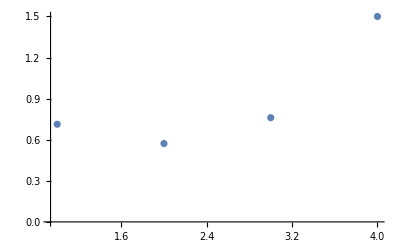

```mathematica
ListPlot[MinSqueezeTableDuration,PlotRange->All]
```

```mathematica
StateTable1
```

{{{{0.248228-0.332204 ⅈ}},{{0.485954+0.195874 ⅈ}},{{-0.203706+0.234633 ⅈ}},{{0.103097-0.668078 ⅈ}}},{{{0.14797-0.251001 ⅈ}},{{0.302188-0.433289 ⅈ}},{{0.349155-0.0859216 ⅈ}},{{0.421224-0.573868 ⅈ}}},{{{-0.61978-0.412892 ⅈ}},{{-0.00933484-0.410052 ⅈ}},{{0.169493-0.217305 ⅈ}},{{-0.0526771-0.445465 ⅈ}}},{{{0.0689222-0.34677 ⅈ,0.308843+0.172092 ⅈ,-0.341534+0.091403 ⅈ}},{{-0.348037+0.503855 ⅈ,-0.202924-0.577773 ⅈ,-0.0409916+0.610999 ⅈ}},{{0.503855-0.348037 ⅈ,-0.577773-0.202924 ⅈ,0.610999-0.0409916 ⅈ}},{{-0.34677+0.0689222 ⅈ,0.172092+0.308843 ⅈ,0.091403-0.341534 ⅈ}}}}

```mathematica
N[UHmuti[2.4326914578262837,2.752749435119288,0.9683310195962411,totT].StateθϕInitial[Pi/2,Pi/2]]
```

{{-0.350597-0.0456269 ⅈ},{-0.232162+0.566658 ⅈ},{0.566658-0.232162 ⅈ},{-0.0456269-0.350597 ⅈ}}

```mathematica
N[StateEvo[1,1,1,totT,Pi/2,Pi/2]]
```

{{0.350015+0.0498935 ⅈ},{-0.515294-0.330866 ⅈ},{-0.330866-0.515294 ⅈ},{0.0498935+0.350015 ⅈ}}

```mathematica
N[UHmuti[1,1,1,totT].StateθϕInitial[Pi/2,Pi/2]]
```

{{0.350015+0.0498935 ⅈ},{-0.515294-0.330866 ⅈ},{-0.330866-0.515294 ⅈ},{0.0498935+0.350015 ⅈ}}

```mathematica
ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],1]]
```

{0.758623,0.758623,0.758623,0.758623,0.758623,0.648784}

```mathematica
MinSqueezeTableϕ
```

{{{2.53991,1.99369,2.55964}},{{2.98751,2.71411,2.3247}},{{2.41303,0.258926,2.36829}},{{2.42272,2.1112,2.58549}},{{0.603462,2.97488,0.770736}},{{1.16242,2.22788,1.28694}},{{1.14362,2.76486,2.83111}},{{1.16657,2.09146,0.194363}},{{1.58759,3.30007,2.79382}},{{0.758623,2.75021,2.22354},{0.758623,2.75021,1.52036},{0.758623,2.75021,1.52036},{0.758623,2.75021,1.52036},{0.758623,2.75021,1.52036},{0.648784,2.75021,1.52036}}}

```mathematica
StateTable1
```

{{{{0.201725-0.0654113 ⅈ}},{{0.235812+0.564071 ⅈ}},{{-0.711608+0.1315 ⅈ}},{{0.115263-0.21043 ⅈ}}},{{{0.0934694+0.0176953 ⅈ}},{{0.213376+0.271783 ⅈ}},{{-0.874266+0.0401981 ⅈ}},{{0.317648-0.068538 ⅈ}}},{{{-0.219491-0.373993 ⅈ}},{{0.189971+0.842158 ⅈ}},{{0.105404-0.10671 ⅈ}},{{0.139874-0.156757 ⅈ}}},{{{-0.220618+0.0763235 ⅈ}},{{0.623678-0.0165248 ⅈ}},{{-0.330064+0.341477 ⅈ}},{{0.565109+0.106576 ⅈ}}},{{{0.138388-0.171028 ⅈ}},{{0.281761-0.43008 ⅈ}},{{0.354506-0.0233232 ⅈ}},{{0.357392-0.65825 ⅈ}}},{{{-0.199385-0.358735 ⅈ}},{{0.257296-0.206457 ⅈ}},{{0.61205-0.092015 ⅈ}},{{0.24629-0.528202 ⅈ}}},{{{-0.385983+0.198207 ⅈ}},{{0.165756-0.407676 ⅈ}},{{0.629619+0.0421792 ⅈ}},{{0.412247+0.223405 ⅈ}}},{{{0.043432-0.147134 ⅈ}},{{-0.438603-0.0271897 ⅈ}},{{0.755548-0.351351 ⅈ}},{{-0.298259-0.00974802 ⅈ}}},{{{-0.0293284+0.469349 ⅈ}},{{0.120825+0.277313 ⅈ}},{{0.707756+0.175417 ⅈ}},{{0.374794+0.123245 ⅈ}}},{{{-0.301261-0.185045 ⅈ,-0.110142-0.335959 ⅈ,-0.110142-0.335959 ⅈ,-0.110142-0.335959 ⅈ,-0.110142-0.335959 ⅈ,-0.072651-0.346008 ⅈ}},{{-0.233602+0.566065 ⅈ,-0.233602+0.566065 ⅈ,-0.233602+0.566065 ⅈ,-0.233602+0.566065 ⅈ,-0.233602+0.566065 ⅈ,-0.233602+0.566065 ⅈ}},{{0.566065-0.233602 ⅈ,0.566065-0.233602 ⅈ,0.566065-0.233602 ⅈ,0.566065-0.233602 ⅈ,0.566065-0.233602 ⅈ,0.566065-0.233602 ⅈ}},{{-0.185045-0.301261 ⅈ,-0.335959-0.110142 ⅈ,-0.335959-0.110142 ⅈ,-0.335959-0.110142 ⅈ,-0.335959-0.110142 ⅈ,-0.346008-0.072651 ⅈ}}}}

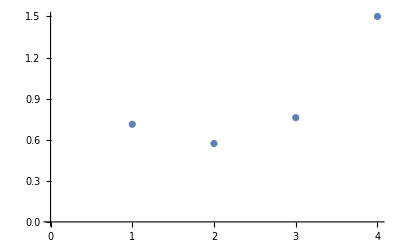

```mathematica
SqueezeCheckTable=Table[0,{i,1,Durationnumber}];
Do[
SqueezeCheckTable[[i]]=ξSqure[Flatten[StateTable1[[i]],1]];
,{i,1,Durationnumber}]
ListPlot[SqueezeCheckTable]
```

```mathematica
StateTable2=Table[0,{i,1,Durationnumber}];
Do[
StateTable2[[j]]=StateEvo[Flatten[MinSqueezeTableϕ[[j]]][[1]],Flatten[MinSqueezeTableϕ[[j]]][[2]],Flatten[MinSqueezeTableϕ[[j]]][[3]],totT,Pi/2,Pi/2]
,{j,1,Durationnumber}];
```

```mathematica
MinSqueezeTableϕ[[2]]
```

{{0.371867,1.62693,0.254885}}

```mathematica
StateTable1[[j]]
```

```mathematica
ϕ1graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,t].state]]])/10^-8
```

```mathematica
MinSqueezeTableDuration2=Table[0,{i,1,Durationnumber}];
MinSqueezeTableϕ2=Table[0,{i,1,Durationnumber}]; 
StateTable12=Table[0,{i,1,Durationnumber}];

Do[
totT=j/Durationnumber*Pi;

ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];
SqueezeTable=Table[0,{i,1,itenumber}];
SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],totT,Pi/2,Pi/2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.075*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i+1,2]]=ϕTable[[i+1-1,2]]-0.075*ϕ2gra[ϕTable[[i+1-1,1]],ϕTable[[i+1-1,2]],ϕTable[[i+1-1,3]],totT];
ϕTable[[i+2,3]]=ϕTable[[i+2-1,3]]-0.075*ϕ3gra[ϕTable[[i+2-1,1]],ϕTable[[i+2-1,2]],ϕTable[[i+2-1,3]],totT];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber-2}];
Do[

SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],totT,Pi/2,Pi/2]]]];
(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];
MinSqueezeTableDuration[[j]]=Min[SqueezeTable];
MinSqueezeTableϕ[[j]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]]]];
Print[MinSqueezeTableϕ[[j]]];
StateTable1[[j]]=StateEvo[ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],1]],ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],2]],ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]],3]],totT,Pi/2,Pi/2];

Print[ϕTable];
Print[SqueezeTable];
If[Divisible[j,100],Print[j]];

,{j,1,Durationnumber}];
```

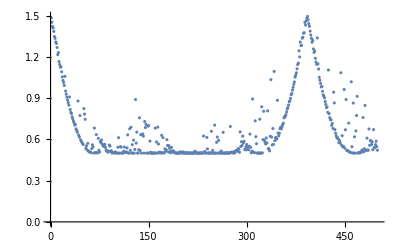

```mathematica
ListPlot[MinSqueezeTableDuration,PlotRange->All]
```

```mathematica
MinSqueezeTableDuration
```

{1.48316,1.45133,1.42141,1.40972,1.38475,1.34698,1.33405,1.30825,1.29701,1.26792,1.21593,1.2312,1.16578,1.14387,1.125,1.12723,1.09109,1.05459,1.02948,1.01339,0.991728,1.05828,0.950637,0.928101,0.906484,0.886169,0.867204,0.848791,0.908061,0.817377,0.79623,0.787723,0.763622,0.749466,0.733739,0.720388,0.703658,0.707625,0.676448,0.665163,0.65199,0.879062,0.630662,0.616817,0.773299,0.596287,0.586914,0.577701,0.569396,0.5627,0.82389,0.78375,0.745674,0.534561,0.552987,0.523644,0.571061,0.514387,0.511508,0.508001,0.505904,0.503666,0.532135,0.560332,0.545046,0.500215,0.682355,0.503749,0.502135,0.634705,0.502799,0.502104,0.607168,0.521163,0.507787,0.583908,0.577401,0.595778,0.565866,0.556253,0.551035,0.546622,0.563306,0.5409,0.520486,0.513247,0.516206,0.507103,0.514123,0.55873,0.550564,0.5127,0.517854,0.50083,0.504281,0.502665,0.502682,0.500513,0.509348,0.502077,0.501542,0.500246,0.542299,0.612366,0.500081,0.500071,0.54715,0.543416,0.500531,0.500873,0.500492,0.513305,0.544191,0.506571,0.504338,0.508906,0.53781,0.632483,0.500001,0.500191,0.676882,0.520179,0.688146,0.500367,0.561302,0.500012,0.594541,0.500042,0.526461,0.889529,0.572922,0.652461,0.500054,0.500495,0.524669,0.756544,0.519226,0.634013,0.500001,0.635038,0.639091,0.623453,0.5,0.729871,0.685945,0.708713,0.500207,0.500004,0.696036,0.699934,0.500009,0.587244,0.506117,0.500115,0.500025,0.500079,0.50037,0.500438,0.500458,0.681433,0.500624,0.581327,0.500789,0.689124,0.566015,0.506085,0.500076,0.505735,0.501228,0.629263,0.502356,0.612204,0.501436,0.501892,0.530949,0.514332,0.523282,0.59789,0.55616,0.509419,0.554304,0.535869,0.50256,0.515482,0.542265,0.506528,0.516148,0.515564,0.50568,0.502613,0.502269,0.500376,0.500575,0.500226,0.50005,0.500005,0.500005,0.507441,0.509185,0.500703,0.504455,0.500455,0.508618,0.500544,0.500043,0.50366,0.500151,0.500407,0.500111,0.503328,0.500185,0.500029,0.500457,0.500587,0.500035,0.500164,0.500494,0.500081,0.500022,0.507783,0.513602,0.500028,0.501238,0.501628,0.500001,0.500516,0.500354,0.500077,0.500006,0.500031,0.503475,0.500002,0.500063,0.624475,0.504606,0.511953,0.500103,0.500115,0.614299,0.530289,0.500041,0.501267,0.500015,0.500576,0.501068,0.658523,0.500261,0.519674,0.50134,0.500201,0.70343,0.500029,0.500006,0.578649,0.616997,0.500066,0.592786,0.500175,0.502781,0.500006,0.515272,0.500272,0.501123,0.65089,0.500012,0.500375,0.500382,0.500159,0.501912,0.500002,0.502926,0.500003,0.500005,0.500789,0.693496,0.505976,0.506379,0.502207,0.501885,0.509932,0.500005,0.50466,0.513839,0.520631,0.514241,0.516893,0.532828,0.528715,0.505927,0.654328,0.547766,0.583566,0.555889,0.623231,0.574524,0.585335,0.527232,0.523876,0.545023,0.562559,0.526252,0.546054,0.523712,0.549381,0.638169,0.541782,0.502789,0.514839,0.893426,0.506467,0.505603,0.503262,0.734431,0.619497,0.568061,0.50038,0.500232,0.500005,0.500001,0.746893,0.500029,0.500259,0.836986,0.501559,0.597646,0.804066,0.595247,0.58006,0.565996,0.610209,0.574011,0.807354,0.532461,0.532038,0.516061,0.62264,1.03416,0.616659,0.559812,0.678646,0.563032,1.09384,0.590609,0.611337,0.612812,0.602038,0.883857,0.645554,0.625109,0.644734,0.677406,0.688221,0.67668,0.69213,0.706376,0.717113,0.756411,0.76578,0.765052,0.77984,0.799628,0.821313,0.830727,0.849673,0.873304,0.878871,0.897733,0.924445,0.933277,0.95786,0.97752,0.999991,1.01764,1.05202,1.06653,1.08343,1.1129,1.1434,1.15462,1.24344,1.19929,1.30743,1.28173,1.28378,1.3356,1.34178,1.37114,1.37624,1.45068,1.4314,1.46099,1.48115,1.49345,1.46924,1.44139,1.42184,1.38684,1.35848,1.335,1.30649,1.32002,1.25712,1.232,1.2427,1.1894,1.16219,1.1455,1.33733,1.14848,1.11117,1.05089,1.02964,1.00653,0.981122,0.98454,0.949658,0.923444,0.913959,0.902044,0.87562,0.854063,0.831431,0.835825,0.796178,1.10441,0.787204,0.757982,0.743202,0.741825,0.701771,0.715507,0.679882,0.942745,0.86469,0.670617,0.644692,0.625142,0.611435,0.612746,0.601997,0.575232,0.590094,0.574928,1.08425,0.558161,0.626783,0.545508,0.549406,0.962703,0.536041,0.669864,0.889406,0.519509,0.520361,0.514743,0.718264,0.509545,0.506507,0.503715,1.01828,0.546525,0.501302,0.8639,0.500019,0.618373,0.500001,0.661235,0.773475,0.912534,0.500433,0.502362,0.502824,0.502347,0.506394,0.50467,0.517982,0.523972,0.758212,0.508979,0.53126,0.846631,0.522343,0.519323,0.608903,0.523723,0.521025,0.675566,0.556406,0.590297,0.589905,0.562725,0.580498,0.524447,0.671116,0.541643,0.539851,0.562311,0.586229,0.547052,0.5211}

{{0.0738275,1.3086,2.18718},{2.95091,1.52251,2.21646},{0.117493,1.85072,0.332315},{0.457294,1.94996,0.855113},{3.15298,1.44626,1.90996},{3.27733,2.14431,2.57542},{0.506325,1.46953,0.389011},{3.45005,1.70676,1.95901},{2.80047,1.64158,2.23856},{0.083923,1.56934,1.15697},{-0.288022,1.66001,0.633454},{4.69355,1.55089,0.50427},{3.53641,1.46674,2.63228},{-0.332002,1.61675,0.620457},{3.61075,1.60115,2.40615},{-0.50067,1.58451,1.26701},{5.31909,1.55492,0.685691},{3.53862,1.69241,2.52217},{0.334145,-1.45073,-0.462547},{3.61647,1.63146,2.46706},{3.6701,1.60653,2.49539},{-1.41927,1.54193,2.49343},{3.56053,1.70686,2.51417},{3.55499,1.67811,2.58075},{-0.352524,1.57965,0.518031},{-0.348065,1.57662,0.450495},{-0.344239,1.57641,0.427699},{-0.309332,1.58199,0.402553},{-1.72828,1.51186,2.46739},{3.61927,1.62848,2.59232},{-0.332225,1.57114,0.356712},{3.60099,1.71254,2.51259},{-0.332989,1.57329,0.366719},{3.42277,1.64999,2.72672},{-0.355099,1.57602,0.461457},{3.57096,1.63913,2.64685},{-0.331464,1.57133,0.335807},{-2.37532,1.50426,2.4524},{-0.329702,1.57088,0.335105},{3.59433,1.59071,2.68959},{0.434423,-1.56836,-0.412338},{-0.240601,1.50608,2.48482},{3.61899,1.63977,2.63935},{-0.323365,1.5689,0.289},{0.653313,1.27698,1.06894},{0.394552,-1.56823,-0.367637},{-0.321169,1.5672,0.261064},{-0.287332,1.57335,0.298403},{-0.319883,1.56597,0.24749},{3.59332,1.64,2.66048},{0.717047,1.72621,2.45819},{0.269908,1.51453,2.41724},{2.28647,2.42296,2.52668},{3.55295,1.65367,2.69758},{2.31124,-1.31315,4.01434},{3.5664,1.62634,2.69962},{3.0717,1.54149,2.64288},{-0.270568,1.57755,0.308703},{3.54093,1.66167,2.68924},{3.58046,1.55833,2.72884},{-0.193337,1.57351,0.201363},{-0.189913,1.57773,0.221236},{1.02291,-1.47258,0.276384},{0.224893,1.38456,1.61877},{0.0407519,1.37606,1.66394},{3.60089,1.66727,2.62397},{1.47126,2.11202,2.54232},{2.3375,-0.906855,3.69586},{3.68674,1.5058,2.61803},{1.95794,2.51692,2.51706},{0.0728939,1.60116,0.0495742},{0.137043,1.60132,-0.037112},{1.98792,2.51879,2.59002},{1.65204,-1.50307,0.487924},{0.211331,1.62446,-0.0174602},{1.92198,2.56679,2.5986},{1.92619,2.58537,2.58804},{1.07744,1.78778,2.27692},{0.938661,1.75347,2.06691},{1.87194,2.54089,2.61603},{1.91869,2.61901,2.62238},{1.94086,2.66033,2.60616},{1.02568,1.7237,2.30873},{0.92225,1.75099,2.09377},{2.0709,-1.47617,0.775803},{2.01813,-1.47523,0.741255},{2.07417,-1.46824,0.803527},{4.46712,1.64794,-0.199085},{0.839307,1.66273,2.0976},{1.03652,1.83699,-0.0333478},{0.997236,1.81226,-0.0928852},{2.20495,-1.44163,0.896414},{2.78324,-0.825113,1.60687},{0.730557,1.64371,2.10646},{0.859846,1.70172,2.14495},{0.842294,1.69629,2.17055},{0.87895,1.6904,2.22272},{0.828289,1.6795,2.18211},{2.12779,3.10293,2.47334},{1.96382,2.67922,2.6892},{2.79521,-0.926419,1.60842},{0.896518,1.70415,2.27708},{1.18314,1.8078,-0.304191},{2.13046,0.0698044,0.545407},{0.988772,1.73486,2.36562},{0.985039,1.73352,2.36744},{1.25445,1.82538,-0.28643},{1.23611,1.80903,-0.318664},{1.05163,1.75217,2.45162},{1.12021,1.77989,2.53284},{1.14327,1.81318,2.53881},{2.16056,3.35514,2.35317},{1.0894,1.9322,2.20346},{2.13318,3.28637,2.43345},{1.13376,1.80591,2.54769},{0.641078,3.17901,2.27384},{1.26709,1.79773,-0.400157},{1.13113,2.04583,2.06991},{2.44639,0.27356,2.24149},{2.44924,0.276094,2.27208},{0.392643,2.93292,2.72133},{1.15128,1.83079,2.63287},{1.51692,1.40254,3.04067},{2.43844,0.331744,2.30345},{0.929459,1.6359,2.55942},{2.42235,0.370506,2.26572},{1.19338,2.02203,2.3673},{2.41715,0.394069,2.28143},{1.24219,1.74711,-0.585367},{1.15018,3.37158,0.584349},{1.35655,2.07793,2.64595},{2.61413,4.58608,0.756235},{2.40851,0.446886,2.29662},{2.42534,0.446528,2.34673},{2.01919,2.02577,0.298131},{2.16114,0.485529,0.66196},{2.06795,2.06593,0.502616},{1.31929,2.08212,2.63683},{2.01918,-0.105126,-2.20938},{1.26479,2.06882,2.75528},{1.20409,1.98757,2.81322},{2.4224,2.20832,0.43987},{2.40015,0.538303,2.28225},{0.756199,2.88922,0.754947},{1.31644,1.30973,3.08262},{0.733273,2.87298,0.762929},{2.41751,0.566547,2.33192},{2.23818,3.72108,2.39009},{1.20778,1.18272,2.92625},{1.17062,1.14375,2.89971},{2.17753,3.74432,2.38114},{2.7226,0.539429,2.62587},{2.13027,-0.27774,-1.8214},{-0.955561,2.35526,2.50389},{2.0745,2.0435,0.312971},{2.13433,2.18639,0.680444},{2.40419,0.642467,2.26391},{2.40011,0.651596,2.22207},{2.41646,0.653689,2.26848},{1.19442,1.08799,2.82254},{2.42813,0.664093,2.30093},{0.517079,2.71007,0.841041},{2.43796,0.674377,2.32297},{2.37661,2.33687,1.99009},{0.49187,2.68856,0.855019},{2.16182,2.27543,0.789037},{1.08742,-0.776408,2.18376},{1.86473,1.84225,-0.170104},{2.47112,0.702013,2.38376},{2.51623,0.989196,2.51668},{2.18429,2.37511,1.05212},{0.907041,0.965141,1.99237},{2.49448,0.717476,2.42258},{2.20071,2.41377,1.14801},{0.461001,2.66711,0.810743},{2.20792,2.3973,0.972325},{1.20957,3.22608,0.817501},{1.0082,1.04873,2.14272},{1.72402,1.33339,3.69635},{2.24755,2.51724,1.14558},{2.01993,1.66282,0.0390715},{1.54904,4.0894,3.4272},{2.22082,2.55192,1.29271},{2.14645,2.5323,1.15524},{2.18691,2.52462,0.892396},{2.22298,2.55548,1.31021},{0.433804,2.56163,0.763414},{0.440394,2.57495,0.750328},{3.84798,0.368142,2.11117},{1.41005,3.37189,0.811867},{1.45581,3.38779,0.818487},{1.38651,-0.313733,2.14243},{1.37016,-0.279742,2.13038},{1.58368,3.3487,0.935767},{1.52958,3.38098,0.873488},{1.48891,3.40313,0.824211},{1.43943,3.42843,0.77018},{0.606921,2.14678,1.07946},{0.540865,2.31004,0.910608},{2.73314,0.744232,2.61788},{0.802974,1.81477,1.45056},{2.77272,0.723483,2.64591},{0.558401,2.35492,0.872329},{1.41486,3.52789,0.652885},{0.246534,1.45575,4.36535},{0.676521,2.21015,1.06528},{2.84443,0.708515,2.65566},{1.3462,3.59827,0.550543},{1.3486,3.58794,0.538057},{0.626041,0.503074,1.52856},{1.37414,3.62879,0.52254},{0.263442,1.49705,-1.89564},{1.41506,3.67616,0.504868},{0.831981,2.16519,1.20079},{3.03966,0.629396,2.52683},{2.21617,1.57929,4.11676},{1.45878,3.76165,0.461762},{1.42726,3.76561,0.450361},{0.835107,2.23635,1.20399},{3.10903,0.596258,2.35012},{3.11806,0.580595,2.28468},{0.832102,2.28325,1.18561},{2.29744,1.58447,4.18575},{1.10722,1.85846,2.05685},{0.822203,2.33155,1.14682},{1.82142,1.56017,-0.299475},{0.80414,2.36176,1.0826},{2.21628,1.56889,4.09013},{0.814932,2.38134,1.12733},{0.808593,2.39671,1.11564},{1.64251,4.19515,0.300297},{0.815692,2.41416,1.12949},{2.18537,1.56592,4.05837},{3.02986,0.765129,2.27461},{2.5189,1.57309,-1.96028},{1.65823,4.06629,0.399054},{1.84274,1.44477,-0.253871},{0.809758,2.47083,1.12709},{-0.25786,0.475589,0.142975},{1.62144,4.25357,0.256747},{2.23723,1.56889,4.065},{1.22847,-0.654949,0.862402},{2.23089,1.56573,4.06023},{2.09813,1.59657,3.92196},{0.750404,2.57464,1.11636},{-0.332844,0.456981,0.17986},{1.88628,1.32471,-0.181927},{2.56768,5.39208,-0.455307},{1.30972,-0.54065,0.832395},{2.36225,1.53078,4.13539},{-0.385358,0.37008,0.254141},{-0.689247,2.48432,2.55695},{1.7789,1.29198,-0.209877},{1.90627,4.23379,0.465769},{2.00115,0.260581,0.45133},{1.72914,1.26686,-0.205875},{2.24618,0.0385368,0.617412},{0.748281,2.72406,1.27685},{0.704174,2.72234,1.20207},{1.37576,1.34827,-0.421051},{1.44505,2.33023,2.9977},{2.38573,1.52686,4.10157},{0.01318,2.11179,4.34651},{1.25622,3.18808,2.88361},{0.720982,2.86107,1.41159},{2.35295,1.49054,4.03561},{-0.409882,2.47295,3.7774},{0.691517,2.90711,1.43794},{1.3267,1.29343,-0.393891},{0.673268,2.97815,1.50963},{1.30394,1.28814,-0.390634},{0.646023,3.04578,1.56689},{0.625153,3.08514,1.59619},{1.75963,0.0601641,0.600293},{2.54257,0.345779,1.0744},{1.21719,1.30386,-0.426684},{1.17093,1.31729,-0.467929},{2.27775,1.68577,3.84419},{2.28497,1.65981,3.86075},{2.17993,1.63028,3.73427},{-0.7654,-1.5663,0.757857},{0.409269,3.46854,1.75223},{1.08483,1.42353,-0.394094},{1.60033,0.0189203,0.62278},{0.370337,3.58195,1.84436},{0.362717,3.58595,1.82153},{1.58005,0.0274328,0.614001},{0.519039,3.32237,1.71742},{2.36733,1.73046,3.79681},{1.94822,0.900538,3.15781},{1.57921,0.0886373,0.569905},{-0.360539,2.60943,4.20783},{0.461218,3.42391,1.77891},{2.11877,0.907288,3.19314},{0.302463,3.69326,1.88594},{-0.303022,2.56539,4.38138},{0.863495,1.49332,-0.303469},{0.824549,1.50541,-0.317113},{2.48284,1.24319,3.3667},{3.46333,4.10299,2.14793},{0.690118,1.54419,-0.272324},{3.49998,4.23877,2.19019},{0.639412,1.55378,-0.263697},{2.81487,1.36388,3.31358},{0.216265,3.78088,1.77687},{2.65441,1.25251,3.24531},{2.70827,1.61253,3.58463},{2.66676,1.37361,3.38184},{3.97028,2.3689,-0.495846},{0.417324,1.57332,-0.292494},{6.6664,1.5745,-0.285218},{6.65464,1.57486,-0.301956},{0.810939,2.48542,-0.299219},{3.3209,4.06409,2.0175},{3.3485,4.1648,2.23048},{0.291835,1.5726,-0.305485},{2.83965,1.54358,3.41536},{0.276811,1.57013,-0.28063},{2.89024,1.56991,3.3914},{0.103339,3.93076,1.63297},{0.201169,1.57122,-0.193738},{2.95878,1.58436,3.32554},{0.79956,1.10883,0.212186},{0.16728,1.56779,-0.182775},{3.1592,4.01566,2.35902},{0.0769483,3.90548,1.62536},{-0.260482,-1.5268,0.81087},{2.48093,1.06249,2.95748},{2.92132,1.06748,2.96928},{3.20217,4.10787,2.349},{-0.255746,-1.36168,0.519843},{2.66843,3.34307,2.04311},{-0.175708,-1.54933,0.233817},{0.11678,1.56254,-0.188669},{2.90165,4.7469,3.4361},{-0.183424,-1.44826,0.672101},{0.508331,2.88559,0.94907},{3.12847,4.17619,2.61403},{0.0319051,1.5476,-0.179057},{2.54514,1.51846,2.91315},{3.10528,1.52559,3.14065},{0.355352,0.224277,1.19456},{0.0151863,1.54206,-0.174653},{3.00464,1.54077,2.78421},{0.0101912,1.53401,-0.210145},{3.18016,1.42686,3.00961},{1.18129,1.91706,-0.0246856},{6.24333,1.51412,-0.229642},{2.68299,4.61553,3.61772},{-0.0195473,1.63999,0.087307},{-0.0263918,1.52147,-0.210962},{-0.0395249,1.5217,-0.200653},{0.0911988,-1.51405,-0.158492},{2.6529,4.60406,3.7644},{0.105619,-1.47224,-0.227658},{-0.607881,1.53263,0.378555},{-0.0419357,1.51889,-0.207292},{0.0347002,1.58642,-0.128616},{3.23792,1.43424,3.05435},{3.21853,1.3962,2.99913},{3.17404,1.45876,3.09675},{0.0836322,1.67569,0.114648},{3.19464,1.41305,3.03862},{2.49648,4.46645,3.6988},{-0.0730998,1.605,-0.0792406},{2.66618,4.50249,3.6168},{2.66628,4.50628,3.63718},{3.23664,1.5023,3.15946},{-0.5321,1.56036,0.378507},{3.29445,1.30092,2.93809},{-0.137527,1.69819,0.129586},{2.61114,4.40015,3.64939},{2.69899,4.47603,3.63567},{5.43619,1.52549,0.753906},{-0.548215,1.653,0.749336},{3.31161,1.30367,2.9551},{3.04683,1.31284,2.94307},{5.3261,1.4904,0.747746},{-0.128341,1.77818,0.0733974},{2.33626,1.13309,2.84697},{3.32536,1.23212,2.96121},{2.26475,1.86979,2.84741},{0.109941,2.45821,0.756177},{0.0788968,2.32453,0.206283},{4.13206,1.52022,1.05504},{-0.551249,1.84152,1.29769},{2.62558,2.0685,2.90583},{3.12578,1.02662,2.81246},{0.0159852,0.510518,1.82941},{3.35444,1.58896,2.17658},{2.7565,0.543655,2.41742},{0.00144233,1.10509,0.208396},{0.739797,2.759,0.44041},{2.60407,0.793997,2.80132},{2.85773,1.00844,2.89014},{3.47227,1.2547,1.87793},{3.4407,1.59478,2.39383},{3.33219,1.71642,2.69167},{3.56769,1.5869,2.39485},{3.59835,1.55291,2.57674},{-0.29241,1.44283,1.54508},{-0.235449,1.99881,0.280098},{-0.221919,1.91066,0.234145},{2.65821,0.813011,2.99218},{3.21391,1.22153,3.01491},{-0.157736,1.71705,0.0702995},{5.74812,1.22355,-0.0119363},{3.56782,2.37034,0.298941},{-1.43589,1.67999,2.10731},{-1.79089,1.65171,2.313},{2.84643,4.54521,3.64118},{5.99667,1.29753,0.0111474},{-0.15859,1.83727,0.188145},{3.39018,1.4528,2.86778},{-2.23904,1.56701,2.26402},{2.89994,4.52311,3.55665},{0.414143,-1.34682,-0.436574},{3.85939,1.54664,2.41623},{-0.201739,1.37058,-0.162467},{3.19847,1.41005,3.05708},{2.64536,4.59779,3.72398},{0.44418,-1.40007,-0.481406},{3.97486,1.53617,2.26682},{-0.111381,1.67317,0.281573},{2.41027,2.4433,3.07492},{0.00672653,1.57043,-0.143547},{3.14582,1.4878,3.04987},{-0.0488659,1.69531,0.0572863},{4.02277,1.54625,2.387},{3.61833,1.55457,2.72251},{3.12388,1.55581,3.28968},{3.74783,1.5671,2.59687},{2.99276,1.41741,1.83211},{2.53666,0.590324,3.13219},{3.16135,1.61821,3.35506},{0.0541075,1.68216,0.0182992},{-0.0452738,1.68408,0.113453},{0.513186,-1.50484,-0.600357},{3.95524,1.58974,2.41538},{3.86977,1.63793,2.69019},{0.342413,-1.54049,-0.347804},{0.0341853,1.49474,-0.12831},{3.07514,1.52415,3.04947},{0.84088,3.04637,2.01584},{3.14066,1.52269,3.13768},{0.0451316,-1.09361,0.599487},{0.0640717,1.67623,0.0588976},{3.09953,1.5914,3.32268},{2.69175,-0.324317,1.51106},{3.09444,1.58634,3.3042},{-0.045578,-0.90471,0.928023},{1.6949,1.14322,3.12344},{0.124882,1.63589,-0.0591901},{3.02497,1.58317,3.33471},{3.03731,1.58029,3.3076},{2.55691,2.13763,3.2989},{0.164447,1.61505,-0.140477},{3.01979,1.57781,3.31169},{0.154645,1.61712,-0.0980881},{2.94065,2.32271,0.422418},{0.43509,2.05062,0.200132},{2.95172,1.57122,3.33282},{2.76292,0.586834,3.40819},{0.183298,1.57122,-0.181317},{-0.136237,-0.895715,1.02335},{2.90054,1.57056,3.38077},{2.91728,1.98883,3.40126},{1.57907,1.64284,3.51423},{2.31915,1.10231,2.66562},{2.82862,1.56927,3.44905},{-3.44991,1.56658,3.40832},{0.371101,1.66203,-0.279346},{2.76858,1.56806,3.45268},{2.76719,1.56669,3.40635},{0.384715,1.62702,-0.31421},{0.447197,1.77576,-0.176707},{0.458137,1.79746,-0.152089},{1.88939,0.718801,3.4851},{2.62788,1.57385,3.46867},{0.527043,1.8434,-0.173135},{2.50007,1.48974,2.58076},{0.596974,1.83638,-0.27284},{2.43554,1.60145,3.4471},{2.67416,-0.195618,1.53115},{2.43397,1.60202,3.4351},{2.27894,1.65555,3.4905},{-0.203081,-1.04742,1.43578},{0.543486,1.79357,-0.225042},{0.875454,2.0999,-0.1032},{0.938033,2.141,-0.132007},{2.84044,-0.538206,1.3085},{1.05097,1.99406,-0.201833},{2.05293,1.79657,3.52677},{-0.131276,-1.11014,1.46779},{2.67437,-0.290402,1.33438},{0.923214,1.82603,-0.371122},{1.01378,1.93159,-0.303525},{1.12407,2.01747,-0.246426},{1.01135,1.80142,-0.367933},{1.39594,3.00167,2.59213}}

```mathematica
Flatten[MinSqueezeTableϕ,1]
```

{{0.0738275,1.3086,2.18718},{2.95091,1.52251,2.21646},{0.117493,1.85072,0.332315},{0.457294,1.94996,0.855113},{3.15298,1.44626,1.90996},{3.27733,2.14431,2.57542},{0.506325,1.46953,0.389011},{3.45005,1.70676,1.95901},{2.80047,1.64158,2.23856},{0.083923,1.56934,1.15697},{-0.288022,1.66001,0.633454},{4.69355,1.55089,0.50427},{3.53641,1.46674,2.63228},{-0.332002,1.61675,0.620457},{3.61075,1.60115,2.40615},{-0.50067,1.58451,1.26701},{5.31909,1.55492,0.685691},{3.53862,1.69241,2.52217},{0.334145,-1.45073,-0.462547},{3.61647,1.63146,2.46706},{3.6701,1.60653,2.49539},{-1.41927,1.54193,2.49343},{3.56053,1.70686,2.51417},{3.55499,1.67811,2.58075},{-0.352524,1.57965,0.518031},{-0.348065,1.57662,0.450495},{-0.344239,1.57641,0.427699},{-0.309332,1.58199,0.402553},{-1.72828,1.51186,2.46739},{3.61927,1.62848,2.59232},{-0.332225,1.57114,0.356712},{3.60099,1.71254,2.51259},{-0.332989,1.57329,0.366719},{3.42277,1.64999,2.72672},{-0.355099,1.57602,0.461457},{3.57096,1.63913,2.64685},{-0.331464,1.57133,0.335807},{-2.37532,1.50426,2.4524},{-0.329702,1.57088,0.335105},{3.59433,1.59071,2.68959},{0.434423,-1.56836,-0.412338},{-0.240601,1.50608,2.48482},{3.61899,1.63977,2.63935},{-0.323365,1.5689,0.289},{0.653313,1.27698,1.06894},{0.394552,-1.56823,-0.367637},{-0.321169,1.5672,0.261064},{-0.287332,1.57335,0.298403},{-0.319883,1.56597,0.24749},{3.59332,1.64,2.66048},{0.717047,1.72621,2.45819},{0.269908,1.51453,2.41724},{2.28647,2.42296,2.52668},{3.55295,1.65367,2.69758},{2.31124,-1.31315,4.01434},{3.5664,1.62634,2.69962},{3.0717,1.54149,2.64288},{-0.270568,1.57755,0.308703},{3.54093,1.66167,2.68924},{3.58046,1.55833,2.72884},{-0.193337,1.57351,0.201363},{-0.189913,1.57773,0.221236},{1.02291,-1.47258,0.276384},{0.224893,1.38456,1.61877},{0.0407519,1.37606,1.66394},{3.60089,1.66727,2.62397},{1.47126,2.11202,2.54232},{2.3375,-0.906855,3.69586},{3.68674,1.5058,2.61803},{1.95794,2.51692,2.51706},{0.0728939,1.60116,0.0495742},{0.137043,1.60132,-0.037112},{1.98792,2.51879,2.59002},{1.65204,-1.50307,0.487924},{0.211331,1.62446,-0.0174602},{1.92198,2.56679,2.5986},{1.92619,2.58537,2.58804},{1.07744,1.78778,2.27692},{0.938661,1.75347,2.06691},{1.87194,2.54089,2.61603},{1.91869,2.61901,2.62238},{1.94086,2.66033,2.60616},{1.02568,1.7237,2.30873},{0.92225,1.75099,2.09377},{2.0709,-1.47617,0.775803},{2.01813,-1.47523,0.741255},{2.07417,-1.46824,0.803527},{4.46712,1.64794,-0.199085},{0.839307,1.66273,2.0976},{1.03652,1.83699,-0.0333478},{0.997236,1.81226,-0.0928852},{2.20495,-1.44163,0.896414},{2.78324,-0.825113,1.60687},{0.730557,1.64371,2.10646},{0.859846,1.70172,2.14495},{0.842294,1.69629,2.17055},{0.87895,1.6904,2.22272},{0.828289,1.6795,2.18211},{2.12779,3.10293,2.47334},{1.96382,2.67922,2.6892},{2.79521,-0.926419,1.60842},{0.896518,1.70415,2.27708},{1.18314,1.8078,-0.304191},{2.13046,0.0698044,0.545407},{0.988772,1.73486,2.36562},{0.985039,1.73352,2.36744},{1.25445,1.82538,-0.28643},{1.23611,1.80903,-0.318664},{1.05163,1.75217,2.45162},{1.12021,1.77989,2.53284},{1.14327,1.81318,2.53881},{2.16056,3.35514,2.35317},{1.0894,1.9322,2.20346},{2.13318,3.28637,2.43345},{1.13376,1.80591,2.54769},{0.641078,3.17901,2.27384},{1.26709,1.79773,-0.400157},{1.13113,2.04583,2.06991},{2.44639,0.27356,2.24149},{2.44924,0.276094,2.27208},{0.392643,2.93292,2.72133},{1.15128,1.83079,2.63287},{1.51692,1.40254,3.04067},{2.43844,0.331744,2.30345},{0.929459,1.6359,2.55942},{2.42235,0.370506,2.26572},{1.19338,2.02203,2.3673},{2.41715,0.394069,2.28143},{1.24219,1.74711,-0.585367},{1.15018,3.37158,0.584349},{1.35655,2.07793,2.64595},{2.61413,4.58608,0.756235},{2.40851,0.446886,2.29662},{2.42534,0.446528,2.34673},{2.01919,2.02577,0.298131},{2.16114,0.485529,0.66196},{2.06795,2.06593,0.502616},{1.31929,2.08212,2.63683},{2.01918,-0.105126,-2.20938},{1.26479,2.06882,2.75528},{1.20409,1.98757,2.81322},{2.4224,2.20832,0.43987},{2.40015,0.538303,2.28225},{0.756199,2.88922,0.754947},{1.31644,1.30973,3.08262},{0.733273,2.87298,0.762929},{2.41751,0.566547,2.33192},{2.23818,3.72108,2.39009},{1.20778,1.18272,2.92625},{1.17062,1.14375,2.89971},{2.17753,3.74432,2.38114},{2.7226,0.539429,2.62587},{2.13027,-0.27774,-1.8214},{-0.955561,2.35526,2.50389},{2.0745,2.0435,0.312971},{2.13433,2.18639,0.680444},{2.40419,0.642467,2.26391},{2.40011,0.651596,2.22207},{2.41646,0.653689,2.26848},{1.19442,1.08799,2.82254},{2.42813,0.664093,2.30093},{0.517079,2.71007,0.841041},{2.43796,0.674377,2.32297},{2.37661,2.33687,1.99009},{0.49187,2.68856,0.855019},{2.16182,2.27543,0.789037},{1.08742,-0.776408,2.18376},{1.86473,1.84225,-0.170104},{2.47112,0.702013,2.38376},{2.51623,0.989196,2.51668},{2.18429,2.37511,1.05212},{0.907041,0.965141,1.99237},{2.49448,0.717476,2.42258},{2.20071,2.41377,1.14801},{0.461001,2.66711,0.810743},{2.20792,2.3973,0.972325},{1.20957,3.22608,0.817501},{1.0082,1.04873,2.14272},{1.72402,1.33339,3.69635},{2.24755,2.51724,1.14558},{2.01993,1.66282,0.0390715},{1.54904,4.0894,3.4272},{2.22082,2.55192,1.29271},{2.14645,2.5323,1.15524},{2.18691,2.52462,0.892396},{2.22298,2.55548,1.31021},{0.433804,2.56163,0.763414},{0.440394,2.57495,0.750328},{3.84798,0.368142,2.11117},{1.41005,3.37189,0.811867},{1.45581,3.38779,0.818487},{1.38651,-0.313733,2.14243},{1.37016,-0.279742,2.13038},{1.58368,3.3487,0.935767},{1.52958,3.38098,0.873488},{1.48891,3.40313,0.824211},{1.43943,3.42843,0.77018},{0.606921,2.14678,1.07946},{0.540865,2.31004,0.910608},{2.73314,0.744232,2.61788},{0.802974,1.81477,1.45056},{2.77272,0.723483,2.64591},{0.558401,2.35492,0.872329},{1.41486,3.52789,0.652885},{0.246534,1.45575,4.36535},{0.676521,2.21015,1.06528},{2.84443,0.708515,2.65566},{1.3462,3.59827,0.550543},{1.3486,3.58794,0.538057},{0.626041,0.503074,1.52856},{1.37414,3.62879,0.52254},{0.263442,1.49705,-1.89564},{1.41506,3.67616,0.504868},{0.831981,2.16519,1.20079},{3.03966,0.629396,2.52683},{2.21617,1.57929,4.11676},{1.45878,3.76165,0.461762},{1.42726,3.76561,0.450361},{0.835107,2.23635,1.20399},{3.10903,0.596258,2.35012},{3.11806,0.580595,2.28468},{0.832102,2.28325,1.18561},{2.29744,1.58447,4.18575},{1.10722,1.85846,2.05685},{0.822203,2.33155,1.14682},{1.82142,1.56017,-0.299475},{0.80414,2.36176,1.0826},{2.21628,1.56889,4.09013},{0.814932,2.38134,1.12733},{0.808593,2.39671,1.11564},{1.64251,4.19515,0.300297},{0.815692,2.41416,1.12949},{2.18537,1.56592,4.05837},{3.02986,0.765129,2.27461},{2.5189,1.57309,-1.96028},{1.65823,4.06629,0.399054},{1.84274,1.44477,-0.253871},{0.809758,2.47083,1.12709},{-0.25786,0.475589,0.142975},{1.62144,4.25357,0.256747},{2.23723,1.56889,4.065},{1.22847,-0.654949,0.862402},{2.23089,1.56573,4.06023},{2.09813,1.59657,3.92196},{0.750404,2.57464,1.11636},{-0.332844,0.456981,0.17986},{1.88628,1.32471,-0.181927},{2.56768,5.39208,-0.455307},{1.30972,-0.54065,0.832395},{2.36225,1.53078,4.13539},{-0.385358,0.37008,0.254141},{-0.689247,2.48432,2.55695},{1.7789,1.29198,-0.209877},{1.90627,4.23379,0.465769},{2.00115,0.260581,0.45133},{1.72914,1.26686,-0.205875},{2.24618,0.0385368,0.617412},{0.748281,2.72406,1.27685},{0.704174,2.72234,1.20207},{1.37576,1.34827,-0.421051},{1.44505,2.33023,2.9977},{2.38573,1.52686,4.10157},{0.01318,2.11179,4.34651},{1.25622,3.18808,2.88361},{0.720982,2.86107,1.41159},{2.35295,1.49054,4.03561},{-0.409882,2.47295,3.7774},{0.691517,2.90711,1.43794},{1.3267,1.29343,-0.393891},{0.673268,2.97815,1.50963},{1.30394,1.28814,-0.390634},{0.646023,3.04578,1.56689},{0.625153,3.08514,1.59619},{1.75963,0.0601641,0.600293},{2.54257,0.345779,1.0744},{1.21719,1.30386,-0.426684},{1.17093,1.31729,-0.467929},{2.27775,1.68577,3.84419},{2.28497,1.65981,3.86075},{2.17993,1.63028,3.73427},{-0.7654,-1.5663,0.757857},{0.409269,3.46854,1.75223},{1.08483,1.42353,-0.394094},{1.60033,0.0189203,0.62278},{0.370337,3.58195,1.84436},{0.362717,3.58595,1.82153},{1.58005,0.0274328,0.614001},{0.519039,3.32237,1.71742},{2.36733,1.73046,3.79681},{1.94822,0.900538,3.15781},{1.57921,0.0886373,0.569905},{-0.360539,2.60943,4.20783},{0.461218,3.42391,1.77891},{2.11877,0.907288,3.19314},{0.302463,3.69326,1.88594},{-0.303022,2.56539,4.38138},{0.863495,1.49332,-0.303469},{0.824549,1.50541,-0.317113},{2.48284,1.24319,3.3667},{3.46333,4.10299,2.14793},{0.690118,1.54419,-0.272324},{3.49998,4.23877,2.19019},{0.639412,1.55378,-0.263697},{2.81487,1.36388,3.31358},{0.216265,3.78088,1.77687},{2.65441,1.25251,3.24531},{2.70827,1.61253,3.58463},{2.66676,1.37361,3.38184},{3.97028,2.3689,-0.495846},{0.417324,1.57332,-0.292494},{6.6664,1.5745,-0.285218},{6.65464,1.57486,-0.301956},{0.810939,2.48542,-0.299219},{3.3209,4.06409,2.0175},{3.3485,4.1648,2.23048},{0.291835,1.5726,-0.305485},{2.83965,1.54358,3.41536},{0.276811,1.57013,-0.28063},{2.89024,1.56991,3.3914},{0.103339,3.93076,1.63297},{0.201169,1.57122,-0.193738},{2.95878,1.58436,3.32554},{0.79956,1.10883,0.212186},{0.16728,1.56779,-0.182775},{3.1592,4.01566,2.35902},{0.0769483,3.90548,1.62536},{-0.260482,-1.5268,0.81087},{2.48093,1.06249,2.95748},{2.92132,1.06748,2.96928},{3.20217,4.10787,2.349},{-0.255746,-1.36168,0.519843},{2.66843,3.34307,2.04311},{-0.175708,-1.54933,0.233817},{0.11678,1.56254,-0.188669},{2.90165,4.7469,3.4361},{-0.183424,-1.44826,0.672101},{0.508331,2.88559,0.94907},{3.12847,4.17619,2.61403},{0.0319051,1.5476,-0.179057},{2.54514,1.51846,2.91315},{3.10528,1.52559,3.14065},{0.355352,0.224277,1.19456},{0.0151863,1.54206,-0.174653},{3.00464,1.54077,2.78421},{0.0101912,1.53401,-0.210145},{3.18016,1.42686,3.00961},{1.18129,1.91706,-0.0246856},{6.24333,1.51412,-0.229642},{2.68299,4.61553,3.61772},{-0.0195473,1.63999,0.087307},{-0.0263918,1.52147,-0.210962},{-0.0395249,1.5217,-0.200653},{0.0911988,-1.51405,-0.158492},{2.6529,4.60406,3.7644},{0.105619,-1.47224,-0.227658},{-0.607881,1.53263,0.378555},{-0.0419357,1.51889,-0.207292},{0.0347002,1.58642,-0.128616},{3.23792,1.43424,3.05435},{3.21853,1.3962,2.99913},{3.17404,1.45876,3.09675},{0.0836322,1.67569,0.114648},{3.19464,1.41305,3.03862},{2.49648,4.46645,3.6988},{-0.0730998,1.605,-0.0792406},{2.66618,4.50249,3.6168},{2.66628,4.50628,3.63718},{3.23664,1.5023,3.15946},{-0.5321,1.56036,0.378507},{3.29445,1.30092,2.93809},{-0.137527,1.69819,0.129586},{2.61114,4.40015,3.64939},{2.69899,4.47603,3.63567},{5.43619,1.52549,0.753906},{-0.548215,1.653,0.749336},{3.31161,1.30367,2.9551},{3.04683,1.31284,2.94307},{5.3261,1.4904,0.747746},{-0.128341,1.77818,0.0733974},{2.33626,1.13309,2.84697},{3.32536,1.23212,2.96121},{2.26475,1.86979,2.84741},{0.109941,2.45821,0.756177},{0.0788968,2.32453,0.206283},{4.13206,1.52022,1.05504},{-0.551249,1.84152,1.29769},{2.62558,2.0685,2.90583},{3.12578,1.02662,2.81246},{0.0159852,0.510518,1.82941},{3.35444,1.58896,2.17658},{2.7565,0.543655,2.41742},{0.00144233,1.10509,0.208396},{0.739797,2.759,0.44041},{2.60407,0.793997,2.80132},{2.85773,1.00844,2.89014},{3.47227,1.2547,1.87793},{3.4407,1.59478,2.39383},{3.33219,1.71642,2.69167},{3.56769,1.5869,2.39485},{3.59835,1.55291,2.57674},{-0.29241,1.44283,1.54508},{-0.235449,1.99881,0.280098},{-0.221919,1.91066,0.234145},{2.65821,0.813011,2.99218},{3.21391,1.22153,3.01491},{-0.157736,1.71705,0.0702995},{5.74812,1.22355,-0.0119363},{3.56782,2.37034,0.298941},{-1.43589,1.67999,2.10731},{-1.79089,1.65171,2.313},{2.84643,4.54521,3.64118},{5.99667,1.29753,0.0111474},{-0.15859,1.83727,0.188145},{3.39018,1.4528,2.86778},{-2.23904,1.56701,2.26402},{2.89994,4.52311,3.55665},{0.414143,-1.34682,-0.436574},{3.85939,1.54664,2.41623},{-0.201739,1.37058,-0.162467},{3.19847,1.41005,3.05708},{2.64536,4.59779,3.72398},{0.44418,-1.40007,-0.481406},{3.97486,1.53617,2.26682},{-0.111381,1.67317,0.281573},{2.41027,2.4433,3.07492},{0.00672653,1.57043,-0.143547},{3.14582,1.4878,3.04987},{-0.0488659,1.69531,0.0572863},{4.02277,1.54625,2.387},{3.61833,1.55457,2.72251},{3.12388,1.55581,3.28968},{3.74783,1.5671,2.59687},{2.99276,1.41741,1.83211},{2.53666,0.590324,3.13219},{3.16135,1.61821,3.35506},{0.0541075,1.68216,0.0182992},{-0.0452738,1.68408,0.113453},{0.513186,-1.50484,-0.600357},{3.95524,1.58974,2.41538},{3.86977,1.63793,2.69019},{0.342413,-1.54049,-0.347804},{0.0341853,1.49474,-0.12831},{3.07514,1.52415,3.04947},{0.84088,3.04637,2.01584},{3.14066,1.52269,3.13768},{0.0451316,-1.09361,0.599487},{0.0640717,1.67623,0.0588976},{3.09953,1.5914,3.32268},{2.69175,-0.324317,1.51106},{3.09444,1.58634,3.3042},{-0.045578,-0.90471,0.928023},{1.6949,1.14322,3.12344},{0.124882,1.63589,-0.0591901},{3.02497,1.58317,3.33471},{3.03731,1.58029,3.3076},{2.55691,2.13763,3.2989},{0.164447,1.61505,-0.140477},{3.01979,1.57781,3.31169},{0.154645,1.61712,-0.0980881},{2.94065,2.32271,0.422418},{0.43509,2.05062,0.200132},{2.95172,1.57122,3.33282},{2.76292,0.586834,3.40819},{0.183298,1.57122,-0.181317},{-0.136237,-0.895715,1.02335},{2.90054,1.57056,3.38077},{2.91728,1.98883,3.40126},{1.57907,1.64284,3.51423},{2.31915,1.10231,2.66562},{2.82862,1.56927,3.44905},{-3.44991,1.56658,3.40832},{0.371101,1.66203,-0.279346},{2.76858,1.56806,3.45268},{2.76719,1.56669,3.40635},{0.384715,1.62702,-0.31421},{0.447197,1.77576,-0.176707},{0.458137,1.79746,-0.152089},{1.88939,0.718801,3.4851},{2.62788,1.57385,3.46867},{0.527043,1.8434,-0.173135},{2.50007,1.48974,2.58076},{0.596974,1.83638,-0.27284},{2.43554,1.60145,3.4471},{2.67416,-0.195618,1.53115},{2.43397,1.60202,3.4351},{2.27894,1.65555,3.4905},{-0.203081,-1.04742,1.43578},{0.543486,1.79357,-0.225042},{0.875454,2.0999,-0.1032},{0.938033,2.141,-0.132007},{2.84044,-0.538206,1.3085},{1.05097,1.99406,-0.201833},{2.05293,1.79657,3.52677},{-0.131276,-1.11014,1.46779},{2.67437,-0.290402,1.33438},{0.923214,1.82603,-0.371122},{1.01378,1.93159,-0.303525},{1.12407,2.01747,-0.246426},{1.01135,1.80142,-0.367933},{1.39594,3.00167,2.59213}}

```mathematica
MinSqueezeTableDuration
```

{1.21934,0.9906,0.75333,0.801837,0.829965,0.526551,1.09585,0.58186,0.627933,0.546815,0.733663,0.582343,0.532284,0.680932,0.532828,0.5591,0.545236,0.537523,0.56751,0.546047}

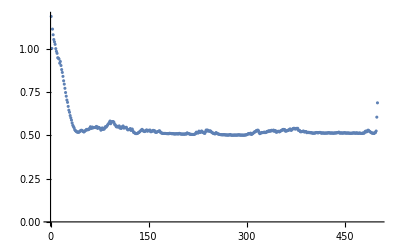

```mathematica
ListPlot[SqueezeTable,PlotRange->All]
```

```mathematica
ListPlot[SqueezeTable,PlotRange->All]
```

-Graphics-

```mathematica
1.3019
```

```mathematica
1.175828
```

```mathematica
StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]
```